```mathematica
Quit[]
```

```mathematica
(*STEP 1:Load FeynCalc with FeynArts*)$LoadAddOns={"FeynArts"};

Needs["FeynCalc`"];

$FAVerbose=0;

Print["======================================"];
Print["STEP 1: PACKAGE INITIALIZATION"];
Print["======================================"];

Print["FeynCalc version: ",$FeynCalcVersion];
Print["FeynArts directory: ",$FeynArtsDirectory];


(*STEP 2:Define Phi4 model directory*)

Print[""];
Print["STEP 2: MODEL DIRECTORY"];

faModelsDir=FileNameJoin[{$FeynArtsDirectory,"Models"}];

phi4Dir=FileNameJoin[{faModelsDir,"Phi4"}];

phi4Name=FileNameJoin[{"Phi4","Phi4"}];

Print["Phi4 directory: ",phi4Dir];


(*STEP 3:Verify required model files*)

Print[""];
Print["STEP 3: VERIFY MODEL FILES"];

requiredFiles={"Phi4.mod","Phi4.gen","Phi4.pars"};

fileChecks=Association[Table[file->FileExistsQ[FileNameJoin[{phi4Dir,file}]],{file,requiredFiles}]];

KeyValueMap[(Print[#1,": ",#2])&,fileChecks];

If[!And@@Values[fileChecks],Print["ERROR: One or more model files are missing."];
Abort[];];

Print["All required model files found."];


(*STEP 4:Check the previous line-84 error*)

Print[""];
Print["STEP 4: CHECK GENERIC MODEL SYNTAX"];

genFile=FileNameJoin[{phi4Dir,"Phi4.gen"}];

genText=Import[genFile,"Text"];

If[!StringQ[genText],Print["ERROR: Cannot read Phi4.gen."];
Abort[];];

malformedIndexSum=StringContainsQ[genText,RegularExpression["IndexSum\\s*\\[\\s*,"]];

Print["Malformed IndexSum detected: ",malformedIndexSum];

If[malformedIndexSum,Print["ERROR: Old line-84 syntax issue detected."];
Print["Restore the corrected Phi4 model files."];
Abort[];];

Print["Known syntax problem not detected."];


(*STEP 5:Verify FeynArts functions*)

Print[""];
Print["STEP 5: VERIFY FEYNARTS FUNCTIONS"];

functionNames={"CreateTopologies","InsertFields","Paint","CreateFeynAmp","InitializeModel"};

functionMatches=Table[Names["*`"<>name],{name,functionNames}];

Do[Print[functionNames[[i]],": ",functionMatches[[i]]],{i,Length[functionNames]}];

If[AnyTrue[functionMatches,#==={}&],Print["ERROR: Some FeynArts functions are missing."];
Abort[];];

Print["FeynArts functions found."];


(*STEP 6:Check model search path*)

Print[""];
Print["STEP 6: CONFIGURE MODEL SEARCH PATH"];

If[!MemberQ[$ModelPath,faModelsDir],AppendTo[$ModelPath,faModelsDir]];

Print["Phi4 model name: ",phi4Name];

Print["Model file exists: ",FileExistsQ[FileNameJoin[{phi4Dir,"Phi4.mod"}]]];


(*STEP 7:Initialize Phi4*)

Print[""];
Print["STEP 7: INITIALIZE PHI4 MODEL"];

modelResult=InitializeModel[phi4Name,GenericModel->phi4Name];

Print["Initialization result: ",modelResult];

If[modelResult=!=True,Print["ERROR: Phi4 model initialization failed."];
Abort[];];


(*STEP 8:Final confirmation*)

Print[""];
Print["======================================"];
Print["PHI4 ENVIRONMENT READY"];
Print["======================================"];

Print["FeynCalc: Loaded"];
Print["FeynArts: Loaded"];
Print["Phi4 files: Found"];
Print["Known line-84 error: Not detected"];
Print["Model initialization: Successful"];

Print[""];
Print["You may now generate Feynman diagrams."];
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

======================================

STEP 1: PACKAGE INITIALIZATION

======================================

FeynCalc version: 10.2.1

FeynArts directory: C:\Users\sirmo\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts

STEP 2: MODEL DIRECTORY

Phi4 directory: C:\Users\sirmo\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts\Models\Phi4

STEP 3: VERIFY MODEL FILES

Phi4.mod: True

Phi4.gen: True

Phi4.pars: True

All required model files found.

STEP 4: CHECK GENERIC MODEL SYNTAX

Malformed IndexSum detected: False

Known syntax problem not detected.

STEP 5: VERIFY FEYNARTS FUNCTIONS

CreateTopologies: {CreateTopologies}

InsertFields: {InsertFields}

Paint: {Paint}

CreateFeynAmp: {CreateFeynAmp}

InitializeModel: {InitializeModel}

FeynArts functions found.

STEP 6: CONFIGURE MODEL SEARCH PATH

Phi4 model name: Phi4\Phi4

Model file exists: True

STEP 7: INITIALIZE PHI4 MODEL

Initialization result: True

======================================

PHI4 ENVIRONMENT READY

======================================

FeynCalc: Loaded

FeynArts: Loaded

Phi4 files: Found

Known line-84 error: Not detected

Model initialization: Successful

You may now generate Feynman diagrams.

SECTION 1.1

```mathematica
(* ============================================================*)(*PART 1-WARM-UP WITH ONE LOOP AND TWO REGULATORS*)(*SECTION 1.1.0-INITIALIZATION AND THEORETICAL CONVENTIONS*)(* ============================================================*)(*References:QFT I,Chapter 4,p.36:Euclidean propagator QFT I,Chapter 8,p.61:Phi^4 action QFT I,Chapter 9,p.77:Proper vertices QFT I,Chapter 13,p.120:One-loop channel momenta Assignment conventions:d=4-eps g=lambda/(16 Pi^2) m^2>0*)(*------------------------------------------------------------*)
(*STEP 1:DEFINE SYMBOLS AND ASSUMPTIONS*)
(*------------------------------------------------------------*)

ClearAll[m,lam,muR,eps,epsFC,gReduced,dDR,dCutoff,Lambda,p,p1,p2,p3,p4,k,q,phiVar,x,pSquared,fieldDimension,couplingDimension,lagrangianSymbolic,tree2,tree4,propagatorE,interactionVertexDR,P12,P13,P14,channelMomenta,loopPrefactorDR,loopPrefactorCutoff];

$Assumptions=m>0&&muR>0&&Lambda>0&&Element[{lam,eps},Reals];

dDR=4-eps;
dCutoff=4;

epsFC=eps/2;

gReduced=lam/(16 Pi^2);

Print["Dimensional regularization: d = ",dDR];
Print["Sharp cutoff dimension: d = ",dCutoff];
Print["Reduced coupling g = ",gReduced];
Print["FeynCalc regulator epsFC = ",epsFC];


(*------------------------------------------------------------*)
(*STEP 2:DEFINE THE EUCLIDEAN ACTION DENSITY*)
(*------------------------------------------------------------*)

(*The kinetic term is represented by the symbolic quantity gradPhiSquared=(partial_mu phi)(partial_mu phi).The position-space integration is not performed here.*)

ClearAll[gradPhiSquared];

lagrangianSymbolic=gradPhiSquared/2+m^2 phiVar^2/2+muR^eps lam phiVar^4/Factorial[4];

Print["Euclidean Lagrangian density:"];

lagrangianSymbolic//TraditionalForm;


(*------------------------------------------------------------*)
(*STEP 3:DERIVE THE FREE TWO-POINT VERTEX*)
(*------------------------------------------------------------*)

(*Fourier transformation maps-partial^2->p^2. Therefore the inverse free propagator is p^2+m^2.*)

tree2[pSquared_]:=pSquared+m^2;

propagatorE[pSquared_]:=1/tree2[pSquared];

Print["Tree-level two-point vertex:"];

tree2[p^2]//TraditionalForm;

Print["Euclidean scalar propagator:"];

propagatorE[p^2]//TraditionalForm;


(*Verify the inverse-propagator relation.*)

checkPropagator=FullSimplify[tree2[p^2] propagatorE[p^2]==1];

Print["Inverse propagator verification: ",checkPropagator];


(*------------------------------------------------------------*)
(*STEP 4:DERIVE THE FOUR-POINT INTERACTION COEFFICIENT*)
(*------------------------------------------------------------*)

(*The fourth derivative of phi^4 produces 4!.*)

vertexDerivative=D[phiVar^4,{phiVar,4}];

vertexCoefficient=FullSimplify[muR^eps lam/Factorial[4]*vertexDerivative];

(*Strip the overall mu^eps as required by the assignment.*)

tree4=lam;

interactionVertexDR=muR^eps tree4;

Print["Fourth derivative of phi^4: ",vertexDerivative];

Print["Interaction coefficient including mu^eps:"];

vertexCoefficient//TraditionalForm;

Print["Tree-level four-point vertex (mu^eps stripped):"];

tree4//TraditionalForm;

Print["Interaction coefficient verification: ",FullSimplify[vertexCoefficient==interactionVertexDR]];


(*------------------------------------------------------------*)
(*STEP 5:VERIFY CANONICAL MASS DIMENSIONS*)
(*------------------------------------------------------------*)

(*From the kinetic term:[phi]=(d-2)/2. The mass dimension of the quartic coupling coefficient is d-4[phi]=4-d=eps.*)

fieldDimension=(dDR-2)/2;

couplingDimension=FullSimplify[dDR-4 fieldDimension];

Print["Scalar field mass dimension: ",fieldDimension];

Print["Quartic coefficient mass dimension: ",couplingDimension];

Print["Expected quartic coefficient dimension eps: ",FullSimplify[couplingDimension==eps]];


(*------------------------------------------------------------*)
(*STEP 6:DEFINE MOMENTUM CONVENTIONS*)
(*------------------------------------------------------------*)

(*All external momenta are incoming:p1+p2+p3+p4=0. The three channel momenta are:P12=p1+p2 P13=p1+p3 P14=p1+p4*)

P12=p1+p2;
P13=p1+p3;
P14=p1+p4;

channelMomenta=<|"s-channel"->P12,"t-channel"->P13,"u-channel"->P14|>;

Print["Four-point channel momenta:"];

channelMomenta//TraditionalForm;


(*------------------------------------------------------------*)
(*STEP 7:DEFINE LOOP-MEASURE NORMALIZATIONS*)
(*------------------------------------------------------------*)

(*In DR,each loop carries:mu^eps d^d k/(2 Pi)^d.For the cutoff:d^4 k/(2 Pi)^4,with|k| <Lambda.*)

loopPrefactorDR=muR^eps/(2 Pi)^dDR;

loopPrefactorCutoff=1/(2 Pi)^4;

Print["DR loop measure prefactor:"];

loopPrefactorDR//TraditionalForm;

Print["Sharp-cutoff loop measure prefactor:"];

loopPrefactorCutoff//TraditionalForm;

Print["Sharp cutoff domain: |k| < Lambda"];


(*------------------------------------------------------------*)
(*STEP 8:FINAL CONSISTENCY CHECKS*)
(*------------------------------------------------------------*)

checks110=<|"d = 4 - eps"->(dDR==4-eps),"d cutoff = 4"->(dCutoff==4),"eps = 2 epsFC"->(eps==2 epsFC),"g definition"->(gReduced==lam/(16 Pi^2)),"Propagator inverse"->checkPropagator,"Quartic vertex"->FullSimplify[vertexCoefficient==muR^eps lam],"Quartic mass dimension"->FullSimplify[couplingDimension==eps]|>;

Print["Consistency checks for Section 1.1.0:"];

checks110//Dataset

Print["End of Section 1.1.0."];
```

Dimensional regularization: d = 4-eps

Sharp cutoff dimension: d = 4

Reduced coupling g = lam/(16 π^2)

FeynCalc regulator epsFC = eps/2

Euclidean Lagrangian density:

Tree-level two-point vertex:

Euclidean scalar propagator:

Inverse propagator verification: True

Fourth derivative of phi^4: 24

Interaction coefficient including mu^eps:

Tree-level four-point vertex (mu^eps stripped):

Interaction coefficient verification: True

Scalar field mass dimension: (2-eps)/2

Quartic coefficient mass dimension: eps

Expected quartic coefficient dimension eps: True

Four-point channel momenta:

DR loop measure prefactor:

Sharp-cutoff loop measure prefactor:

Sharp cutoff domain: |k| < Lambda

Consistency checks for Section 1.1.0:

End of Section 1.1.0.

SECTION 1.1.1: ONE-LOOP TWO-POINT DIAGRAM

Topology equations solved:

Number of Wick contractions: 12

Quartic factorial: 24

Tadpole coefficient 1/S: 1/2

Tadpole symmetry factor S: 2

FeynArts model: Phi4\Phi4

One-loop two-point topologies generated.

Phi4 fields inserted into the topologies.

ONE-LOOP 1PI TWO-POINT FEYNMAN DIAGRAM:

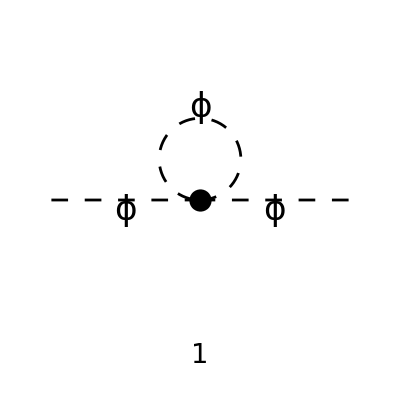

FeynArtsGraphics()(([1]))

Euclidean tadpole integrand:

SECTION 1.1.1 VERIFICATION:

```mathematica
(* ============================================================*)(*SECTION 1.1.1-ONE-LOOP 1PI TWO-POINT DIAGRAM*)(* ============================================================*)(*References:QFT I,Chapter 8,pp.63-64:Wick contractions and tadpole symmetry factor.QFT I,Chapter 13,p.119:One-loop correction to the two-point proper vertex.*)Print["SECTION 1.1.1: ONE-LOOP TWO-POINT DIAGRAM"];


(*------------------------------------------------------------*)
(*STEP 1:DETERMINE THE NUMBER OF VERTICES AND PROPAGATORS*)
(*------------------------------------------------------------*)

(*A connected quartic diagram satisfies:4 V=2 I+E L=I-V+1 For the present diagram:E=2,L=1.*)

ClearAll[nVertices,nInternal,nExternal,nLoops];

topologySolution=Solve[{4 nVertices==2 nInternal+2,1==nInternal-nVertices+1},{nVertices,nInternal}];

Print["Topology equations solved:"];

topologySolution//TraditionalForm;

(*Expected:V=1,I=1*)


(*------------------------------------------------------------*)
(*STEP 2:DERIVE THE SYMMETRY FACTOR FROM WICK CONTRACTIONS*)
(*------------------------------------------------------------*)

(*First external field:4 choices.Second external field:3 choices.Remaining internal pair:1 choice.Interaction expansion contributes 1/4!.*)

nContractions=4*3*1;

quarticFactor=Factorial[4];

tadpoleCoefficient=FullSimplify[nContractions/quarticFactor];

tadpoleSymmetryFactor=1/tadpoleCoefficient;

Print["Number of Wick contractions: ",nContractions];

Print["Quartic factorial: ",quarticFactor];

Print["Tadpole coefficient 1/S: ",tadpoleCoefficient];

Print["Tadpole symmetry factor S: ",tadpoleSymmetryFactor];


(*------------------------------------------------------------*)
(*STEP 3:DEFINE THE FEYNARTS PHI4 MODEL*)
(*------------------------------------------------------------*)

(*Use the custom Phi4 model installed previously.S[1] denotes the real scalar field.*)

phi4Model11=FileNameJoin[{"Phi4","Phi4"}];

phi4Options11={InsertionLevel->{Classes},Model->phi4Model11,GenericModel->phi4Model11};

Print["FeynArts model: ",phi4Model11];


(*------------------------------------------------------------*)
(*STEP 4:GENERATE ONE-LOOP TWO-POINT TOPOLOGIES*)
(*------------------------------------------------------------*)

(*CreateTopologies[1,1->1]:First argument:one loop.1->1:one incoming and one outgoing external leg.Exclude reducible topologies and external-leg corrections.Do not exclude Tadpoles:the tadpole is our target diagram.*)

top2Point11=CreateTopologies[1,1->1,ExcludeTopologies->{Reducible,WFCorrections}];

Print["One-loop two-point topologies generated."];


(*------------------------------------------------------------*)
(*STEP 5:INSERT THE SCALAR FIELD*)
(*------------------------------------------------------------*)

(*Both external legs represent the real scalar S[1].InsertFields applies the interaction rules of the Phi4 model.*)

diag2Point11=InsertFields[top2Point11,{S[1]}->{S[1]},Sequence@@phi4Options11];

Print["Phi4 fields inserted into the topologies."];


(*------------------------------------------------------------*)
(*STEP 6:DISPLAY THE ONE-LOOP TADPOLE DIAGRAM*)
(*------------------------------------------------------------*)

Print["ONE-LOOP 1PI TWO-POINT FEYNMAN DIAGRAM:"];

Paint[diag2Point11,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,FieldNumbers->True,ImageSize->{450,300}]


(*------------------------------------------------------------*)
(*STEP 7:DEFINE THE EXPECTED EUCLIDEAN LOOP INTEGRAND*)
(*------------------------------------------------------------*)

(*The propagator carries loop momentum k.Its Euclidean denominator is k^2+m^2. The full one-loop integral will be evaluated in Section 1.2.*)

ClearAll[kSquared11];

tadpolePropagator11=1/(kSquared11+m^2);

tadpoleIntegrand11=tadpoleCoefficient*lam*tadpolePropagator11;

Print["Euclidean tadpole integrand:"];

tadpoleIntegrand11//TraditionalForm;


(*------------------------------------------------------------*)
(*STEP 8:VERIFY THE EXPECTED RESULTS*)
(*------------------------------------------------------------*)

topologyCheck11=topologySolution==={{nVertices->1,nInternal->1}};

symmetryCheck11=tadpoleCoefficient==1/2;

momentumCheck11=FreeQ[tadpoleIntegrand11,p];

verification11=<|"One quartic vertex"->topologyCheck11,"One internal propagator"->topologyCheck11,"Symmetry coefficient = 1/2"->symmetryCheck11,"No external momentum dependence"->momentumCheck11|>;

Print["SECTION 1.1.1 VERIFICATION:"];
```

```mathematica
(* ============================================================*)(*SECTION 1.1.2-TWO-POINT AMPLITUDE AND FEYNCALC CONVERSION*)(* ============================================================*)(*References:QFT I,Chapter 4,pp.35-37:Minkowski and Euclidean propagators.QFT I,Chapter 13,pp.118-119:One-loop two-point proper vertex.*)Print["SECTION 1.1.2: TWO-POINT FEYNMAN AMPLITUDE"];


(*------------------------------------------------------------*)
(*STEP 1:GENERATE THE FEYNARTS AMPLITUDE*)
(*------------------------------------------------------------*)

(*Use the tadpole diagram obtained in Section 1.1.1.The diagram contains:-One quartic vertex-One internal scalar propagator-Symmetry factor 1/2*)

faAmp2Point112=CreateFeynAmp[diag2Point11,Truncated->True,PreFactor->1];

Print["1. Original FeynArts amplitude:"];

Print[TraditionalForm[faAmp2Point112]];


(*------------------------------------------------------------*)
(*STEP 2:CONVERT TO FEYNCALC NOTATION*)
(*------------------------------------------------------------*)

(*External momentum:p Loop momentum:q The model coupling g is replaced by lam.*)

amp2FC112=FCFAConvert[faAmp2Point112,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->D,List->False,FinalSubstitutions->{g->lam}];


(*------------------------------------------------------------*)
(*STEP 3:STANDARDIZE THE SCALAR MASS*)
(*------------------------------------------------------------*)

(*The custom model generates the propagator mass as:mphi Sqrt[GaugeXi[S[1]]] For the real scalar theory in our assignment:mphi->m GaugeXi[S[1]]->1 Therefore the propagator mass becomes m.*)

amp2FC112=FCI[amp2FC112/. {mphi->m,GaugeXi[S[1]]->1}];

Print["2. FeynCalc amplitude with standard mass m:"];

Print[TraditionalForm[amp2FC112]];


(*------------------------------------------------------------*)
(*STEP 4:DISPLAY THE EXPLICIT PROPAGATOR*)
(*------------------------------------------------------------*)

amp2Explicit112=FeynAmpDenominatorExplicit[amp2FC112];

Print["3. Explicit Minkowski amplitude:"];

Print[TraditionalForm[amp2Explicit112]];


(*------------------------------------------------------------*)
(*STEP 5:PASSARINO-VELTMAN REPRESENTATION*)
(*------------------------------------------------------------*)

(*The tadpole is expressed through A0(m^2).The loop measure is still kept separate.*)

amp2PV112=ToPaVe[amp2FC112,q];

Print["4. Passarino-Veltman representation:"];

Print[TraditionalForm[amp2PV112]];


(*------------------------------------------------------------*)
(*STEP 6:EUCLIDEAN FORM*)
(*------------------------------------------------------------*)

(*Wick rotation:qM^2->-qE^2 Euclidean scalar propagator:1/(qE^2+m^2) qE2 denotes the Euclidean squared momentum.*)

ClearAll[qE2,pE2,tadpoleT];

euclideanIntegrand112=lam/(2 (qE2+m^2));

Print["5. Euclidean tadpole integrand:"];

Print[TraditionalForm[euclideanIntegrand112]];


(*------------------------------------------------------------*)
(*STEP 7:COMPLETE EUCLIDEAN TWO-POINT VERTEX*)
(*------------------------------------------------------------*)

(*Define the regularized tadpole integral symbolically:T=mu^eps Integral[d^(4-eps)q/(2Pi)^(4-eps)*1/(q^2+m^2)] Its explicit evaluation belongs to Section 1.2.*)

gamma2OneLoop112=pE2+m^2+lam/2 tadpoleT;

Print["6. Two-point proper vertex through one loop:"];

Print[TraditionalForm[gamma2OneLoop112]];


(*------------------------------------------------------------*)
(*STEP 8:CONCLUSION*)
(*------------------------------------------------------------*)

Print["The tadpole is independent of external momentum."];

Print["Its symmetry coefficient is 1/2."];

Print["The loop integral will be evaluated in Section 1.2."];

Print["END OF SECTION 1.1.2"];
```

SECTION 1.1.2: TWO-POINT FEYNMAN AMPLITUDE

1. Original FeynArts amplitude:

FAFeynAmpList(Process→(S(1) | p1 | mphi | {})→(S(1) | k1 | mphi | {}),Model→{Phi4\Phi4},GenericModel→{Phi4\Phi4},AmplitudeLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1,Classes==1,Number==1),Integral[q1],1/2 g FAFeynAmpDenominator(1/((q1)^2-mphi^2))))

2. FeynCalc amplitude with standard mass m:

lam/(2 (q^2-m^2))

3. Explicit Minkowski amplitude:

lam/(2 (q^2-m^2))

4. Passarino-Veltman representation:

1/2 ⅈ π^2 lam A_0(m^2)

5. Euclidean tadpole integrand:

lam/(2 (m^2+qE2))

6. Two-point proper vertex through one loop:

(lam tadpoleT)/2+m^2+pE2

The tadpole is independent of external momentum.

Its symmetry coefficient is 1/2.

The loop integral will be evaluated in Section 1.2.

END OF SECTION 1.1.2

==============================================

SECTION 1.1.3: FOUR-POINT FEYNMAN DIAGRAMS

==============================================

1. Solution of topology equations:

{{V113→2,I113→2}}

2. Number of independent four-point channels:

3

3. Number of Wick contractions:

576

4. Perturbative expansion denominator:

1152

5. Bubble coefficient 1/S:

1/2

6. Bubble symmetry factor S:

2

7. One-loop four-point topologies generated.

8. Real scalar fields inserted.

9. ONE-LOOP 1PI FOUR-POINT DIAGRAMS:

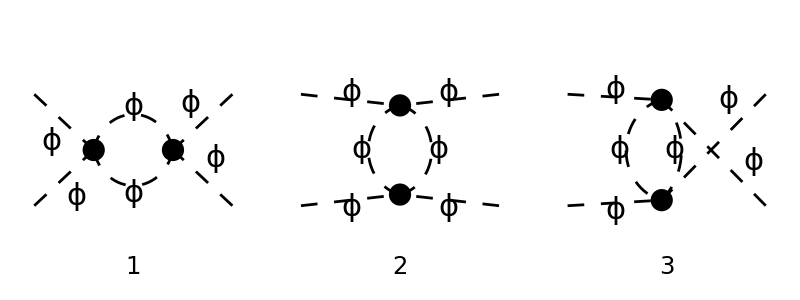

FeynArtsGraphics()(([1] | [2] | [3]))

10. Euclidean four-point channel momenta:

<|s-channel→p1+p2,t-channel→p1+p3,u-channel→p1+p4|>

Euclidean one-loop four-point correction:

-1/2 lam^2 (B(p1+p2)+B(p1+p3)+B(p1+p4))

Four-point vertex through one loop:

lam-1/2 lam^2 (B(p1+p2)+B(p1+p3)+B(p1+p4))

==============================================

SUMMARY OF SECTION 1.1.3

==============================================

Quartic vertices: 2

Internal propagators: 2

Independent channels: 3

Symmetry coefficient per channel: 1/2

Symmetry factor per channel: 2

The explicit amplitudes are calculated in Section 1.1.4.

END OF SECTION 1.1.3

```mathematica
(* ============================================================*)(*SECTION 1.1.3-ONE-LOOP 1PI FOUR-POINT DIAGRAMS*)(* ============================================================*)(*References:QFT I,Chapter 8,pp.63-66:Wick contractions and symmetry factors.QFT I,Chapter 12,pp.101-103:One-loop four-point diagrams.QFT I,Chapter 13,pp.119-120:Three-channel bubble structure,Eq.(13.18).*)Print["=============================================="];
Print["SECTION 1.1.3: FOUR-POINT FEYNMAN DIAGRAMS"];
Print["=============================================="];


(*------------------------------------------------------------*)
(*STEP 1:DETERMINE THE TOPOLOGY*)
(*------------------------------------------------------------*)

(*For connected quartic diagrams:4 V=2 I+E L=I-V+1 For the present case:E=4,L=1*)

ClearAll[V113,I113];

topologySolution113=Solve[{4 V113==2 I113+4,1==I113-V113+1},{V113,I113}];

Print["1. Solution of topology equations:"];

Print[TraditionalForm[topologySolution113]];

(*Result:V=2,I=2*)


(*------------------------------------------------------------*)
(*STEP 2:COUNT THE THREE INDEPENDENT CHANNELS*)
(*------------------------------------------------------------*)

(*Choose two of the four external legs.Interchanging the two vertices does not produce a distinct diagram.*)

numberOfChannels113=Binomial[4,2]/2;

Print["2. Number of independent four-point channels:"];

Print[TraditionalForm[numberOfChannels113]];


(*------------------------------------------------------------*)
(*STEP 3:DERIVE THE BUBBLE SYMMETRY FACTOR*)
(*------------------------------------------------------------*)

(*For one fixed channel:First vertex:4*3 external-leg attachments Second vertex:4*3 external-leg attachments Internal contractions:2! possible pairings Equivalent assignments of the two vertices:2 Perturbative expansion denominator:2! (4!)^2*)

externalAttachments113=(4*3)^2;

internalPairings113=Factorial[2];

vertexAssignments113=2;

contractions113=externalAttachments113*internalPairings113*vertexAssignments113;

expansionDenominator113=Factorial[2]*Factorial[4]^2;

bubbleCoefficient113=FullSimplify[contractions113/expansionDenominator113];

bubbleSymmetryFactor113=1/bubbleCoefficient113;

Print["3. Number of Wick contractions:"];

Print[TraditionalForm[contractions113]];

Print["4. Perturbative expansion denominator:"];

Print[TraditionalForm[expansionDenominator113]];

Print["5. Bubble coefficient 1/S:"];

Print[TraditionalForm[bubbleCoefficient113]];

Print["6. Bubble symmetry factor S:"];

Print[TraditionalForm[bubbleSymmetryFactor113]];


(*------------------------------------------------------------*)
(*STEP 4:GENERATE ONE-LOOP FOUR-POINT TOPOLOGIES*)
(*------------------------------------------------------------*)

(*One-loop topology with two incoming and two outgoing external scalar legs.The 2->2 convention is used here by FeynArts.We will convert to all-incoming external momenta in Section 1.1.4.Exclusions:-Reducible:remove non-1PI topologies.-WFCorrections:remove external-leg corrections.-Tadpoles:remove tadpole insertions.*)

top4Point113=CreateTopologies[1,2->2,ExcludeTopologies->{Reducible,WFCorrections,Tadpoles}];

Print["7. One-loop four-point topologies generated."];


(*------------------------------------------------------------*)
(*STEP 5:INSERT THE REAL SCALAR FIELD*)
(*------------------------------------------------------------*)

(*Both incoming and outgoing fields are S[1].Use the Phi4 model already defined in Section 1.1.1.*)

diag4Point113=InsertFields[top4Point113,{S[1],S[1]}->{S[1],S[1]},Sequence@@phi4Options11];

Print["8. Real scalar fields inserted."];


(*------------------------------------------------------------*)
(*STEP 6:DISPLAY THE FEYNMAN DIAGRAMS*)
(*------------------------------------------------------------*)

(*Three independent bubble channels are expected.The diagrams are displayed using FeynArts' external-leg labeling convention.*)

Print["9. ONE-LOOP 1PI FOUR-POINT DIAGRAMS:"];

Paint[diag4Point113,PaintLevel->{Classes},ColumnsXRows->{3,1},Numbering->Simple,SheetHeader->None,FieldNumbers->True,ImageSize->{800,300}]


(*------------------------------------------------------------*)
(*STEP 7:DEFINE THE CHANNEL MOMENTA*)
(*------------------------------------------------------------*)

(*The assignment uses all-incoming momenta:p1+p2+p3+p4=0. Independent channel momenta:P12=p1+p2 P13=p1+p3 P14=p1+p4*)

channelMomenta113=<|"s-channel"->P12,"t-channel"->P13,"u-channel"->P14|>;

Print["10. Euclidean four-point channel momenta:"];

Print[TraditionalForm[channelMomenta113]];


(*------------------------------------------------------------*)(*STEP 8:DEFINE THE ONE-LOOP FOUR-POINT CORRECTION*)(*------------------------------------------------------------*)(*B[P] represents the Euclidean scalar bubble integral:B(P)=mu^eps Integral[d^d q/(2 Pi)^d*1/((q^2+m^2)((q+P)^2+m^2))] The integral will be evaluated in Section 1.2.*)ClearAll[B];

gamma4Loop113=-lam^2/2 (B[P12]+B[P13]+B[P14]);

Print["Euclidean one-loop four-point correction:"];
Print[TraditionalForm[gamma4Loop113]];


(*------------------------------------------------------------*)
(*STEP 9:COMPLETE FOUR-POINT VERTEX*)
(*------------------------------------------------------------*)

gamma4Total113=lam+gamma4Loop113;

Print["Four-point vertex through one loop:"];
Print[TraditionalForm[gamma4Total113]];



(*------------------------------------------------------------*)
(*STEP 10:SUMMARY*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["SUMMARY OF SECTION 1.1.3"];
Print["=============================================="];

Print["Quartic vertices: 2"];
Print["Internal propagators: 2"];

Print["Independent channels: ",numberOfChannels113];

Print["Symmetry coefficient per channel: ",bubbleCoefficient113];

Print["Symmetry factor per channel: ",bubbleSymmetryFactor113];

Print["The explicit amplitudes are calculated in Section 1.1.4."];

Print["END OF SECTION 1.1.3"];
```

```mathematica
(* ============================================================*)(*SECTION 1.1.4-FOUR-POINT AMPLITUDES AND THREE CHANNELS*)(* ============================================================*)(*References:QFT I,Chapter 12,pp.101-103:One-loop four-point diagrams.QFT I,Chapter 13,pp.119-120:Three bubble contributions and Eq.(13.18).Conventions:d=4-eps gReduced=lam/(16 Pi^2) One muR^eps per loop in the stripped Euclidean vertex.*)Print["=============================================="];
Print["SECTION 1.1.4: FOUR-POINT AMPLITUDES"];
Print["=============================================="];


(*------------------------------------------------------------*)
(*STEP 1:GENERATE THE FEYNARTS AMPLITUDES*)
(*------------------------------------------------------------*)

(*Use the diagrams from Section 1.1.3.There are two quartic vertices and two internal propagators.PreFactor->1 keeps the loop integration measure separate from the generated amplitude.*)

faAmp4Point114=CreateFeynAmp[diag4Point113,Truncated->True,PreFactor->1];

Print["1. FeynArts amplitudes generated."];


(*------------------------------------------------------------*)
(*STEP 2:CONVERT THE AMPLITUDES TO FEYNCALC*)
(*------------------------------------------------------------*)

(*FeynArts uses a 2->2 convention:Incoming momenta:p1,p2 Outgoing momenta:p3,p4 The loop momentum is q.List->True retains the individual diagrams.*)

amp4Raw114=FCFAConvert[faAmp4Point114,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LoopMomenta->{q},ChangeDimension->D,List->True,FinalSubstitutions->{g->lam}];

(*Ensure a list of diagram amplitudes.*)

amp4List114=If[ListQ[amp4Raw114],amp4Raw114,{amp4Raw114}];

Print["2. Number of converted amplitude contributions: ",Length[amp4List114]];


(*------------------------------------------------------------*)
(*STEP 3:STANDARDIZE THE SCALAR MASS*)
(*------------------------------------------------------------*)

(*In our Phi4 model,the scalar propagator may contain mphi and GaugeXi[S[1]].For the assignment we impose:mphi->m GaugeXi[S[1]]->1 This reduces the scalar propagator mass to m.*)

amp4List114=(FCI[#/. {mphi->m,GaugeXi[S[1]]->1}])&/@amp4List114;

Print["3. Converted amplitudes with mass m:"];

Do[Print["Diagram ",j,":"];
Print[TraditionalForm[amp4List114[[j]]]],{j,Length[amp4List114]}];


(*------------------------------------------------------------*)
(*STEP 4:DISPLAY THE EXPLICIT PROPAGATOR STRUCTURES*)
(*------------------------------------------------------------*)

(*The amplitudes should contain two scalar propagator denominators.Their momentum routing is determined by the generated FeynArts diagrams.*)

amp4Explicit114=FeynAmpDenominatorExplicit/@amp4List114;

Print["4. Explicit Minkowski amplitude expressions:"];

Do[Print["Diagram ",j,":"];
Print[TraditionalForm[amp4Explicit114[[j]]]],{j,Length[amp4Explicit114]}];


(*------------------------------------------------------------*)
(*STEP 5:OBTAIN THE PASSARINO-VELTMAN REPRESENTATIONS*)
(*------------------------------------------------------------*)

(*ToPaVe converts scalar loop denominators to Passarino-Veltman functions.The scalar bubble is represented by B0.These expressions retain the Minkowski momentum convention and FeynCalc normalization.*)

amp4PV114=(ToPaVe[#,q])&/@amp4List114;

Print["5. Passarino-Veltman amplitudes:"];

Do[Print["Diagram ",j,":"];
Print[TraditionalForm[amp4PV114[[j]]]],{j,Length[amp4PV114]}];


(*------------------------------------------------------------*)
(*STEP 6:FORM THE SUM OF THE GENERATED AMPLITUDES*)
(*------------------------------------------------------------*)

(*Sum the diagrams without changing their momentum-routing conventions.*)

amp4Total114=Total[amp4List114];

amp4PVTotal114=Total[amp4PV114];

Print["6. Total converted Minkowski integrand:"];

Print[TraditionalForm[amp4Total114]];

Print["7. Total Passarino-Veltman expression:"];

Print[TraditionalForm[amp4PVTotal114]];


(*------------------------------------------------------------*)
(*STEP 7:DEFINE THE ALL-INCOMING CHANNEL MOMENTA*)
(*------------------------------------------------------------*)

(*The assignment requires:p1+p2+p3+p4=0 Define:P12=p1+p2 P13=p1+p3 P14=p1+p4 Here p3 and p4 in the equations are all-incoming,unlike the outgoing labels used by FeynArts.Therefore the channel formulas below are written directly in the assignment's convention.*)

P12=p1+p2;
P13=p1+p3;
P14=p1+p4;

Print["8. All-incoming momentum combinations:"];

Print["P12 = ",TraditionalForm[P12]];
Print["P13 = ",TraditionalForm[P13]];
Print["P14 = ",TraditionalForm[P14]];


(*------------------------------------------------------------*)
(*STEP 8:DISPLAY EACH STANDARD MINKOWSKI CHANNEL INTEGRAND*)
(*------------------------------------------------------------*)

(*From the Feynman rules:Two vertices:(-I lam)^2 Two propagators:I^2 Symmetry coefficient:1/2 Product of factors:(-I)^2 I^2=1 Thus the standard Minkowski integrand is lam^2/2 times two FAD propagators.*)

ClearAll[channelM114];

channelM114[P_]:=lam^2/2 FAD[{q,m},{q+P,m}];

minkowskiChannels114={channelM114[P12],channelM114[P13],channelM114[P14]};

Print["9. Standard Minkowski channel integrands:"];

Print["s-channel:"];
Print[TraditionalForm[minkowskiChannels114[[1]]]];

Print["t-channel:"];
Print[TraditionalForm[minkowskiChannels114[[2]]]];

Print["u-channel:"];
Print[TraditionalForm[minkowskiChannels114[[3]]]];


(*------------------------------------------------------------*)
(*STEP 9:DEFINE THE EUCLIDEAN BUBBLE CONTRIBUTIONS*)
(*------------------------------------------------------------*)

(*B[P] represents the Euclidean bubble integral:B(P)=muR^eps Integral[d^(4-eps) q/(2 Pi)^(4-eps) 1/((q^2+m^2)((q+P)^2+m^2))] Its explicit evaluation belongs to Section 1.2.We retain B as a symbolic function.*)

gamma4s114=-lam^2/2 B[P12];

gamma4t114=-lam^2/2 B[P13];

gamma4u114=-lam^2/2 B[P14];

Print["10. Euclidean s-channel contribution:"];
Print[TraditionalForm[gamma4s114]];

Print["11. Euclidean t-channel contribution:"];
Print[TraditionalForm[gamma4t114]];

Print["12. Euclidean u-channel contribution:"];
Print[TraditionalForm[gamma4u114]];


(*------------------------------------------------------------*)
(*STEP 10:SUM THE EUCLIDEAN ONE-LOOP CONTRIBUTIONS*)
(*------------------------------------------------------------*)

gamma4Loop114=gamma4s114+gamma4t114+gamma4u114;

Print["13. Total Euclidean one-loop correction:"];

Print[TraditionalForm[gamma4Loop114]];


(*------------------------------------------------------------*)
(*STEP 11:INCLUDE THE TREE-LEVEL VERTEX*)
(*------------------------------------------------------------*)

(*The overall muR^eps has been stripped.The tree-level four-point vertex is lam.Counterterms are introduced in Section 1.3.*)

gamma4Total114=lam+gamma4Loop114;

Print["14. Four-point proper vertex through one loop:"];

Print[TraditionalForm[gamma4Total114]];


(*------------------------------------------------------------*)
(*STEP 12:DISPLAY THE ZERO-EXTERNAL-MOMENTUM LIMIT*)
(*------------------------------------------------------------*)

(*For all external momenta equal to zero:P12=P13=P14=0. Hence the three bubble contributions coincide.*)

gamma4AtZero114=gamma4Total114/. {p1->0,p2->0,p3->0,p4->0};

Print["15. Four-point vertex at zero external momenta:"];

Print[TraditionalForm[gamma4AtZero114]];


(*------------------------------------------------------------*)
(*STEP 13:SUMMARY*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["SUMMARY OF SECTION 1.1.4"];
Print["=============================================="];

Print["Three channels: s, t, u"];
Print["Symmetry coefficient per bubble: 1/2"];

Print["The Euclidean one-loop correction is:"];

Print[TraditionalForm[gamma4Loop114]];

Print["Loop integrals will be evaluated in Section 1.2."];

Print["END OF SECTION 1.1.4"];
```

==============================================

SECTION 1.1.4: FOUR-POINT AMPLITUDES

==============================================

1. FeynArts amplitudes generated.

2. Number of converted amplitude contributions: 3

3. Converted amplitudes with mass m:

Diagram 1:

lam^2/(2 (q^2-m^2).((-p3-p4+q)^2-m^2))

Diagram 2:

lam^2/(2 (q^2-m^2).((p2-p4+q)^2-m^2))

Diagram 3:

lam^2/(2 (q^2-m^2).((p2-p3+q)^2-m^2))

4. Explicit Minkowski amplitude expressions:

Diagram 1:

lam^2/(2 (q^2-m^2) (-m^2+2 (p3·p4)-2 (p3·q)+p3^2-2 (p4·q)+p4^2+q^2))

Diagram 2:

lam^2/(2 (q^2-m^2) (-m^2-2 (p2·p4)+2 (p2·q)+p2^2-2 (p4·q)+p4^2+q^2))

Diagram 3:

lam^2/(2 (q^2-m^2) (-m^2-2 (p2·p3)+2 (p2·q)+p2^2-2 (p3·q)+p3^2+q^2))

5. Passarino-Veltman amplitudes:

Diagram 1:

1/2 ⅈ π^2 lam^2 B_0(p3^2+2 (p3·p4)+p4^2,m^2,m^2)

Diagram 2:

1/2 ⅈ π^2 lam^2 B_0(p2^2-2 (p2·p4)+p4^2,m^2,m^2)

Diagram 3:

1/2 ⅈ π^2 lam^2 B_0(p2^2-2 (p2·p3)+p3^2,m^2,m^2)

6. Total converted Minkowski integrand:

lam^2/(2 (q^2-m^2).((p2-p3+q)^2-m^2))+lam^2/(2 (q^2-m^2).((p2-p4+q)^2-m^2))+lam^2/(2 (q^2-m^2).((-p3-p4+q)^2-m^2))

7. Total Passarino-Veltman expression:

1/2 ⅈ π^2 lam^2 B_0(p2^2-2 (p2·p3)+p3^2,m^2,m^2)+1/2 ⅈ π^2 lam^2 B_0(p2^2-2 (p2·p4)+p4^2,m^2,m^2)+1/2 ⅈ π^2 lam^2 B_0(p3^2+2 (p3·p4)+p4^2,m^2,m^2)

8. All-incoming momentum combinations:

P12 = p1+p2

P13 = p1+p3

P14 = p1+p4

9. Standard Minkowski channel integrands:

s-channel:

lam^2/(2 (q^2-m^2).((p1+p2+q)^2-m^2))

t-channel:

lam^2/(2 (q^2-m^2).((p1+p3+q)^2-m^2))

u-channel:

lam^2/(2 (q^2-m^2).((p1+p4+q)^2-m^2))

10. Euclidean s-channel contribution:

-1/2 lam^2 B(p1+p2)

11. Euclidean t-channel contribution:

-1/2 lam^2 B(p1+p3)

12. Euclidean u-channel contribution:

-1/2 lam^2 B(p1+p4)

13. Total Euclidean one-loop correction:

-1/2 lam^2 B(p1+p2)-1/2 lam^2 B(p1+p3)-1/2 lam^2 B(p1+p4)

14. Four-point proper vertex through one loop:

-1/2 lam^2 B(p1+p2)-1/2 lam^2 B(p1+p3)-1/2 lam^2 B(p1+p4)+lam

15. Four-point vertex at zero external momenta:

lam-3/2 B(0) lam^2

==============================================

SUMMARY OF SECTION 1.1.4

==============================================

Three channels: s, t, u

Symmetry coefficient per bubble: 1/2

The Euclidean one-loop correction is:

-1/2 lam^2 B(p1+p2)-1/2 lam^2 B(p1+p3)-1/2 lam^2 B(p1+p4)

Loop integrals will be evaluated in Section 1.2.

END OF SECTION 1.1.4

```mathematica
(* ============================================================*)(*SECTION 1.1.5-WICK ROTATION AND LOOP MEASURES*)(* ============================================================*)(*References:Chapter 4,pp.35-36:Euclidean continuation Chapter 13,Eq.(13.7):Dimensional integrals Chapter 13,Eq.(13.18):Bubble integral Chapter 13,Eq.(13.21):Feynman parameters*)Print["SECTION 1.1.5: WICK ROTATION AND LOOP MEASURES"];


(*------------------------------------------------------------*)
(*STEP 1:REGULARIZATION CONVENTIONS*)
(*------------------------------------------------------------*)

(*DR:d=4-eps,one muR^eps per loop.Cutoff:d=4, |qE| <Lambda,no muR^eps.*)

dDR=4-eps;

measureDR=muR^eps/(2 Pi)^dDR;
measureCutoff=1/(2 Pi)^4;

Print["1. DR dimension: ",TraditionalForm[dDR]];

Print["DR loop-measure prefactor:"];
Print[TraditionalForm[measureDR]];

Print["DR integration: all Euclidean d-dimensional momentum."];

Print["Sharp-cutoff loop-measure prefactor:"];
Print[TraditionalForm[measureCutoff]];

Print["Cutoff integration: qE^2 < Lambda^2, d = 4."];


(*------------------------------------------------------------*)
(*STEP 2:WICK ROTATION*)
(*------------------------------------------------------------*)

(*Minkowski signature:(+,-,-,-) qM^0=I qE^4 qM^2=-qE^2 d^d qM=I d^d qE Each propagator denominator contributes-1. The integration measure contributes I.*)

wickT=I (-1);
wickB=I (-1)^2;

Print["2. Wick rotation: qM^0 = I qE^4"];
Print["Momentum square: qM^2 = -qE^2"];
Print["Integration measure: d^d qM = I d^d qE"];

Print["Tadpole rotation factor:"];
Print[TraditionalForm[wickT]];

Print["Bubble rotation factor:"];
Print[TraditionalForm[wickB]];


(*------------------------------------------------------------*)
(*STEP 3:PASSARINO-VELTMAN REPRESENTATIONS*)
(*------------------------------------------------------------*)

(*ToPaVe converts Minkowski loop denominators to PV functions A0 and B0.The conversion uses the PV normalization,not the assignment's Euclidean measure.*)

pvT=ToPaVe[FAD[{q,m}],q];

pvB=ToPaVe[FAD[{q,m},{q+p,m}],q];

Print["3. Minkowski tadpole in PV notation:"];
Print[TraditionalForm[pvT]];

Print["4. Minkowski bubble in PV notation:"];
Print[TraditionalForm[pvB]];


(*------------------------------------------------------------*)
(*STEP 4:GENERAL DIMENSIONAL INTEGRAL*)
(*------------------------------------------------------------*)

(*Chapter 13,Eq.(13.7):Integral d^d q/(2Pi)^d (q^2+m^2)^(-alpha)=(m^2)^(d/2-alpha) Gamma[alpha-d/2]/((4Pi)^(d/2) Gamma[alpha]).We multiply by muR^eps once.*)

ClearAll[alpha,x,z];

generalDR=muR^eps*(m^2)^(dDR/2-alpha)*Gamma[alpha-dDR/2]/((4 Pi)^(dDR/2) Gamma[alpha]);

Print["5. General dimensionally regularized integral:"];

Print[TraditionalForm[generalDR]];


(*------------------------------------------------------------*)
(*STEP 5:TADPOLE IN DIMENSIONAL REGULARIZATION*)
(*------------------------------------------------------------*)

(*The tadpole corresponds to alpha=1.*)

TDR=generalDR/. alpha->1;

Print["6. Euclidean tadpole T in DR:"];

Print[TraditionalForm[TDR]];


(*------------------------------------------------------------*)
(*STEP 6:BUBBLE IN DIMENSIONAL REGULARIZATION*)
(*------------------------------------------------------------*)

(*Feynman parameterization reduces the bubble to a scalar integral with propagator power 2. x:Feynman parameter,0<=x<=1 z:Euclidean external momentum squared,P^2 The parameter integration is left unevaluated.*)

ClearAll[BDR];

BDR[z_]:=muR^eps*Gamma[2-dDR/2]/(4 Pi)^(dDR/2)*Inactive[Integrate][(m^2+x (1-x) z)^(dDR/2-2),{x,0,1}];

Print["7. Euclidean bubble B(P) in DR, z = P^2:"];

Print[TraditionalForm[BDR[z]]];


(*------------------------------------------------------------*)
(*STEP 7:EUCLIDEAN ONE-LOOP VERTEX CORRECTIONS*)
(*------------------------------------------------------------*)

(*T and B[P] are our symbolic Euclidean loop integrals.Their evaluation is developed in Section 1.2.*)

gamma2Loop=lam T/2;

gamma4Loop=-lam^2/2 (B[P12]+B[P13]+B[P14]);

Print["8. Euclidean two-point correction:"];
Print[TraditionalForm[gamma2Loop]];

Print["9. Euclidean four-point correction:"];
Print[TraditionalForm[gamma4Loop]];


(*------------------------------------------------------------*)
(*STEP 8:FINAL RESULTS*)
(*------------------------------------------------------------*)

Print["10. Two-point vertex through one loop:"];

Print[TraditionalForm[p^2+m^2+gamma2Loop]];

Print["11. Four-point vertex through one loop:"];

Print[TraditionalForm[lam+gamma4Loop]];

Print["End of Section 1.1.5."];
```

SECTION 1.1.5: WICK ROTATION AND LOOP MEASURES

1. DR dimension: 4-eps

DR loop-measure prefactor:

(2 π)^(eps-4) muR^eps

DR integration: all Euclidean d-dimensional momentum.

Sharp-cutoff loop-measure prefactor:

1/(16 π^4)

Cutoff integration: qE^2 < Lambda^2, d = 4.

2. Wick rotation: qM^0 = I qE^4

Momentum square: qM^2 = -qE^2

Integration measure: d^d qM = I d^d qE

Tadpole rotation factor:

-ⅈ

Bubble rotation factor:

ⅈ

3. Minkowski tadpole in PV notation:

ⅈ π^2 A_0(m^2)

4. Minkowski bubble in PV notation:

ⅈ π^2 B_0(p^2,m^2,m^2)

5. General dimensionally regularized integral:

(2^(eps-4) π^((eps-4)/2) muR^eps (m^2)^((4-eps)/2-alpha) alpha+(eps-4)/2)/alpha

6. Euclidean tadpole T in DR:

2^(eps-4) π^((eps-4)/2) (m^2)^((4-eps)/2-1) muR^eps (eps-4)/2+1

7. Euclidean bubble B(P) in DR, z = P^2:

2^(eps-4) π^((eps-4)/2) muR^eps (eps-4)/2+2 (m^2+(1-x) x z)^((4-eps)/2-2)x01

8. Euclidean two-point correction:

(lam T)/2

9. Euclidean four-point correction:

-1/2 lam^2 (B(p1+p2)+B(p1+p3)+B(p1+p4))

10. Two-point vertex through one loop:

(lam T)/2+m^2+p^2

11. Four-point vertex through one loop:

lam-1/2 lam^2 (B(p1+p2)+B(p1+p3)+B(p1+p4))

End of Section 1.1.5.

```mathematica
(* ============================================================*)(*SECTION 1.1.6-FINAL ONE-LOOP SUMMARY AND VERIFICATION*)(* ============================================================*)(*References:Chapter 8,pp.63-66:Wick contractions Chapter 12,pp.101-103:Four-point diagrams Chapter 13,Eq.(13.7):Scalar DR integrals Chapter 13,Eq.(13.18):Bubble integral Conventions:d=4-eps g=lam/(16 Pi^2) m^2>0 All external momenta incoming.*)Print["=============================================="];
Print["SECTION 1.1.6: FINAL ONE-LOOP SUMMARY"];
Print["=============================================="];


(*------------------------------------------------------------*)
(*STEP 1:TOPOLOGY AND SYMMETRY FACTORS*)
(*------------------------------------------------------------*)

(*Connected phi^4 diagrams:4 V=2 I+E L=I-V+1 For one loop,L=1.*)

ClearAll[V,Iline];

twoPointTopology=Solve[{4 V==2 Iline+2,1==Iline-V+1},{V,Iline}];

fourPointTopology=Solve[{4 V==2 Iline+4,1==Iline-V+1},{V,Iline}];

Print["1. Two-point topology (V, I):"];
Print[TraditionalForm[twoPointTopology]];

Print["2. Four-point topology (V, I):"];
Print[TraditionalForm[fourPointTopology]];

(*Derive the symmetry coefficients.*)

symmetryT=(4*3)/Factorial[4];

symmetryB=((4*3)^2*Factorial[2]*2)/(Factorial[2]*Factorial[4]^2);

channels=Binomial[4,2]/2;

Print["3. Tadpole coefficient 1/S:"];
Print[TraditionalForm[symmetryT]];

Print["4. Bubble coefficient 1/S:"];
Print[TraditionalForm[symmetryB]];

Print["5. Number of independent bubble channels:"];
Print[TraditionalForm[channels]];


(*------------------------------------------------------------*)
(*STEP 2:MOMENTUM CONVENTIONS*)
(*------------------------------------------------------------*)

(*All incoming:p1+p2+p3+p4=0 Independent channel momenta:*)

P12=p1+p2;
P13=p1+p3;
P14=p1+p4;

Print["6. Channel momenta:"];

Print["P12 = ",TraditionalForm[P12]];
Print["P13 = ",TraditionalForm[P13]];
Print["P14 = ",TraditionalForm[P14]];


(*------------------------------------------------------------*)
(*STEP 3:TWO-POINT VERTEX*)
(*------------------------------------------------------------*)

(*T denotes the regularized Euclidean tadpole:T=Integral_q 1/(q^2+m^2).It is left unevaluated here.*)

gamma2Loop=lam T/2;

gamma2=p^2+m^2+gamma2Loop;

Print["7. Tadpole contribution:"];

Print[TraditionalForm[gamma2Loop]];

Print["8. Two-point proper vertex through one loop:"];

Print[TraditionalForm[gamma2]];


(*------------------------------------------------------------*)
(*STEP 4:FOUR-POINT VERTEX*)
(*------------------------------------------------------------*)

(*B[P] denotes the regularized Euclidean bubble:B(P)=Integral_q 1/((q^2+m^2)((q+P)^2+m^2)).The three channel contributions are:*)

gammaS=-lam^2 B[P12]/2;
gammaT=-lam^2 B[P13]/2;
gammaU=-lam^2 B[P14]/2;

Print["9. s-channel contribution:"];
Print[TraditionalForm[gammaS]];

Print["10. t-channel contribution:"];
Print[TraditionalForm[gammaT]];

Print["11. u-channel contribution:"];
Print[TraditionalForm[gammaU]];

gamma4Loop=gammaS+gammaT+gammaU;

gamma4=lam+gamma4Loop;

Print["12. Total one-loop four-point correction:"];
Print[TraditionalForm[gamma4Loop]];

Print["13. Four-point proper vertex through one loop:"];
Print[TraditionalForm[gamma4]];


(*------------------------------------------------------------*)
(*STEP 5:ZERO-MOMENTUM FOUR-POINT LIMIT*)
(*------------------------------------------------------------*)

(*Setting all external momenta to zero makes the three bubble integrals identical.*)

gamma4Zero=gamma4/. {p1->0,p2->0,p3->0,p4->0};

Print["14. Four-point vertex at zero momentum:"];

Print[TraditionalForm[gamma4Zero]];


(*------------------------------------------------------------*)
(*STEP 6:MOMENTUM INDEPENDENCE OF THE TADPOLE*)
(*------------------------------------------------------------*)

(*The tadpole depends only on the loop momentum and mass,not the external momentum.*)

derivativeGamma2=D[gamma2Loop,p];

Print["15. Derivative of tadpole correction with respect to p:"];

Print[TraditionalForm[derivativeGamma2]];


(*------------------------------------------------------------*)
(*STEP 7:FINAL CONSISTENCY CHECKS*)
(*------------------------------------------------------------*)

(*Check the topology counts,symmetry factors,and zero-momentum result.No raw FeynArts/FeynCalc expression comparisons are needed here.*)

checks=<|"Two-point topology V=1, I=1"->(twoPointTopology==={{V->1,Iline->1}}),"Four-point topology V=2, I=2"->(fourPointTopology==={{V->2,Iline->2}}),"Tadpole symmetry coefficient"->(symmetryT==1/2),"Bubble symmetry coefficient"->(symmetryB==1/2),"Three independent channels"->(channels==3),"Tadpole momentum independence"->(derivativeGamma2==0),"Four-point zero-momentum limit"->TrueQ[FullSimplify[gamma4Zero==lam-3 lam^2 B[0]/2]]|>;

Print["16. Final consistency checks:"];

Print[checks//Dataset];


(*------------------------------------------------------------*)
(*STEP 8:FINAL RESULTS FOR SECTION 1.2*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["FINAL EXPRESSIONS FOR SECTION 1.2"];
Print["=============================================="];

Print["Two-point vertex:"];

Print[TraditionalForm[gamma2]];

Print["Four-point vertex:"];

Print[TraditionalForm[gamma4]];

Print["DR: d = 4 - eps; one muR^eps per loop."];

Print["Cutoff: d = 4; |q| < Lambda."];

Print["T and B(P) will be evaluated in Section 1.2."];

Print["END OF SECTION 1.1"];
```

==============================================

SECTION 1.1.6: FINAL ONE-LOOP SUMMARY

==============================================

1. Two-point topology (V, I):

{{V→1,Iline→1}}

2. Four-point topology (V, I):

{{V→2,Iline→2}}

3. Tadpole coefficient 1/S:

1/2

4. Bubble coefficient 1/S:

1/2

5. Number of independent bubble channels:

3

6. Channel momenta:

P12 = p1+p2

P13 = p1+p3

P14 = p1+p4

7. Tadpole contribution:

(lam T)/2

8. Two-point proper vertex through one loop:

(lam T)/2+m^2+p^2

9. s-channel contribution:

-1/2 lam^2 B(p1+p2)

10. t-channel contribution:

-1/2 lam^2 B(p1+p3)

11. u-channel contribution:

-1/2 lam^2 B(p1+p4)

12. Total one-loop four-point correction:

-1/2 lam^2 B(p1+p2)-1/2 lam^2 B(p1+p3)-1/2 lam^2 B(p1+p4)

13. Four-point proper vertex through one loop:

-1/2 lam^2 B(p1+p2)-1/2 lam^2 B(p1+p3)-1/2 lam^2 B(p1+p4)+lam

14. Four-point vertex at zero momentum:

lam-3/2 B(0) lam^2

15. Derivative of tadpole correction with respect to p:

0

16. Final consistency checks:

==============================================

FINAL EXPRESSIONS FOR SECTION 1.2

==============================================

Two-point vertex:

(lam T)/2+m^2+p^2

Four-point vertex:

-1/2 lam^2 B(p1+p2)-1/2 lam^2 B(p1+p3)-1/2 lam^2 B(p1+p4)+lam

DR: d = 4 - eps; one muR^eps per loop.

Cutoff: d = 4; |q| < Lambda.

T and B(P) will be evaluated in Section 1.2.

END OF SECTION 1.1

SECTION 1.2

```mathematica
(* ============================================================*)(*SECTION 1.2.0-INTEGRATION MEASURES AND BASIC IDENTITIES*)(* ============================================================*)(*References:QFT I,Chapter 12,p.102:Four-dimensional spherical measure.QFT I,Chapter 13,Eq.(13.5),p.113:Gaussian integration in Schwinger representation.QFT I,Chapter 13,Eq.(13.7),p.114:General dimensional scalar integral.QFT I,Chapter 13,Eq.(13.18),p.120:Scalar bubble integral.Assignment,Section 1.2:Sharp cutoff|k| <Lambda and DR d=4-eps.*)Print["=============================================="];
Print["SECTION 1.2.0: BASIC INTEGRATION IDENTITIES"];
Print["=============================================="];


(*------------------------------------------------------------*)
(*STEP 1:DEFINITIONS AND REGULARIZATION CONVENTIONS*)
(*------------------------------------------------------------*)

(*k:Euclidean loop momentum P:external momentum in the bubble m:scalar mass,m>0 Lambda:sharp UV cutoff muR:DR mass scale eps:dimensional regulator alpha:propagator power s:Schwinger proper-time variable*)

ClearAll[d,alpha,s,t,z,a,angularArea,radialFactor,tadpoleRadial,bubbleRadial,schwingerIntegral,gaussianIntegral,properTime,gammaIntegral,masterDR];

d=4-eps;

Print["1. Dimensional regularization:"];

Print["d = ",TraditionalForm[d],"   [Assignment, Part 1]"];

Print["One-loop measure: muR^eps d^d k/(2 Pi)^d"];

Print["2. Sharp-cutoff regularization:"];

Print["d = 4, |k| < Lambda"];
Print["One-loop measure: d^4 k/(2 Pi)^4"];

Print["No muR^eps factor in the sharp-cutoff scheme."];


(*------------------------------------------------------------*)
(*STEP 2:FOUR-DIMENSIONAL SPHERICAL MEASURE*)
(*------------------------------------------------------------*)

(*Area of the unit 3-sphere:Omega3=2 Pi^(4/2)/Gamma[4/2]=2 Pi^2.*)

angularArea=FullSimplify[2 Pi^(4/2)/Gamma[4/2]];

Print["3. Angular area of the unit 3-sphere:"];

Print["Omega3 = ",TraditionalForm[angularArea],"   [QFT I, Ch. 12, p. 102]"];


(*Divide by the momentum-space Fourier factor.*)

radialFactor=FullSimplify[angularArea/(2 Pi)^4];

Print["4. Four-dimensional radial integration factor:"];

Print[TraditionalForm[radialFactor],"   [Derived from QFT I, Ch. 12, p. 102]"];


(*------------------------------------------------------------*)
(*STEP 3:WRITE THE SHARP-CUTOFF INTEGRALS*)
(*------------------------------------------------------------*)

(*Apply the four-dimensional radial measure.The integrals are deliberately kept inactive.Exact evaluation begins in Tasks 1.2.1 and 1.2.2.*)

tadpoleRadial=radialFactor*Inactive[Integrate][k^3/(k^2+m^2),{k,0,Lambda}];

bubbleRadial=radialFactor*Inactive[Integrate][k^3/(k^2+m^2)^2,{k,0,Lambda}];

Print["5. Sharp-cutoff tadpole:"];

Print["Tcut = ",TraditionalForm[tadpoleRadial],"   [Assignment, Sec. 1.2; radial measure: Ch. 12, p. 102]"];

Print["6. Sharp-cutoff bubble at P = 0:"];

Print["Bcut0 = ",TraditionalForm[bubbleRadial],"   [Assignment, Sec. 1.2; cf. Eq. (13.18), p. 120]"];


(*------------------------------------------------------------*)
(*STEP 4:SCHWINGER PROPER-TIME REPRESENTATION*)
(*------------------------------------------------------------*)

(*For a>0 and alpha>0:1/a^alpha=1/Gamma[alpha]*Integral_0^Infinity ds s^(alpha-1) Exp[-a s].Mathematica evaluates the proper-time integral.*)

schwingerIntegral=Integrate[s^(alpha-1) Exp[-a s],{s,0,Infinity},Assumptions->a>0&&alpha>0];

Print["7. Schwinger proper-time representation:"];

Print[TraditionalForm[Inactive[Integrate][s^(alpha-1) Exp[-a s],{s,0,Infinity}]/Gamma[alpha]],"   [Generalization of QFT I, Ch. 13, Eq. (13.5), p. 113]"];

Print["Evaluated result: ",TraditionalForm[schwingerIntegral/Gamma[alpha]]];


(*------------------------------------------------------------*)
(*STEP 5:GAUSSIAN MOMENTUM INTEGRAL*)
(*------------------------------------------------------------*)

(*The normalized d-dimensional Gaussian integral:Integral d^d k/(2 Pi)^d Exp[-s k^2]=(4 Pi s)^(-d/2).*)

gaussianIntegral=(4 Pi s)^(-d/2);

Print["8. Normalized Gaussian momentum integral:"];

Print[TraditionalForm[gaussianIntegral],"   [QFT I, Ch. 13, Eq. (13.5), p. 113]"];


(*------------------------------------------------------------*)
(*STEP 6:COMBINE SCHWINGER AND GAUSSIAN INTEGRATION*)
(*------------------------------------------------------------*)

(*The general Euclidean integral becomes:I_alpha=muR^eps/((4 Pi)^(d/2) Gamma[alpha]) Integral_0^Infinity ds s^(alpha-1-d/2) Exp[-m^2 s].This is the intermediate form before the change of variable t=m^2 s.*)

properTime=muR^eps/((4 Pi)^(d/2) Gamma[alpha])*Inactive[Integrate][s^(alpha-1-d/2) Exp[-m^2 s],{s,0,Infinity}];

Print["9. General scalar integral after Gaussian integration:"];

Print[TraditionalForm[properTime],"   [Derived using QFT I, Eq. (13.5), p. 113]"];


(*------------------------------------------------------------*)
(*STEP 7:EVALUATE THE GAMMA-FUNCTION INTEGRAL*)
(*------------------------------------------------------------*)

(*Change variable t=m^2 s.The remaining dimensionless integral is:Integral_0^Infinity dt t^(alpha-d/2-1) Exp[-t].The Euler gamma-function identity is used.*)

gammaIntegral=Integrate[t^(z-1) Exp[-t],{t,0,Infinity},Assumptions->z>0];

Print["10. Euler gamma-function integral:"];

Print[TraditionalForm[gammaIntegral],"   [QFT I, Ch. 13, p. 113]"];


(*------------------------------------------------------------*)
(*STEP 8:GENERAL DIMENSIONAL-REGULARIZATION FORMULA*)
(*------------------------------------------------------------*)

(*Substitute z=alpha-d/2. The result is QFT I,Eq.(13.7),multiplied by one factor muR^eps.*)

masterDR=muR^eps*(m^2)^(d/2-alpha)*(gammaIntegral/. z->alpha-d/2)/((4 Pi)^(d/2) Gamma[alpha]);

Print["11. General dimensionally regularized scalar integral:"];

Print["I_alpha = ",TraditionalForm[masterDR],"   [QFT I, Ch. 13, Eq. (13.7), p. 114; muR^eps from assignment]"];


(*------------------------------------------------------------*)
(*STEP 9:CHECK THE MASS DIMENSION*)
(*------------------------------------------------------------*)

(*muR^eps has mass dimension eps.(m^2)^(d/2-alpha) has mass dimension d-2 alpha.Total mass dimension:eps+d-2 alpha=4-2 alpha.*)

massDimension=FullSimplify[eps+d-2 alpha];

Print["12. Mass dimension of the general loop integral:"];

Print[TraditionalForm[massDimension]];

Print["This agrees with the four-dimensional convention."];


(*------------------------------------------------------------*)
(*STEP 10:SUMMARY*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["SECTION 1.2.0: FINAL RESULTS"];
Print["=============================================="];

Print["Sharp-cutoff tadpole:"];

Print[TraditionalForm[tadpoleRadial]];

Print["Sharp-cutoff bubble at zero momentum:"];

Print[TraditionalForm[bubbleRadial]];

Print["General dimensional scalar integral:"];

Print[TraditionalForm[masterDR]];

Print["Exact cutoff evaluations begin in Section 1.2.1."];

Print["END OF SECTION 1.2.0"];
```

==============================================

SECTION 1.2.0: BASIC INTEGRATION IDENTITIES

==============================================

1. Dimensional regularization:

d = 4-eps   [Assignment, Part 1]

One-loop measure: muR^eps d^d k/(2 Pi)^d

2. Sharp-cutoff regularization:

d = 4, |k| < Lambda

One-loop measure: d^4 k/(2 Pi)^4

No muR^eps factor in the sharp-cutoff scheme.

3. Angular area of the unit 3-sphere:

Omega3 = 2 π^2   [QFT I, Ch. 12, p. 102]

4. Four-dimensional radial integration factor:

1/(8 π^2)   [Derived from QFT I, Ch. 12, p. 102]

5. Sharp-cutoff tadpole:

Tcut = (k^3/(k^2+m^2)k0Lambda)/(8 π^2)   [Assignment, Sec. 1.2; radial measure: Ch. 12, p. 102]

6. Sharp-cutoff bubble at P = 0:

Bcut0 = (k^3/((k^2+m^2)^2)k0Lambda)/(8 π^2)   [Assignment, Sec. 1.2; cf. Eq. (13.18), p. 120]

7. Schwinger proper-time representation:

(ⅇ^(-a s) s^(alpha-1)s0∞)/alpha   [Generalization of QFT I, Ch. 13, Eq. (13.5), p. 113]

Evaluated result: a^-alpha

8. Normalized Gaussian momentum integral:

2^(eps-4) π^((eps-4)/2) s^((eps-4)/2)   [QFT I, Ch. 13, Eq. (13.5), p. 113]

9. General scalar integral after Gaussian integration:

(2^(eps-4) muR^eps π^((eps-4)/2) ⅇ^(-m^2 s) s^(alpha+(eps-4)/2-1)s0∞)/alpha   [Derived using QFT I, Eq. (13.5), p. 113]

10. Euler gamma-function integral:

z   [QFT I, Ch. 13, p. 113]

11. General dimensionally regularized scalar integral:

I_alpha = (2^(eps-4) (m^2)^((4-eps)/2-alpha) muR^eps π^((eps-4)/2) alpha+(eps-4)/2)/alpha   [QFT I, Ch. 13, Eq. (13.7), p. 114; muR^eps from assignment]

12. Mass dimension of the general loop integral:

4-2 alpha

This agrees with the four-dimensional convention.

==============================================

SECTION 1.2.0: FINAL RESULTS

==============================================

Sharp-cutoff tadpole:

(k^3/(k^2+m^2)k0Lambda)/(8 π^2)

Sharp-cutoff bubble at zero momentum:

(k^3/((k^2+m^2)^2)k0Lambda)/(8 π^2)

General dimensional scalar integral:

(2^(eps-4) π^((eps-4)/2) muR^eps (m^2)^((4-eps)/2-alpha) alpha+(eps-4)/2)/alpha

Exact cutoff evaluations begin in Section 1.2.1.

END OF SECTION 1.2.0

```mathematica
(* ============================================================*)(*SECTION 1.2.1-EXACT SHARP-CUTOFF TADPOLE*)(* ============================================================*)(*References:Assignment,Section 1.2:T=Integral d^4k/(2 Pi)^4 1/(k^2+m^2),with|k| <Lambda.QFT I,Chapter 12,p.102:Four-dimensional spherical integration measure.The substitution and exact integration below are derived explicitly for this assignment.Assumptions:m>0,Lambda>0,d=4.*)Print["=============================================="];
Print["SECTION 1.2.1: EXACT SHARP-CUTOFF TADPOLE"];
Print["=============================================="];


(*------------------------------------------------------------*)
(*STEP 1:DEFINE THE RADIAL TADPOLE INTEGRAL*)
(*------------------------------------------------------------*)

(*In four Euclidean dimensions:d^4k=k^3 dk dOmega3 Omega3=2 Pi^2 Therefore:Tcut=1/(8 Pi^2)*Integral_0^Lambda dk k^3/(k^2+m^2).*)

ClearAll[u,uIntegrand,uSplit,antiderivative,boundaryTerm,Tcut];

Print["1. Four-dimensional angular integration:"];

Print["Omega3 = ",TraditionalForm[2 Pi^2],"   [QFT I, Ch. 12, p. 102]"];

Print["2. Radial tadpole integral:"];

Print["Tcut = ",TraditionalForm[1/(8 Pi^2)*Inactive[Integrate][k^3/(k^2+m^2),{k,0,Lambda}]],"   [Assignment, Sec. 1.2; Ch. 12, p. 102]"];


(*------------------------------------------------------------*)
(*STEP 2:CHANGE THE INTEGRATION VARIABLE*)
(*------------------------------------------------------------*)

(*Let u=k^2. Then:du=2 k dk k^3 dk=(u/2) du Limits:k=0->u=0 k=Lambda->u=Lambda^2*)

uIntegrand=u/(u+m^2);

Print["3. Substitution: u = k^2"];

Print["k^3 dk = (u/2) du"];

Print["4. Tadpole after substitution:"];

Print["Tcut = ",TraditionalForm[1/(16 Pi^2)*Inactive[Integrate][uIntegrand,{u,0,Lambda^2}]],"   [Derived here]"];


(*------------------------------------------------------------*)
(*STEP 3:DECOMPOSE THE INTEGRAND*)
(*------------------------------------------------------------*)

(*Algebraically:u/(u+m^2)=1-m^2/(u+m^2).Apart performs this decomposition.*)

uSplit=Apart[uIntegrand,u];

Print["5. Partial-fraction decomposition:"];

Print[TraditionalForm[uIntegrand]," = ",TraditionalForm[uSplit],"   [Derived here]"];


(*------------------------------------------------------------*)
(*STEP 4:OBTAIN THE ANTIDERIVATIVE*)
(*------------------------------------------------------------*)

(*Integrate:1-m^2/(u+m^2) with respect to u.*)

antiderivative=Integrate[uSplit,u,Assumptions->m>0];

Print["6. Antiderivative:"];

Print[TraditionalForm[antiderivative],"   [Derived here]"];


(*------------------------------------------------------------*)
(*STEP 5:EVALUATE THE INTEGRATION LIMITS*)
(*------------------------------------------------------------*)

(*Evaluate the antiderivative at:u=Lambda^2 and u=0.*)

boundaryTerm=FullSimplify[(antiderivative/. u->Lambda^2)-(antiderivative/. u->0),Assumptions->m>0&&Lambda>0];

Print["7. Definite integral after applying limits:"];

Print[TraditionalForm[boundaryTerm],"   [Derived here]"];


(*------------------------------------------------------------*)
(*STEP 6:OBTAIN THE EXACT SHARP-CUTOFF RESULT*)
(*------------------------------------------------------------*)

(*Multiply the integrated expression by 1/(16 Pi^2).*)

Tcut=FullSimplify[boundaryTerm/(16 Pi^2),Assumptions->m>0&&Lambda>0];

Print["8. EXACT SHARP-CUTOFF TADPOLE:"];

Print["Tcut = ",TraditionalForm[Tcut],"   [Assignment, Sec. 1.2; derived here]"];


(*------------------------------------------------------------*)
(*STEP 7:INTERPRET THE RESULT*)
(*------------------------------------------------------------*)

(*The result is exact for a sharp four-dimensional Euclidean momentum cutoff.Its mass dimension is 2. The large-Lambda expansion will be calculated in Section 1.2.3.*)

Print["9. Interpretation:"];

Print["The result is exact for m > 0 and Lambda > 0."];

Print["The tadpole has mass dimension 2."];

Print["No muR^eps factor appears in the sharp-cutoff result."];

Print["The large-cutoff expansion is reserved for Section 1.2.3."];

Print["END OF SECTION 1.2.1"];
```

==============================================

SECTION 1.2.1: EXACT SHARP-CUTOFF TADPOLE

==============================================

1. Four-dimensional angular integration:

Omega3 = 2 π^2   [QFT I, Ch. 12, p. 102]

2. Radial tadpole integral:

Tcut = (k^3/(k^2+m^2)k0Lambda)/(8 π^2)   [Assignment, Sec. 1.2; Ch. 12, p. 102]

3. Substitution: u = k^2

k^3 dk = (u/2) du

4. Tadpole after substitution:

Tcut = (u/(m^2+u)u0Lambda^2)/(16 π^2)   [Derived here]

5. Partial-fraction decomposition:

u/(m^2+u) = 1-m^2/(m^2+u)   [Derived here]

6. Antiderivative:

u-m^2 log(m^2+u)   [Derived here]

7. Definite integral after applying limits:

Lambda^2+m^2 log(m^2/(Lambda^2+m^2))   [Derived here]

8. EXACT SHARP-CUTOFF TADPOLE:

Tcut = (Lambda^2+m^2 log(m^2/(Lambda^2+m^2)))/(16 π^2)   [Assignment, Sec. 1.2; derived here]

9. Interpretation:

The result is exact for m > 0 and Lambda > 0.

The tadpole has mass dimension 2.

No muR^eps factor appears in the sharp-cutoff result.

The large-cutoff expansion is reserved for Section 1.2.3.

END OF SECTION 1.2.1

```mathematica
(* ============================================================*)(*SECTION 1.2.2-EXACT SHARP-CUTOFF BUBBLE AT P=0*)(* ============================================================*)(*References:Assignment,Section 1.2:Exact evaluation of B(0) with|k| <Lambda.QFT I,Chapter 12,p.102:Four-dimensional spherical integration measure.QFT I,Chapter 13,Eq.(13.4),p.113:Squared scalar propagator.QFT I,Chapter 13,Eq.(13.18),p.120:General bubble integral.Assumptions:d=4,m>0,Lambda>0. No muR^eps factor in the sharp-cutoff scheme.*)Print["=============================================="];
Print["SECTION 1.2.2: EXACT SHARP-CUTOFF BUBBLE"];
Print["=============================================="];

ClearAll[u,bubbleIntegrand,bubbleSplit,bubblePrimitive,upperValue,lowerValue,Bcut0];


(*------------------------------------------------------------*)
(*STEP 1:START FROM THE ZERO-MOMENTUM BUBBLE INTEGRAL*)
(*------------------------------------------------------------*)

(*At P=0:Bcut0=Integral_{|k|<Lambda} d^4k/(2Pi)^4*1/(k^2+m^2)^2.*)

Print["1. Zero-momentum bubble integral:"];

Print["Bcut0 = Integral d^4k/(2Pi)^4 1/(k^2+m^2)^2","   [QFT I, Eq. (13.18), p. 120; sharp cutoff: assignment]"];


(*------------------------------------------------------------*)
(*STEP 2:CONVERT TO FOUR-DIMENSIONAL RADIAL COORDINATES*)
(*------------------------------------------------------------*)

(*From Chapter 12,p.102:d^4k=k^3 dk dOmega3 Omega3=2 Pi^2 Therefore:Bcut0=1/(8Pi^2) Integral_0^Lambda dk k^3/(k^2+m^2)^2.*)

Print["2. Four-dimensional radial integral:"];

Print["Bcut0 = ",TraditionalForm[1/(8 Pi^2)*Inactive[Integrate][k^3/(k^2+m^2)^2,{k,0,Lambda}]],"   [QFT I, Ch. 12, p. 102]"];


(*------------------------------------------------------------*)
(*STEP 3:SUBSTITUTE u=k^2*)
(*------------------------------------------------------------*)

(*Let u=k^2. du=2k dk k^3 dk=(u/2) du The integration limits become:0<=u<=Lambda^2.*)

bubbleIntegrand=u/(u+m^2)^2;

Print["3. Substitution: u = k^2"];

Print["k^3 dk = (u/2) du"];

Print["4. Integral after substitution:"];

Print["Bcut0 = ",TraditionalForm[1/(16 Pi^2)*Inactive[Integrate][bubbleIntegrand,{u,0,Lambda^2}]],"   [Derived here]"];


(*------------------------------------------------------------*)
(*STEP 4:DECOMPOSE THE INTEGRAND*)
(*------------------------------------------------------------*)

(*Algebraic decomposition:u/(u+m^2)^2=1/(u+m^2)-m^2/(u+m^2)^2. Apart performs this decomposition.*)

bubbleSplit=Apart[bubbleIntegrand,u];

Print["5. Partial-fraction decomposition:"];

Print[TraditionalForm[bubbleIntegrand]," = ",TraditionalForm[bubbleSplit],"   [Derived here]"];


(*------------------------------------------------------------*)
(*STEP 5:CALCULATE THE ANTIDERIVATIVE*)
(*------------------------------------------------------------*)

(*Integrate the decomposed expression:Integral du[1/(u+m^2)-m^2/(u+m^2)^2].An antiderivative is:Log[u+m^2]+m^2/(u+m^2).*)

bubblePrimitive=Integrate[bubbleSplit,u,Assumptions->m>0];

Print["6. Antiderivative:"];

Print[TraditionalForm[bubblePrimitive],"   [Derived here]"];


(*------------------------------------------------------------*)
(*STEP 6:EVALUATE THE UPPER AND LOWER LIMITS*)
(*------------------------------------------------------------*)

upperValue=FullSimplify[bubblePrimitive/. u->Lambda^2,Assumptions->m>0&&Lambda>0];

lowerValue=FullSimplify[bubblePrimitive/. u->0,Assumptions->m>0];

Print["7. Upper limit, u = Lambda^2:"];

Print[TraditionalForm[upperValue]];

Print["8. Lower limit, u = 0:"];

Print[TraditionalForm[lowerValue]];

Print["9. Difference between the limits:"];

Print[TraditionalForm[FullSimplify[upperValue-lowerValue,Assumptions->m>0&&Lambda>0]]];


(*------------------------------------------------------------*)
(*STEP 7:OBTAIN THE EXACT SHARP-CUTOFF BUBBLE*)
(*------------------------------------------------------------*)

(*Multiply by the radial prefactor 1/(16Pi^2).Exact result:Bcut0=1/(16Pi^2)*(Log[1+Lambda^2/m^2]-Lambda^2/(Lambda^2+m^2)).*)

Bcut0=FullSimplify[(upperValue-lowerValue)/(16 Pi^2),Assumptions->m>0&&Lambda>0];

Print["10. EXACT SHARP-CUTOFF BUBBLE AT P = 0:"];

Print["Bcut0 = ",TraditionalForm[Bcut0],"   [Assignment, Sec. 1.2; derived here]"];


(*------------------------------------------------------------*)
(*STEP 8:INTERPRET THE RESULT*)
(*------------------------------------------------------------*)

Print["11. Interpretation:"];

Print["The exact bubble integral is dimensionless."];

Print["Its ultraviolet divergence is logarithmic."];

Print["There is no quadratic divergence in Bcut0."];

Print["No muR^eps factor appears in the sharp-cutoff scheme."];

Print["The expansion through Lambda^(-2) is in Section 1.2.3."];

Print["The identity B(0) = -dT/d(m^2) is checked in Section 1.2.6."];

Print["END OF SECTION 1.2.2"];
```

==============================================

SECTION 1.2.2: EXACT SHARP-CUTOFF BUBBLE

==============================================

1. Zero-momentum bubble integral:

Bcut0 = Integral d^4k/(2Pi)^4 1/(k^2+m^2)^2   [QFT I, Eq. (13.18), p. 120; sharp cutoff: assignment]

2. Four-dimensional radial integral:

Bcut0 = (k^3/((k^2+m^2)^2)k0Lambda)/(8 π^2)   [QFT I, Ch. 12, p. 102]

3. Substitution: u = k^2

k^3 dk = (u/2) du

4. Integral after substitution:

Bcut0 = (u/((m^2+u)^2)u0Lambda^2)/(16 π^2)   [Derived here]

5. Partial-fraction decomposition:

u/((m^2+u)^2) = 1/(m^2+u)-m^2/((m^2+u)^2)   [Derived here]

6. Antiderivative:

m^2/(m^2+u)+log(m^2+u)   [Derived here]

7. Upper limit, u = Lambda^2:

m^2/(Lambda^2+m^2)+log(Lambda^2+m^2)

8. Lower limit, u = 0:

2 log(m)+1

9. Difference between the limits:

-Lambda^2/(Lambda^2+m^2)+log(Lambda^2+m^2)-2 log(m)

10. EXACT SHARP-CUTOFF BUBBLE AT P = 0:

Bcut0 = (-Lambda^2/(Lambda^2+m^2)-2 log(m)+log(Lambda^2+m^2))/(16 π^2)   [Assignment, Sec. 1.2; derived here]

11. Interpretation:

The exact bubble integral is dimensionless.

Its ultraviolet divergence is logarithmic.

There is no quadratic divergence in Bcut0.

No muR^eps factor appears in the sharp-cutoff scheme.

The expansion through Lambda^(-2) is in Section 1.2.3.

The identity B(0) = -dT/d(m^2) is checked in Section 1.2.6.

END OF SECTION 1.2.2

```mathematica
(* ============================================================*)(*SECTION 1.2.3-LARGE-CUTOFF EXPANSIONS*)(* ============================================================*)(*References:Assignment,Section 1.2:Expand Tcut and Bcut0 through Lambda^(-2).QFT I,Chapter 12,p.102:Logarithmic ultraviolet behavior of the bubble.QFT I,Chapter 13,pp.113-114:Cutoff divergences and dimensional continuation.The expansions below are derived from the exact sharp-cutoff integrals in Sections 1.2.1 and 1.2.2.Assumptions:m>0,Lambda>0,Lambda>>m.*)Print["=============================================="];
Print["SECTION 1.2.3: LARGE-CUTOFF EXPANSIONS"];
Print["=============================================="];

ClearAll[z,logSeries,rationalSeries,TcutRewritten,BcutRewritten,Tseries,Bseries,TcutSeries,BcutSeries,Tquad,Tlog,Tpower,Blog,Bfinite,Bpower];


(*------------------------------------------------------------*)
(*STEP 1:DISPLAY THE EXACT CUTOFF RESULTS*)
(*------------------------------------------------------------*)

(*Tcut and Bcut0 were obtained in the preceding tasks.*)

Print["1. Exact sharp-cutoff tadpole:"];

Print["Tcut = ",TraditionalForm[Tcut],"   [Assignment, Sec. 1.2; derived in 1.2.1]"];

Print["2. Exact zero-momentum bubble:"];

Print["Bcut0 = ",TraditionalForm[Bcut0],"   [Assignment, Sec. 1.2; derived in 1.2.2]"];


(*------------------------------------------------------------*)
(*STEP 2:INTRODUCE THE SMALL EXPANSION PARAMETER*)
(*------------------------------------------------------------*)

(*For Lambda>>m,define:z=m^2/Lambda^2 <<1. We expand about z=0.*)

Print["3. Expansion parameter:"];

Print["z = ",TraditionalForm[m^2/Lambda^2]];

Print["Assumption: Lambda >> m, so z << 1."];


(*------------------------------------------------------------*)
(*STEP 3:CALCULATE THE ELEMENTARY TAYLOR SERIES*)
(*------------------------------------------------------------*)

(*Series required for both integrals:Log[1+z]=z-z^2/2+O(z^3) 1/(1+z)=1-z+z^2+O(z^3)*)

logSeries=Series[Log[1+z],{z,0,2}];

rationalSeries=Series[1/(1+z),{z,0,2}];

Print["4. Logarithmic Taylor expansion:"];

Print["Log[1+z] = ",TraditionalForm[logSeries],"   [Taylor expansion about z = 0]"];

Print["5. Geometric-series expansion:"];

Print["1/(1+z) = ",TraditionalForm[rationalSeries],"   [Taylor expansion about z = 0]"];


(*------------------------------------------------------------*)
(*STEP 4:REWRITE THE EXACT TADPOLE FOR EXPANSION*)
(*------------------------------------------------------------*)

(*Use:Log[1+Lambda^2/m^2]=Log[Lambda^2/m^2]+Log[1+z].The logarithm identity holds for m,Lambda>0.*)

TcutRewritten=(Lambda^2-m^2 (Log[Lambda^2/m^2]+Log[1+z]))/(16 Pi^2);

Print["6. Tadpole rewritten in terms of z:"];

Print[TraditionalForm[TcutRewritten],"   [Derived from exact Tcut]"];


(*------------------------------------------------------------*)
(*STEP 5:EXPAND THE TADPOLE*)
(*------------------------------------------------------------*)

(*Since z=m^2/Lambda^2,terms through z^1 give the expansion through Lambda^(-2).The omitted terms begin at Lambda^(-4).*)

Tseries=Series[TcutRewritten,{z,0,1}];

Print["7. Tadpole expansion in z:"];

Print[TraditionalForm[Tseries]];

(*Replace z by m^2/Lambda^2.*)

TcutSeries=Expand[Normal[Tseries]/. z->m^2/Lambda^2];

Print["8. TADPOLE EXPANSION THROUGH Lambda^(-2):"];

Print["Tcut = ",TraditionalForm[TcutSeries]," + O(Lambda^(-4))","   [Assignment, Sec. 1.2; derived here]"];


(*------------------------------------------------------------*)
(*STEP 6:REWRITE THE EXACT BUBBLE FOR EXPANSION*)
(*------------------------------------------------------------*)

(*Use:Log[1+Lambda^2/m^2]=Log[Lambda^2/m^2]+Log[1+z].Lambda^2/(Lambda^2+m^2)=1/(1+z).*)

BcutRewritten=(Log[Lambda^2/m^2]+Log[1+z]-1/(1+z))/(16 Pi^2);

Print["9. Bubble rewritten in terms of z:"];

Print[TraditionalForm[BcutRewritten],"   [Derived from exact Bcut0]"];


(*------------------------------------------------------------*)
(*STEP 7:EXPAND THE BUBBLE*)
(*------------------------------------------------------------*)

(*Retain terms through z^1=m^2/Lambda^2. Higher terms are O(Lambda^(-4)).*)

Bseries=Series[BcutRewritten,{z,0,1}];

Print["10. Bubble expansion in z:"];

Print[TraditionalForm[Bseries]];

BcutSeries=Expand[Normal[Bseries]/. z->m^2/Lambda^2];

Print["11. BUBBLE EXPANSION THROUGH Lambda^(-2):"];

Print["Bcut0 = ",TraditionalForm[BcutSeries]," + O(Lambda^(-4))","   [Assignment, Sec. 1.2; derived here]"];


(*------------------------------------------------------------*)
(*STEP 8:IDENTIFY THE TADPOLE TERMS*)
(*------------------------------------------------------------*)

(*Separate the quadratic,logarithmic and inverse-power contributions.*)

Tquad=Lambda^2/(16 Pi^2);

Tlog=-m^2 Log[Lambda^2/m^2]/(16 Pi^2);

Tpower=-m^4/(16 Pi^2 Lambda^2);

Print["12. Tadpole: quadratic divergence:"];

Print[TraditionalForm[Tquad]];

Print["13. Tadpole: logarithmic divergence:"];

Print[TraditionalForm[Tlog]];

Print["14. Tadpole: inverse-power correction:"];

Print[TraditionalForm[Tpower]];


(*------------------------------------------------------------*)
(*STEP 9:IDENTIFY THE BUBBLE TERMS*)
(*------------------------------------------------------------*)

Blog=Log[Lambda^2/m^2]/(16 Pi^2);

Bfinite=-1/(16 Pi^2);

Bpower=m^2/(8 Pi^2 Lambda^2);

Print["15. Bubble: logarithmic divergence:"];

Print[TraditionalForm[Blog],"   [UV behavior: QFT I, Ch. 12, p. 102]"];

Print["16. Bubble: finite cutoff-independent term:"];

Print[TraditionalForm[Bfinite]];

Print["17. Bubble: inverse-power correction:"];

Print[TraditionalForm[Bpower]];


(*------------------------------------------------------------*)
(*STEP 10:VERIFY THE REWRITTEN EXACT EXPRESSIONS*)
(*------------------------------------------------------------*)

(*These checks establish that our logarithm reorganization did not change the exact cutoff integrals derived previously.*)

checkT=FullSimplify[(TcutRewritten/. z->m^2/Lambda^2)==Tcut,Assumptions->m>0&&Lambda>0];

checkB=FullSimplify[(BcutRewritten/. z->m^2/Lambda^2)==Bcut0,Assumptions->m>0&&Lambda>0];

Print["18. Exact tadpole rewriting valid: ",checkT];

Print["19. Exact bubble rewriting valid: ",checkB];


(*------------------------------------------------------------*)
(*STEP 11:DISPLAY THE FINAL RESULTS*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["FINAL RESULTS: SECTION 1.2.3"];
Print["=============================================="];

Print["Tadpole through Lambda^(-2):"];

Print[TraditionalForm[TcutSeries]];

Print["Bubble through Lambda^(-2):"];

Print[TraditionalForm[BcutSeries]];

Print["Both expressions have remainder O(Lambda^(-4))."];

Print["The next task is dimensional regularization of T."];

Print["END OF SECTION 1.2.3"];
```

==============================================

SECTION 1.2.3: LARGE-CUTOFF EXPANSIONS

==============================================

1. Exact sharp-cutoff tadpole:

Tcut = (Lambda^2+m^2 log(m^2/(Lambda^2+m^2)))/(16 π^2)   [Assignment, Sec. 1.2; derived in 1.2.1]

2. Exact zero-momentum bubble:

Bcut0 = (-Lambda^2/(Lambda^2+m^2)-2 log(m)+log(Lambda^2+m^2))/(16 π^2)   [Assignment, Sec. 1.2; derived in 1.2.2]

3. Expansion parameter:

z = m^2/Lambda^2

Assumption: Lambda >> m, so z << 1.

4. Logarithmic Taylor expansion:

Log[1+z] = z-z^2/2+O(z^3)   [Taylor expansion about z = 0]

5. Geometric-series expansion:

1/(1+z) = 1-z+z^2+O(z^3)   [Taylor expansion about z = 0]

6. Tadpole rewritten in terms of z:

(Lambda^2-m^2 (log(Lambda^2/m^2)+log(z+1)))/(16 π^2)   [Derived from exact Tcut]

7. Tadpole expansion in z:

(Lambda^2-m^2 log(Lambda^2/m^2))/(16 π^2)-(m^2 z)/(16 π^2)+O(z^2)

8. TADPOLE EXPANSION THROUGH Lambda^(-2):

Tcut = -m^4/(16 Lambda^2 π^2)-(log(Lambda^2/m^2) m^2)/(16 π^2)+Lambda^2/(16 π^2) + O(Lambda^(-4))   [Assignment, Sec. 1.2; derived here]

9. Bubble rewritten in terms of z:

(log(Lambda^2/m^2)+log(z+1)-1/(z+1))/(16 π^2)   [Derived from exact Bcut0]

10. Bubble expansion in z:

(log(Lambda^2/m^2)-1)/(16 π^2)+z/(8 π^2)+O(z^2)

11. BUBBLE EXPANSION THROUGH Lambda^(-2):

Bcut0 = m^2/(8 Lambda^2 π^2)+(log(Lambda^2/m^2))/(16 π^2)-1/(16 π^2) + O(Lambda^(-4))   [Assignment, Sec. 1.2; derived here]

12. Tadpole: quadratic divergence:

Lambda^2/(16 π^2)

13. Tadpole: logarithmic divergence:

-(m^2 log(Lambda^2/m^2))/(16 π^2)

14. Tadpole: inverse-power correction:

-m^4/(16 π^2 Lambda^2)

15. Bubble: logarithmic divergence:

(log(Lambda^2/m^2))/(16 π^2)   [UV behavior: QFT I, Ch. 12, p. 102]

16. Bubble: finite cutoff-independent term:

-1/(16 π^2)

17. Bubble: inverse-power correction:

m^2/(8 π^2 Lambda^2)

18. Exact tadpole rewriting valid: True

19. Exact bubble rewriting valid: True

==============================================

FINAL RESULTS: SECTION 1.2.3

==============================================

Tadpole through Lambda^(-2):

-m^4/(16 π^2 Lambda^2)-(m^2 log(Lambda^2/m^2))/(16 π^2)+Lambda^2/(16 π^2)

Bubble through Lambda^(-2):

m^2/(8 π^2 Lambda^2)+(log(Lambda^2/m^2))/(16 π^2)-1/(16 π^2)

Both expressions have remainder O(Lambda^(-4)).

The next task is dimensional regularization of T.

END OF SECTION 1.2.3

```mathematica
(* ============================================================*)(*SECTION 1.2.4-DIMENSIONAL REGULARIZATION OF THE TADPOLE*)(* ============================================================*)(*References:QFT I,Chapter 13,Eq.(13.5),p.113:Schwinger proper-time and Gaussian integration.QFT I,Chapter 13,Eq.(13.7),p.114:General dimensionally regularized scalar integral.QFT I,Chapter 13,pp.113-114:Gamma-function poles near d=4. Assignment,Section 1.2:d=4-eps,one factor muR^eps per loop.Laurent expansion through eps^0. Assumptions:m>0,muR>0,eps->0.*)Print["=============================================="];
Print["SECTION 1.2.4: DIMENSIONAL REGULARIZATION OF T"];
Print["=============================================="];

ClearAll[d,alpha,s,t,schwinger,gaussian,properTime,substitutedIntegral,masterDR,TDR,Tfactored,gammaRecurrence,gammaExpansion,scaleExpansion,Tseries,TDRpole,TDRfinite];

d=4-eps;


(*------------------------------------------------------------*)
(*STEP 1:STATE THE DIMENSIONAL-REGULARIZATION CONVENTION*)
(*------------------------------------------------------------*)

Print["1. Dimensional-regularization convention:"];

Print["d = ",TraditionalForm[d]];

Print["One-loop measure: muR^eps d^d k/(2 Pi)^d"];

Print["No sharp momentum cutoff is imposed."];


(*------------------------------------------------------------*)
(*STEP 2:INTRODUCE SCHWINGER PARAMETRIZATION*)
(*------------------------------------------------------------*)

(*Schwinger representation:1/(k^2+m^2)=Integral_0^Infinity ds Exp[-s(k^2+m^2)].s is the proper-time parameter.*)

schwinger=Inactive[Integrate][Exp[-s (k^2+m^2)],{s,0,Infinity}];

Print["2. Schwinger representation of the propagator:"];

Print[TraditionalForm[schwinger],"   [QFT I, Ch. 13, cf. Eq. (13.5), p. 113]"];


(*------------------------------------------------------------*)
(*STEP 3:PERFORM THE GAUSSIAN MOMENTUM INTEGRATION*)
(*------------------------------------------------------------*)

(*The normalized Gaussian integral is:Integral d^d k/(2 Pi)^d Exp[-s k^2]=(4 Pi s)^(-d/2).*)

gaussian=(4 Pi s)^(-d/2);

Print["3. Normalized Gaussian momentum integral:"];

Print[TraditionalForm[gaussian],"   [QFT I, Ch. 13, Eq. (13.5), p. 113]"];

(*After Gaussian integration:T=muR^eps/(4Pi)^(d/2) Integral_0^Infinity ds s^(-d/2) Exp[-m^2 s].*)

properTime=muR^eps/(4 Pi)^(d/2)*Inactive[Integrate][s^(-d/2) Exp[-m^2 s],{s,0,Infinity}];

Print["4. Tadpole after Gaussian integration:"];

Print[TraditionalForm[properTime],"   [Derived using Eq. (13.5), p. 113]"];


(*------------------------------------------------------------*)
(*STEP 4:CHANGE VARIABLE t=m^2 s*)
(*------------------------------------------------------------*)

(*Let t=m^2 s.The integral becomes:T=muR^eps (m^2)^(d/2-1)/(4Pi)^(d/2) Integral_0^Infinity dt t^(-d/2) Exp[-t].The integral is identified with Gamma[1-d/2] by analytic continuation.*)

substitutedIntegral=muR^eps (m^2)^(d/2-1)/(4 Pi)^(d/2)*Inactive[Integrate][t^(-d/2) Exp[-t],{t,0,Infinity}];

Print["5. Result after t = m^2 s:"];

Print[TraditionalForm[substitutedIntegral],"   [Derived here]"];


(*------------------------------------------------------------*)
(*STEP 5:APPLY THE GENERAL GAMMA-FUNCTION IDENTITY*)
(*------------------------------------------------------------*)

(*QFT I,Eq.(13.7):I_alpha=muR^eps (m^2)^(d/2-alpha) Gamma[alpha-d/2]/((4Pi)^(d/2) Gamma[alpha]).*)

masterDR=muR^eps*(m^2)^(d/2-alpha)*Gamma[alpha-d/2]/((4 Pi)^(d/2) Gamma[alpha]);

Print["6. General scalar integral:"];

Print[TraditionalForm[masterDR],"   [QFT I, Ch. 13, Eq. (13.7), p. 114;"," muR^eps from assignment]"];


(*------------------------------------------------------------*)
(*STEP 6:OBTAIN THE EXACT TADPOLE IN DR*)
(*------------------------------------------------------------*)

(*The tadpole has one propagator:alpha=1. Substitute alpha=1 and d=4-eps.*)

TDR=FullSimplify[masterDR/. alpha->1,Assumptions->m>0&&muR>0];

Print["7. EXACT DIMENSIONALLY REGULARIZED TADPOLE:"];

Print["TDR = ",TraditionalForm[TDR],"   [Eq. (13.7), p. 114; alpha = 1]"];


(*------------------------------------------------------------*)
(*STEP 7:FACTOR THE DIMENSIONAL SCALE*)
(*------------------------------------------------------------*)

(*Rearrange the exact expression:TDR=m^2/(16Pi^2) (4Pi muR^2/m^2)^(eps/2) Gamma[-1+eps/2].*)

Tfactored=m^2/(16 Pi^2)*(4 Pi muR^2/m^2)^(eps/2)*Gamma[-1+eps/2];

Print["8. Exact expression with the scale factored:"];

Print[TraditionalForm[Tfactored],"   [Algebraic rearrangement]"];


(*------------------------------------------------------------*)
(*STEP 8:EXPAND THE GAMMA FUNCTION*)
(*------------------------------------------------------------*)

(*Gamma recurrence:Gamma[-1+eps/2]=Gamma[eps/2]/(-1+eps/2).The Laurent expansion is taken through eps^0.*)

gammaRecurrence=Gamma[eps/2]/(-1+eps/2);

Print["9. Gamma-function recurrence:"];

Print[TraditionalForm[gammaRecurrence],"   [Gamma(z+1) = z Gamma(z)]"];

gammaExpansion=Series[gammaRecurrence,{eps,0,0}];

Print["10. Gamma-function Laurent expansion:"];

Print[TraditionalForm[gammaExpansion],"   [Derived using gamma recurrence]"];


(*------------------------------------------------------------*)
(*STEP 9:EXPAND THE DIMENSIONAL SCALE FACTOR*)
(*------------------------------------------------------------*)

(*Expand to first order in eps.The O(eps) term is necessary because it multiplies the 1/eps pole.*)

scaleExpansion=Series[(4 Pi muR^2/m^2)^(eps/2),{eps,0,1}];

Print["11. Dimensional-scale expansion:"];

Print[TraditionalForm[scaleExpansion],"   [Taylor expansion about eps = 0]"];


(*------------------------------------------------------------*)
(*STEP 10:OBTAIN THE COMPLETE LAURENT EXPANSION*)
(*------------------------------------------------------------*)

(*Expand the exact tadpole through eps^0. The result contains:-a simple pole in eps-a finite logarithmic contribution-the Euler-Mascheroni constant*)

Tseries=Series[Tfactored,{eps,0,0}];

Print["12. TADPOLE LAURENT EXPANSION THROUGH eps^0:"];

Print["TDR = ",TraditionalForm[Tseries],"   [Assignment, Sec. 1.2; derived here]"];


(*------------------------------------------------------------*)
(*STEP 11:EXTRACT THE POLE AND FINITE CONTRIBUTIONS*)
(*------------------------------------------------------------*)

(*SeriesCoefficient directly extracts the coefficients from the exact gamma-function expression.*)

TDRpole=FullSimplify[SeriesCoefficient[Tfactored,{eps,0,-1}]/eps,Assumptions->m>0&&muR>0];

TDRfinite=FullSimplify[SeriesCoefficient[Tfactored,{eps,0,0}],Assumptions->m>0&&muR>0];

Print["13. Ultraviolet pole:"];

Print[TraditionalForm[TDRpole],"   [Coefficient of eps^(-1)]"];

Print["14. Finite contribution:"];

Print[TraditionalForm[TDRfinite],"   [Coefficient of eps^0]"];


(*------------------------------------------------------------*)
(*STEP 12:DISPLAY THE RESULT AS POLE PLUS FINITE PART*)
(*------------------------------------------------------------*)

Print["15. Tadpole through finite order:"];

Print[TraditionalForm[TDRpole+TDRfinite]," + O(eps)"];

Print["The tadpole has mass dimension 2."];

Print["The divergence appears as a pole at eps = 0."];

Print["No explicit Lambda^2 term occurs in DR."];


(*------------------------------------------------------------*)
(*STEP 13:FINAL SUMMARY*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["FINAL RESULTS: SECTION 1.2.4"];
Print["=============================================="];

Print["Exact gamma-function expression:"];

Print[TraditionalForm[TDR]];

Print["Laurent expansion:"];

Print[TraditionalForm[Tseries]];

Print["Pole term:"];

Print[TraditionalForm[TDRpole]];

Print["Finite term:"];

Print[TraditionalForm[TDRfinite]];

Print["END OF SECTION 1.2.4"];
```

==============================================

SECTION 1.2.4: DIMENSIONAL REGULARIZATION OF T

==============================================

1. Dimensional-regularization convention:

d = 4-eps

One-loop measure: muR^eps d^d k/(2 Pi)^d

No sharp momentum cutoff is imposed.

2. Schwinger representation of the propagator:

ⅇ^(-((k^2+m^2) s))s0∞   [QFT I, Ch. 13, cf. Eq. (13.5), p. 113]

3. Normalized Gaussian momentum integral:

2^(eps-4) π^((eps-4)/2) s^((eps-4)/2)   [QFT I, Ch. 13, Eq. (13.5), p. 113]

4. Tadpole after Gaussian integration:

2^(eps-4) muR^eps π^((eps-4)/2) ⅇ^(-m^2 s) s^((eps-4)/2)s0∞   [Derived using Eq. (13.5), p. 113]

5. Result after t = m^2 s:

2^(eps-4) (m^2)^((4-eps)/2-1) muR^eps π^((eps-4)/2) ⅇ^-t t^((eps-4)/2)t0∞   [Derived here]

6. General scalar integral:

(2^(eps-4) (m^2)^((4-eps)/2-alpha) muR^eps π^((eps-4)/2) alpha+(eps-4)/2)/alpha   [QFT I, Ch. 13, Eq. (13.7), p. 114; muR^eps from assignment]

7. EXACT DIMENSIONALLY REGULARIZED TADPOLE:

TDR = 2^(eps-4) m^(2-eps) muR^eps π^(eps/2-2) eps/2-1   [Eq. (13.7), p. 114; alpha = 1]

8. Exact expression with the scale factored:

2^(eps-4) m^2 (muR^2/m^2)^(eps/2) π^(eps/2-2) eps/2-1   [Algebraic rearrangement]

9. Gamma-function recurrence:

(eps/2)/(eps/2-1)   [Gamma(z+1) = z Gamma(z)]

10. Gamma-function Laurent expansion:

-2/eps+(-1+ℽ)+O(eps^1)   [Derived using gamma recurrence]

11. Dimensional-scale expansion:

1+1/2 (2 log((2 muR)/m)+log(π)) eps+O(eps^2)   [Taylor expansion about eps = 0]

12. TADPOLE LAURENT EXPANSION THROUGH eps^0:

TDR = -m^2/(8 π^2 eps)+(m^2 (2 log(m/muR)+log(1/(4 π))+ℽ-1))/(16 π^2)+O(eps^1)   [Assignment, Sec. 1.2; derived here]

13. Ultraviolet pole:

-m^2/(8 eps π^2)   [Coefficient of eps^(-1)]

14. Finite contribution:

(m^2 (2 log(m/muR)-log(4 π)+ℽ-1))/(16 π^2)   [Coefficient of eps^0]

15. Tadpole through finite order:

(m^2 (2 log(m/muR)-log(4 π)+ℽ-1))/(16 π^2)-m^2/(8 eps π^2) + O(eps)

The tadpole has mass dimension 2.

The divergence appears as a pole at eps = 0.

No explicit Lambda^2 term occurs in DR.

==============================================

FINAL RESULTS: SECTION 1.2.4

==============================================

Exact gamma-function expression:

2^(eps-4) π^(eps/2-2) m^(2-eps) muR^eps eps/2-1

Laurent expansion:

-m^2/(8 π^2 eps)+(m^2 (2 log(m/muR)+log(1/(4 π))+ℽ-1))/(16 π^2)+O(eps^1)

Pole term:

-m^2/(8 π^2 eps)

Finite term:

(m^2 (2 log(m/muR)+ℽ-1-log(4 π)))/(16 π^2)

END OF SECTION 1.2.4

```mathematica
(* ============================================================*)(*SECTION 1.2.5-DIMENSIONAL REGULARIZATION OF B(0)*)(* ============================================================*)(*References:QFT I,Chapter 13,Eq.(13.4),p.113:Zero-momentum squared-propagator integral.QFT I,Chapter 13,Eq.(13.5),p.113:Schwinger proper-time representation.QFT I,Chapter 13,Eq.(13.6),p.113:Gamma-function expression.QFT I,Chapter 13,Eq.(13.7),p.114:General scalar integral.Assignment,Section 1.2:d=4-eps,one muR^eps per loop.Laurent expansion through eps^0. Assumptions:m>0,muR>0,eps->0.*)Print["=============================================="];
Print["SECTION 1.2.5: DIMENSIONAL REGULARIZATION OF B(0)"];
Print["=============================================="];

ClearAll[schwingerB,gaussianB,properTimeB,rescaledB,BDR0,Bfactored,gammaSeries,scaleSeries,Bseries,Bpole,Bfinite];

d=4-eps;


(*------------------------------------------------------------*)
(*STEP 1:STATE THE ZERO-MOMENTUM BUBBLE INTEGRAL*)
(*------------------------------------------------------------*)

(*At P=0:BDR0=muR^eps Integral[d^d k/(2Pi)^d*1/(k^2+m^2)^2] This is the squared-propagator integral given in the lecture notes,Eq.(13.4).*)

Print["1. Zero-momentum bubble integral:"];

Print["B(0) = muR^eps Integral d^d k/(2Pi)^d ","1/(k^2+m^2)^2","   [QFT I, Eq. (13.4), p. 113; muR^eps from assignment]"];

Print["Dimension: d = ",TraditionalForm[d]];


(*------------------------------------------------------------*)
(*STEP 2:SCHWINGER PARAMETRIZATION*)
(*------------------------------------------------------------*)

(*The squared propagator satisfies:1/(k^2+m^2)^2=Integral_0^Infinity ds s Exp[-s(k^2+m^2)].s is the Schwinger proper-time parameter.*)

schwingerB=Inactive[Integrate][s Exp[-s (k^2+m^2)],{s,0,Infinity}];

Print["2. Schwinger representation:"];

Print[TraditionalForm[schwingerB],"   [QFT I, Eq. (13.5), p. 113]"];


(*------------------------------------------------------------*)
(*STEP 3:GAUSSIAN MOMENTUM INTEGRATION*)
(*------------------------------------------------------------*)

(*The normalized Gaussian integral is:Integral d^d k/(2Pi)^d Exp[-s k^2]=(4Pi s)^(-d/2).*)

gaussianB=(4 Pi s)^(-d/2);

Print["3. Gaussian momentum integral:"];

Print[TraditionalForm[gaussianB],"   [QFT I, Eq. (13.5), p. 113]"];


(*------------------------------------------------------------*)
(*STEP 4:COMBINE THE PROPER-TIME AND GAUSSIAN INTEGRALS*)
(*------------------------------------------------------------*)

(*After integrating over the loop momentum:BDR0=muR^eps/(4Pi)^(d/2) Integral_0^Infinity ds s^(1-d/2) Exp[-m^2 s].*)

properTimeB=muR^eps/(4 Pi)^(d/2)*Inactive[Integrate][s^(1-d/2) Exp[-m^2 s],{s,0,Infinity}];

Print["4. Bubble after Gaussian integration:"];

Print[TraditionalForm[properTimeB],"   [QFT I, Eq. (13.5), p. 113; muR^eps from assignment]"];


(*------------------------------------------------------------*)
(*STEP 5:SUBSTITUTE t=m^2 s*)
(*------------------------------------------------------------*)

(*Let t=m^2 s.Then:BDR0=muR^eps (m^2)^(d/2-2)/(4Pi)^(d/2) Integral_0^Infinity dt t^(1-d/2) Exp[-t].*)

rescaledB=muR^eps (m^2)^(d/2-2)/(4 Pi)^(d/2)*Inactive[Integrate][t^(1-d/2) Exp[-t],{t,0,Infinity}];

Print["5. Bubble after substituting t = m^2 s:"];

Print[TraditionalForm[rescaledB],"   [Derived from Eq. (13.5), p. 113]"];


(*------------------------------------------------------------*)
(*STEP 6:EXACT GAMMA-FUNCTION EXPRESSION*)
(*------------------------------------------------------------*)

(*By the Euler gamma-function identity:Integral_0^Infinity dt t^(1-d/2) Exp[-t]=Gamma[2-d/2].Therefore:BDR0=muR^eps (m^2)^(d/2-2) Gamma[2-d/2]/(4Pi)^(d/2).Substitute d=4-eps.*)

BDR0=FullSimplify[muR^eps*(m^2)^(d/2-2)*Gamma[2-d/2]/(4 Pi)^(d/2),Assumptions->m>0&&muR>0];

Print["6. EXACT DIMENSIONALLY REGULARIZED BUBBLE:"];

Print["BDR0 = ",TraditionalForm[BDR0],"   [QFT I, Eqs. (13.6)-(13.7), pp. 113-114;"," muR^eps from assignment]"];


(*------------------------------------------------------------*)
(*STEP 7:FACTOR THE DIMENSIONAL SCALE*)
(*------------------------------------------------------------*)

(*Rewrite the exact expression as:BDR0=1/(16Pi^2) (4Pi muR^2/m^2)^(eps/2) Gamma[eps/2].*)

Bfactored=(4 Pi muR^2/m^2)^(eps/2)*Gamma[eps/2]/(16 Pi^2);

Print["7. Exact expression with scale factored:"];

Print[TraditionalForm[Bfactored],"   [Algebraic rearrangement]"];


(*------------------------------------------------------------*)
(*STEP 8:LAURENT EXPANSION OF THE GAMMA FUNCTION*)
(*------------------------------------------------------------*)

(*Near eps=0:Gamma[eps/2]=2/eps-EulerGamma+O(eps).*)

gammaSeries=Series[Gamma[eps/2],{eps,0,0}];

Print["8. Gamma-function Laurent expansion:"];

Print[TraditionalForm[gammaSeries],"   [QFT I, Ch. 13, p. 113]"];


(*------------------------------------------------------------*)
(*STEP 9:EXPANSION OF THE DIMENSIONAL SCALE*)
(*------------------------------------------------------------*)

(*Expand through first order in eps:(4Pi muR^2/m^2)^(eps/2)=1+eps/2 Log[4Pi muR^2/m^2]+O(eps^2).First order is needed to obtain the finite term.*)

scaleSeries=Series[(4 Pi muR^2/m^2)^(eps/2),{eps,0,1}];

Print["9. Dimensional-scale expansion:"];

Print[TraditionalForm[scaleSeries],"   [Taylor expansion about eps = 0]"];


(*------------------------------------------------------------*)
(*STEP 10:COMPLETE LAURENT EXPANSION THROUGH eps^0*)
(*------------------------------------------------------------*)

(*Multiply the gamma-function and scale factors,retaining the pole and finite terms.*)

Bseries=Series[Bfactored,{eps,0,0}];

Print["10. BUBBLE LAURENT EXPANSION THROUGH eps^0:"];

Print["BDR0 = ",TraditionalForm[Bseries],"   [Assignment, Sec. 1.2; derived here]"];


(*------------------------------------------------------------*)
(*STEP 11:EXTRACT THE ULTRAVIOLET POLE*)
(*------------------------------------------------------------*)

(*The pole is the coefficient of eps^(-1) divided by eps.*)

Bpole=FullSimplify[SeriesCoefficient[Bfactored,{eps,0,-1}]/eps,Assumptions->m>0&&muR>0];

Print["11. Ultraviolet pole:"];

Print[TraditionalForm[Bpole],"   [Coefficient of eps^(-1)]"];


(*------------------------------------------------------------*)
(*STEP 12:EXTRACT THE FINITE TERM*)
(*------------------------------------------------------------*)

(*The finite contribution is the coefficient of eps^0 in the Laurent expansion.*)

Bfinite=FullSimplify[SeriesCoefficient[Bfactored,{eps,0,0}],Assumptions->m>0&&muR>0];

Print["12. Finite contribution:"];

Print[TraditionalForm[Bfinite],"   [Coefficient of eps^0]"];


(*------------------------------------------------------------*)
(*STEP 13:FINAL RESULT*)
(*------------------------------------------------------------*)

Print["13. Bubble through finite order:"];

Print["BDR0 = ",TraditionalForm[Bpole+Bfinite]," + O(eps)"];

Print["The zero-momentum bubble has mass dimension zero."];

Print["The UV divergence is represented by a simple 1/eps pole."];

Print["No sharp momentum cutoff Lambda appears in DR."];


(*------------------------------------------------------------*)
(*STEP 14:SUMMARY*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["FINAL RESULTS: SECTION 1.2.5"];
Print["=============================================="];

Print["Exact gamma-function expression:"];

Print[TraditionalForm[BDR0]];

Print["Laurent expansion:"];

Print[TraditionalForm[Bseries]];

Print["Ultraviolet pole:"];

Print[TraditionalForm[Bpole]];

Print["Finite contribution:"];

Print[TraditionalForm[Bfinite]];

Print["END OF SECTION 1.2.5"];
```

==============================================

SECTION 1.2.5: DIMENSIONAL REGULARIZATION OF B(0)

==============================================

1. Zero-momentum bubble integral:

B(0) = muR^eps Integral d^d k/(2Pi)^d 1/(k^2+m^2)^2   [QFT I, Eq. (13.4), p. 113; muR^eps from assignment]

Dimension: d = 4-eps

2. Schwinger representation:

ⅇ^(-((k^2+m^2) s)) ss0∞   [QFT I, Eq. (13.5), p. 113]

3. Gaussian momentum integral:

2^(eps-4) π^((eps-4)/2) s^((eps-4)/2)   [QFT I, Eq. (13.5), p. 113]

4. Bubble after Gaussian integration:

2^(eps-4) muR^eps π^((eps-4)/2) ⅇ^(-m^2 s) s^((eps-4)/2+1)s0∞   [QFT I, Eq. (13.5), p. 113; muR^eps from assignment]

5. Bubble after substituting t = m^2 s:

2^(eps-4) (m^2)^((4-eps)/2-2) muR^eps π^((eps-4)/2) ⅇ^-t t^((eps-4)/2+1)t0∞   [Derived from Eq. (13.5), p. 113]

6. EXACT DIMENSIONALLY REGULARIZED BUBBLE:

BDR0 = 2^(eps-4) (muR/m)^eps π^(eps/2-2) eps/2   [QFT I, Eqs. (13.6)-(13.7), pp. 113-114; muR^eps from assignment]

7. Exact expression with scale factored:

2^(eps-4) (muR^2/m^2)^(eps/2) π^(eps/2-2) eps/2   [Algebraic rearrangement]

8. Gamma-function Laurent expansion:

2/eps-ℽ+O(eps^1)   [QFT I, Ch. 13, p. 113]

9. Dimensional-scale expansion:

1+1/2 (2 log((2 muR)/m)+log(π)) eps+O(eps^2)   [Taylor expansion about eps = 0]

10. BUBBLE LAURENT EXPANSION THROUGH eps^0:

BDR0 = 1/(8 π^2 eps)+(-2 log(m/muR)+log(4 π)-ℽ)/(16 π^2)+O(eps^1)   [Assignment, Sec. 1.2; derived here]

11. Ultraviolet pole:

1/(8 eps π^2)   [Coefficient of eps^(-1)]

12. Finite contribution:

(log((4 muR^2 π)/m^2)-ℽ)/(16 π^2)   [Coefficient of eps^0]

13. Bubble through finite order:

BDR0 = (log((4 muR^2 π)/m^2)-ℽ)/(16 π^2)+1/(8 eps π^2) + O(eps)

The zero-momentum bubble has mass dimension zero.

The UV divergence is represented by a simple 1/eps pole.

No sharp momentum cutoff Lambda appears in DR.

==============================================

FINAL RESULTS: SECTION 1.2.5

==============================================

Exact gamma-function expression:

2^(eps-4) π^(eps/2-2) eps/2 (muR/m)^eps

Laurent expansion:

1/(8 π^2 eps)+(-2 log(m/muR)+log(4 π)-ℽ)/(16 π^2)+O(eps^1)

Ultraviolet pole:

1/(8 π^2 eps)

Finite contribution:

(log((4 π muR^2)/m^2)-ℽ)/(16 π^2)

END OF SECTION 1.2.5

```mathematica
(* ============================================================*)(*SECTION 1.2.6-CONSISTENCY AND REGULATOR COMPARISON*)(* ============================================================*)(*References:Assignment,Section 1.2:Verify B(0)=-dT/d(m^2) in both regulators.QFT I,Chapter 12,p.102:Four-dimensional cutoff and logarithmic UV behavior.QFT I,Chapter 13,Eq.(13.4),p.113:Squared scalar propagator.QFT I,Chapter 13,Eq.(13.7),p.114:General dimensional scalar integral.QFT I,Chapter 13,Eq.(13.18),p.120:Scalar bubble integral.Conventions:Sharp cutoff:d=4, |k| <Lambda.DR:d=4-eps,one muR^eps per loop.m>0,Lambda>0,muR>0. a denotes m^2 only during differentiation.*)Print["=============================================="];
Print["SECTION 1.2.6: CONSISTENCY CHECKS"];
Print["=============================================="];

ClearAll[a,d,Tcut,Bcut0,TDR,BDR0,TcutA,BcutA,TdrA,BdrA,cutDerivative,drDerivative,cutCheck,drCheck,TcutSeries,BcutSeries,TDRseries,BDRseries,cutSeriesDerivative,drSeriesDerivative,cutSeriesCheck,drSeriesCheck];

d=4-eps;


(*------------------------------------------------------------*)
(*STEP 1:RECALL THE FOUR EXACT RESULTS*)
(*------------------------------------------------------------*)

(*Sharp-cutoff results,derived in Tasks 1.2.1-1.2.2.*)

Tcut=(Lambda^2-m^2 Log[1+Lambda^2/m^2])/(16 Pi^2);

Bcut0=(Log[1+Lambda^2/m^2]-Lambda^2/(Lambda^2+m^2))/(16 Pi^2);


(*DR results,derived in Tasks 1.2.4-1.2.5.*)

TDR=muR^eps (m^2)^(d/2-1)*Gamma[1-d/2]/(4 Pi)^(d/2);

BDR0=muR^eps (m^2)^(d/2-2)*Gamma[2-d/2]/(4 Pi)^(d/2);


Print["1. Exact sharp-cutoff tadpole:"];

Print[TraditionalForm[Tcut],"   [Derived in Sec. 1.2.1]"];

Print["2. Exact sharp-cutoff bubble:"];

Print[TraditionalForm[Bcut0],"   [Derived in Sec. 1.2.2]"];

Print["3. Exact DR tadpole:"];

Print[TraditionalForm[TDR],"   [QFT I, Eq. (13.7), p. 114; alpha = 1]"];

Print["4. Exact DR bubble:"];

Print[TraditionalForm[BDR0],"   [QFT I, Eqs. (13.4), (13.7), pp. 113-114]"];


(*------------------------------------------------------------*)
(*STEP 2:DEFINE THE SQUARED-MASS VARIABLE*)
(*------------------------------------------------------------*)

(*Let a=m^2. Differentiate with respect to a while keeping Lambda,muR and eps fixed.*)

TcutA=Tcut/. m->Sqrt[a];
BcutA=Bcut0/. m->Sqrt[a];

TdrA=TDR/. m->Sqrt[a];
BdrA=BDR0/. m->Sqrt[a];

Print["5. Differentiation variable: a = m^2"];

Print["We will verify B(0) = -dT/da."];


(*------------------------------------------------------------*)
(*STEP 3:EXACT IDENTITY IN THE SHARP-CUTOFF SCHEME*)
(*------------------------------------------------------------*)

(*Differentiate the exact tadpole with respect to a=m^2.*)

cutDerivative=FullSimplify[-D[TcutA,a],Assumptions->a>0&&Lambda>0];

Print["6. Negative mass derivative of cutoff tadpole:"];

Print[TraditionalForm[cutDerivative],"   [Derived from exact Tcut]"];

(*Compare directly with the exact cutoff bubble.*)

cutCheck=TrueQ[FullSimplify[cutDerivative==BcutA,Assumptions->a>0&&Lambda>0]];

Print["7. Exact cutoff identity Bcut0 = -dTcut/da:"];

Print[cutCheck];


(*------------------------------------------------------------*)
(*STEP 4:EXACT IDENTITY IN DIMENSIONAL REGULARIZATION*)
(*------------------------------------------------------------*)

(*Differentiate the exact gamma-function tadpole with respect to a=m^2. The required gamma-function recurrence is:Gamma[2-d/2]=(1-d/2) Gamma[1-d/2].*)

Print["8. Gamma-function recurrence:"];

Print[TraditionalForm[Gamma[2-d/2]==(1-d/2) Gamma[1-d/2]],"   [Gamma(z+1) = z Gamma(z)]"];

drDerivative=FullSimplify[FunctionExpand[-D[TdrA,a]],Assumptions->a>0&&muR>0&&0<eps<1];

Print["9. Negative mass derivative of DR tadpole:"];

Print[TraditionalForm[drDerivative],"   [Derived using QFT I, Eq. (13.7), p. 114]"];

(*Compare with the exact dimensionally regularized bubble.*)

drCheck=TrueQ[FullSimplify[FunctionExpand[drDerivative-BdrA]==0,Assumptions->a>0&&muR>0&&0<eps<1]];

Print["10. Exact DR identity BDR0 = -dTDR/da:"];

Print[drCheck];


(*------------------------------------------------------------*)
(*STEP 5:RECALL THE LARGE-CUTOFF EXPANSIONS*)
(*------------------------------------------------------------*)

(*Results of Section 1.2.3,through Lambda^(-2).*)

TcutSeries=(Lambda^2-m^2 Log[Lambda^2/m^2]-m^4/Lambda^2)/(16 Pi^2);

BcutSeries=(Log[Lambda^2/m^2]-1+2 m^2/Lambda^2)/(16 Pi^2);

Print["11. Tadpole expansion through Lambda^(-2):"];

Print[TraditionalForm[TcutSeries]," + O(Lambda^(-4))","   [Derived in Sec. 1.2.3]"];

Print["12. Bubble expansion through Lambda^(-2):"];

Print[TraditionalForm[BcutSeries]," + O(Lambda^(-4))","   [Derived in Sec. 1.2.3]"];


(*------------------------------------------------------------*)
(*STEP 6:CHECK THE LARGE-CUTOFF IDENTITY*)
(*------------------------------------------------------------*)

cutSeriesDerivative=FullSimplify[-D[TcutSeries/. m->Sqrt[a],a],Assumptions->a>0&&Lambda>0];

Print["13. Negative derivative of tadpole expansion:"];

Print[TraditionalForm[cutSeriesDerivative]];

cutSeriesCheck=TrueQ[FullSimplify[cutSeriesDerivative==(BcutSeries/. m->Sqrt[a]),Assumptions->a>0&&Lambda>0]];

Print["14. Cutoff identity through Lambda^(-2):"];

Print[cutSeriesCheck];


(*------------------------------------------------------------*)
(*STEP 7:CALCULATE THE DR LAURENT EXPANSIONS*)
(*------------------------------------------------------------*)

(*Expand both exact DR expressions through eps^0.*)

TDRseries=Normal[Series[TDR,{eps,0,0}]];

BDRseries=Normal[Series[BDR0,{eps,0,0}]];

Print["15. Tadpole Laurent expansion through eps^0:"];

Print[TraditionalForm[TDRseries]," + O(eps)","   [Derived in Sec. 1.2.4]"];

Print["16. Bubble Laurent expansion through eps^0:"];

Print[TraditionalForm[BDRseries]," + O(eps)","   [Derived in Sec. 1.2.5]"];


(*------------------------------------------------------------*)
(*STEP 8:CHECK THE DR LAURENT IDENTITY*)
(*------------------------------------------------------------*)

drSeriesDerivative=FullSimplify[-D[TDRseries/. m->Sqrt[a],a],Assumptions->a>0&&muR>0];

Print["17. Negative derivative of tadpole Laurent expansion:"];

Print[TraditionalForm[drSeriesDerivative]];

drSeriesCheck=TrueQ[FullSimplify[drSeriesDerivative==(BDRseries/. m->Sqrt[a]),Assumptions->a>0&&muR>0]];

Print["18. DR identity through eps^0:"];

Print[drSeriesCheck];


(*------------------------------------------------------------*)
(*STEP 9:COMPARE THE DIVERGENCE STRUCTURES*)
(*------------------------------------------------------------*)

Print["19. Sharp-cutoff tadpole:"];

Print["Quadratic divergence:"];
Print[TraditionalForm[Lambda^2/(16 Pi^2)]];

Print["Logarithmic divergence:"];
Print[TraditionalForm[-m^2 Log[Lambda^2/m^2]/(16 Pi^2)]];

Print["20. Sharp-cutoff bubble:"];

Print["Logarithmic divergence:"];
Print[TraditionalForm[Log[Lambda^2/m^2]/(16 Pi^2)],"   [UV behavior: QFT I, Ch. 12, p. 102]"];

Print["21. DR tadpole pole:"];

Print[TraditionalForm[-m^2/(8 Pi^2 eps)]];

Print["22. DR bubble pole:"];

Print[TraditionalForm[1/(8 Pi^2 eps)]];


(*------------------------------------------------------------*)
(*STEP 10:FINAL CONSISTENCY SUMMARY*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["FINAL CHECKS: SECTION 1.2.6"];
Print["=============================================="];

Print["Exact cutoff identity: ",cutCheck];

Print["Exact DR identity: ",drCheck];

Print["Cutoff expansion identity: ",cutSeriesCheck];

Print["DR Laurent identity: ",drSeriesCheck];

Print["Expected result: all four checks are True."];

Print["The two regulators produce different UV expressions."];

Print["The mass-derivative identity holds in both schemes."];

Print["SECTION 1.2 COMPLETE"];
```

==============================================

SECTION 1.2.6: CONSISTENCY CHECKS

==============================================

1. Exact sharp-cutoff tadpole:

(Lambda^2-m^2 log(Lambda^2/m^2+1))/(16 π^2)   [Derived in Sec. 1.2.1]

2. Exact sharp-cutoff bubble:

(log(Lambda^2/m^2+1)-Lambda^2/(Lambda^2+m^2))/(16 π^2)   [Derived in Sec. 1.2.2]

3. Exact DR tadpole:

2^(eps-4) (m^2)^((4-eps)/2-1) muR^eps π^((eps-4)/2) (eps-4)/2+1   [QFT I, Eq. (13.7), p. 114; alpha = 1]

4. Exact DR bubble:

2^(eps-4) (m^2)^((4-eps)/2-2) muR^eps π^((eps-4)/2) (eps-4)/2+2   [QFT I, Eqs. (13.4), (13.7), pp. 113-114]

5. Differentiation variable: a = m^2

We will verify B(0) = -dT/da.

6. Negative mass derivative of cutoff tadpole:

((Lambda^2+a) log((Lambda^2+a)/a)-Lambda^2)/(16 (Lambda^2+a) π^2)   [Derived from exact Tcut]

7. Exact cutoff identity Bcut0 = -dTcut/da:

True

8. Gamma-function recurrence:

(eps-4)/2+2==((eps-4)/2+1) (eps-4)/2+1   [Gamma(z+1) = z Gamma(z)]

9. Negative mass derivative of DR tadpole:

2^(eps-4) a^(-eps/2) muR^eps π^(eps/2-2) eps/2   [Derived using QFT I, Eq. (13.7), p. 114]

10. Exact DR identity BDR0 = -dTDR/da:

True

11. Tadpole expansion through Lambda^(-2):

(-m^4/Lambda^2-log(Lambda^2/m^2) m^2+Lambda^2)/(16 π^2) + O(Lambda^(-4))   [Derived in Sec. 1.2.3]

12. Bubble expansion through Lambda^(-2):

((2 m^2)/Lambda^2+log(Lambda^2/m^2)-1)/(16 π^2) + O(Lambda^(-4))   [Derived in Sec. 1.2.3]

13. Negative derivative of tadpole expansion:

-(-(2 a)/Lambda^2+log(a)-2 log(Lambda)+1)/(16 π^2)

14. Cutoff identity through Lambda^(-2):

True

15. Tadpole Laurent expansion through eps^0:

(m^2 (2 log(m)-2 log(muR)+log(1/(4 π))+ℽ-1))/(16 π^2)-m^2/(8 eps π^2) + O(eps)   [Derived in Sec. 1.2.4]

16. Bubble Laurent expansion through eps^0:

(-2 log(m)+2 log(muR)+log(4 π)-ℽ)/(16 π^2)+1/(8 eps π^2) + O(eps)   [Derived in Sec. 1.2.5]

17. Negative derivative of tadpole Laurent expansion:

(eps log((4 π muR^2)/a)-ℽ eps+2)/(16 π^2 eps)

18. DR identity through eps^0:

True

19. Sharp-cutoff tadpole:

Quadratic divergence:

Lambda^2/(16 π^2)

Logarithmic divergence:

-(m^2 log(Lambda^2/m^2))/(16 π^2)

20. Sharp-cutoff bubble:

Logarithmic divergence:

(log(Lambda^2/m^2))/(16 π^2)   [UV behavior: QFT I, Ch. 12, p. 102]

21. DR tadpole pole:

-m^2/(8 π^2 eps)

22. DR bubble pole:

1/(8 π^2 eps)

==============================================

FINAL CHECKS: SECTION 1.2.6

==============================================

Exact cutoff identity: True

Exact DR identity: True

Cutoff expansion identity: True

DR Laurent identity: True

Expected result: all four checks are True.

The two regulators produce different UV expressions.

The mass-derivative identity holds in both schemes.

SECTION 1.2 COMPLETE

SECTION 1.3

```mathematica
(* ============================================================*)(*SECTION 1.3.0-RENORMALIZATION CONVENTIONS AND CONDITIONS*)(* ============================================================*)(*References:Assignment,Section 1.3:One-loop proper vertices and normalization conditions.QFT I,Chapter 13,Eqs.(13.14)-(13.16),pp.118-119:Zero-momentum normalization scheme SII.QFT I,Chapter 13,Eq.(13.18),p.120:Scalar bubble integral.QFT I,Chapter 13,Eq.(13.19),p.120:Renormalized four-point vertex.Conventions:d=4-eps m^2>0 All four-point external momenta incoming.pSq denotes the scalar p^2 in Gamma^(2).P^2 will be used explicitly in later bubble calculations.*)Print["=============================================="];
Print["SECTION 1.3.0: RENORMALIZATION CONVENTIONS"];
Print["=============================================="];

ClearAll[pSq,deltaZ,deltaM2,deltaLam,selfEnergy,gamma2,gamma4,gamma2At0,gamma2Slope,gamma4At0,massShift,slopeShift,couplingShift,massCondition,slopeCondition,couplingCondition];


(*------------------------------------------------------------*)
(*STEP 1:STATE THE REGULARIZATION CONVENTIONS*)
(*------------------------------------------------------------*)

d=4-eps;

Print["1. Dimensional convention:"];

Print["d = ",TraditionalForm[d]];

Print["DR: one factor muR^eps per loop."];

Print["Sharp cutoff: d = 4, |k| < Lambda."];

Print["The common muR^eps factor is stripped from Gamma^(4)."];


(*------------------------------------------------------------*)
(*STEP 2:IDENTIFY THE COUNTERTERMS*)
(*------------------------------------------------------------*)

(*Counterterm Lagrangian:delta L=(deltaZ/2) (partial phi)^2+(deltaM2/2) phi^2+(muR^eps deltaLam/4!) phi^4. deltaZ:field-strength counterterm deltaM2:mass-squared counterterm deltaLam:quartic coupling counterterm*)

Print["2. Counterterms:"];

Print["deltaZ   : field-strength counterterm"];

Print["deltaM2  : mass-squared counterterm"];

Print["deltaLam : quartic coupling counterterm"];

Print["Leading orders:"];

Print["deltaM2 = O(lam)"];
Print["deltaZ = O(lam^2)"];
Print["deltaLam = O(lam^2)"];


(*------------------------------------------------------------*)
(*STEP 3:DEFINE THE TWO-POINT PROPER VERTEX*)
(*------------------------------------------------------------*)

(*pSq represents the scalar p^2. Gamma^(2)(p)=p^2+m^2+deltaZ p^2+deltaM2+lam T/2. T is the Euclidean tadpole integral.*)

selfEnergy=deltaZ*pSq+deltaM2+lam*T/2;

gamma2=pSq+m^2+selfEnergy;

Print["3. Two-point correction Sigma(p^2):"];

Print[TraditionalForm[selfEnergy],"   [Assignment, Sec. 1.3;"," cf. QFT I, Eq. (13.16), p. 119]"];

Print["4. Two-point proper vertex:"];

Print["Gamma^(2)(p) = ",TraditionalForm[gamma2],"   [Assignment, Sec. 1.3]"];


(*------------------------------------------------------------*)
(*STEP 4:DEFINE THE FOUR-POINT PROPER VERTEX*)
(*------------------------------------------------------------*)

(*All external momenta are incoming:p1+p2+p3+p4=0. Three independent channel momenta:*)

P12=p1+p2;
P13=p1+p3;
P14=p1+p4;

Print["5. Four-point channel momenta:"];

Print["P12 = ",TraditionalForm[P12]];
Print["P13 = ",TraditionalForm[P13]];
Print["P14 = ",TraditionalForm[P14]];

(*Before imposing the coupling condition:Gamma^(4)=lam+deltaLam-lam^2/2 (B[P12]+B[P13]+B[P14]).*)

gamma4=lam+deltaLam-lam^2/2 (B[P12]+B[P13]+B[P14]);

Print["6. Four-point proper vertex:"];

Print["Gamma^(4) = ",TraditionalForm[gamma4],"   [Assignment, Sec. 1.3;"," cf. QFT I, Eqs. (13.18)-(13.19), p. 120]"];


(*------------------------------------------------------------*)
(*STEP 5:FIRST CONDITION-MASS NORMALIZATION*)
(*------------------------------------------------------------*)

(*Condition:Gamma^(2)(0)=m^2. Set pSq=0.*)

gamma2At0=gamma2/. pSq->0;

massCondition=gamma2At0==m^2;

massShift=FullSimplify[gamma2At0-m^2];

Print["7. Mass normalization condition:"];

Print[TraditionalForm[massCondition],"   [QFT I, Eq. (13.14), p. 118]"];

Print["8. Equation for the mass counterterm:"];

Print[TraditionalForm[massShift==0],"   [Derived from mass normalization]"];


(*------------------------------------------------------------*)
(*STEP 6:SECOND CONDITION-FIELD NORMALIZATION*)
(*------------------------------------------------------------*)

(*Condition:d Gamma^(2)/d(p^2) evaluated at p^2=0 must equal 1. Differentiate with respect to pSq.*)

gamma2Slope=D[gamma2,pSq]/. pSq->0;

slopeCondition=gamma2Slope==1;

slopeShift=FullSimplify[gamma2Slope-1];

Print["9. Field-strength normalization condition:"];

Print[TraditionalForm[slopeCondition],"   [QFT I, Eq. (13.16), p. 119]"];

Print["10. Equation for the field counterterm:"];

Print[TraditionalForm[slopeShift==0],"   [Derived from slope normalization]"];


(*------------------------------------------------------------*)
(*STEP 7:THIRD CONDITION-COUPLING NORMALIZATION*)
(*------------------------------------------------------------*)

(*Condition:Gamma^(4)(0,0,0,0)=lam.At zero momentum:P12=P13=P14=0.*)

gamma4At0=gamma4/. {p1->0,p2->0,p3->0,p4->0};

couplingCondition=gamma4At0==lam;

couplingShift=FullSimplify[gamma4At0-lam];

Print["11. Coupling normalization condition:"];

Print[TraditionalForm[couplingCondition],"   [QFT I, Eq. (13.15), p. 118]"];

Print["12. Equation for the coupling counterterm:"];

Print[TraditionalForm[couplingShift==0],"   [Derived from coupling normalization]"];


(*------------------------------------------------------------*)
(*STEP 8:COLLECT THE THREE COUNTERTERM EQUATIONS*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["THREE NORMALIZATION EQUATIONS"];
Print["=============================================="];

Print["Mass:"];

Print[TraditionalForm[massShift==0]];

Print["Field strength:"];

Print[TraditionalForm[slopeShift==0]];

Print["Quartic coupling:"];

Print[TraditionalForm[couplingShift==0]];


(*------------------------------------------------------------*)
(*STEP 9:SUMMARY*)
(*------------------------------------------------------------*)

Print["The normalization scheme is zero-momentum SII."];

Print["The counterterms will be calculated next."];

Print["Task 1.3.1: deltaM2 and deltaZ."];

Print["Task 1.3.2: deltaLam."];

Print["END OF SECTION 1.3.0"];
```

==============================================

SECTION 1.3.0: RENORMALIZATION CONVENTIONS

==============================================

1. Dimensional convention:

d = 4-eps

DR: one factor muR^eps per loop.

Sharp cutoff: d = 4, |k| < Lambda.

The common muR^eps factor is stripped from Gamma^(4).

2. Counterterms:

deltaZ   : field-strength counterterm

deltaM2  : mass-squared counterterm

deltaLam : quartic coupling counterterm

Leading orders:

deltaM2 = O(lam)

deltaZ = O(lam^2)

deltaLam = O(lam^2)

3. Two-point correction Sigma(p^2):

deltaM2+deltaZ pSq+(lam T)/2   [Assignment, Sec. 1.3; cf. QFT I, Eq. (13.16), p. 119]

4. Two-point proper vertex:

Gamma^(2)(p) = deltaM2+deltaZ pSq+(lam T)/2+m^2+pSq   [Assignment, Sec. 1.3]

5. Four-point channel momenta:

P12 = p1+p2

P13 = p1+p3

P14 = p1+p4

6. Four-point proper vertex:

Gamma^(4) = -1/2 lam^2 (B(p1+p2)+B(p1+p3)+B(p1+p4))+deltaLam+lam   [Assignment, Sec. 1.3; cf. QFT I, Eqs. (13.18)-(13.19), p. 120]

7. Mass normalization condition:

deltaM2+(lam T)/2+m^2==m^2   [QFT I, Eq. (13.14), p. 118]

8. Equation for the mass counterterm:

deltaM2+(lam T)/2==0   [Derived from mass normalization]

9. Field-strength normalization condition:

deltaZ+1==1   [QFT I, Eq. (13.16), p. 119]

10. Equation for the field counterterm:

deltaZ==0   [Derived from slope normalization]

11. Coupling normalization condition:

-3/2 B(0) lam^2+deltaLam+lam==lam   [QFT I, Eq. (13.15), p. 118]

12. Equation for the coupling counterterm:

deltaLam-3/2 B(0) lam^2==0   [Derived from coupling normalization]

==============================================

THREE NORMALIZATION EQUATIONS

==============================================

Mass:

deltaM2+(lam T)/2==0

Field strength:

deltaZ==0

Quartic coupling:

deltaLam-3/2 B(0) lam^2==0

The normalization scheme is zero-momentum SII.

The counterterms will be calculated next.

Task 1.3.1: deltaM2 and deltaZ.

Task 1.3.2: deltaLam.

END OF SECTION 1.3.0

```mathematica
(* ============================================================*)(*SECTION 1.3.1-TWO-POINT COUNTERTERMS*)(* ============================================================*)(*References:Assignment,Section 1.3:Two-point proper vertex and renormalization conditions.QFT I,Chapter 13,Eq.(13.14),p.118:Zero-momentum normalization of Gamma^(2).QFT I,Chapter 13,Eq.(13.16),p.119:Sigma(0)=0 and Sigma'(0)=0. QFT I,Chapter 13,p.119:One-loop tadpole and vanishing field counterterm.Conventions:d=4-eps.One muR^eps factor per loop in DR.p^2 denotes the external momentum squared.T denotes the regulated Euclidean tadpole.*)Print["=============================================="];
Print["SECTION 1.3.1: TWO-POINT COUNTERTERMS"];
Print["=============================================="];

ClearAll[deltaZ,deltaM2,selfEnergy,gamma2,massValue,slopeValue,massEquation,slopeEquation,solutions,rules,deltaM2Value,deltaZValue,selfEnergyRen,gamma2Ren,massCheck,slopeCheck,cancellationCheck];


(*------------------------------------------------------------*)
(*STEP 1:DEFINE THE TWO-POINT PROPER VERTEX*)
(*------------------------------------------------------------*)

(*Gamma^(2)(p)=p^2+m^2+deltaZ p^2+deltaM2+lam T/2. T is independent of external momentum p.*)

selfEnergy=deltaZ*p^2+deltaM2+lam*T/2;

gamma2=p^2+m^2+selfEnergy;

Print["1. One-loop correction Sigma(p^2):"];

Print[TraditionalForm[selfEnergy],"   [QFT I, Ch. 13, Eq. (13.16), p. 119]"];

Print["2. Two-point proper vertex:"];

Print["Gamma^(2)(p) = ",TraditionalForm[gamma2],"   [Assignment, Sec. 1.3]"];


(*------------------------------------------------------------*)
(*STEP 2:APPLY THE MASS NORMALIZATION CONDITION*)
(*------------------------------------------------------------*)

(*Require:Gamma^(2)(0)=m^2. Set p=0 and form the mass equation.*)

massValue=gamma2/. p->0;

massEquation=massValue==m^2;

Print["3. Two-point vertex at zero momentum:"];

Print[TraditionalForm[massValue]];

Print["4. Mass normalization condition:"];

Print[TraditionalForm[massEquation],"   [QFT I, Eq. (13.14), p. 118]"];

Print["Equivalent condition Sigma(0) = 0:"];

Print[TraditionalForm[(selfEnergy/. p->0)==0],"   [QFT I, Eq. (13.16), p. 119]"];


(*------------------------------------------------------------*)
(*STEP 3:APPLY THE FIELD-STRENGTH CONDITION*)
(*------------------------------------------------------------*)

(*Require:dGamma^(2)/d(p^2) at p^2=0 equals 1. Since the vertex depends on p through p^2:d/d(p^2)=(1/(2p)) d/dp.Simplify for p!=0,then take p->0.*)

Print["5. Derivative of the two-point vertex with respect to p:"];

Print[TraditionalForm[D[gamma2,p]],"   [Derived here]"];

slopeValue=Limit[FullSimplify[D[gamma2,p]/(2 p),Assumptions->p!=0],p->0];

slopeEquation=slopeValue==1;

Print["6. Derivative with respect to p^2 at p = 0:"];

Print[TraditionalForm[slopeValue]];

Print["7. Field-strength normalization condition:"];

Print[TraditionalForm[slopeEquation],"   [QFT I, Eqs. (13.14), (13.16), pp. 118-119]"];


(*------------------------------------------------------------*)
(*STEP 4:SOLVE THE TWO NORMALIZATION EQUATIONS*)
(*------------------------------------------------------------*)

(*Solve simultaneously for:deltaM2 and deltaZ.*)

solutions=Solve[{massEquation,slopeEquation},{deltaM2,deltaZ}];

rules=First[solutions];

Print["8. Solution of the normalization equations:"];

Print[TraditionalForm[rules]];


(*------------------------------------------------------------*)
(*STEP 5:DISPLAY THE INDIVIDUAL COUNTERTERMS*)
(*------------------------------------------------------------*)

deltaM2Value=deltaM2/. rules;

deltaZValue=deltaZ/. rules;

Print["9. MASS COUNTERTERM:"];

Print["deltaM2 = ",TraditionalForm[deltaM2Value],"   [Derived from Gamma^(2)(0) = m^2]"];

Print["10. FIELD-STRENGTH COUNTERTERM:"];

Print["deltaZ = ",TraditionalForm[deltaZValue],"   [QFT I, Ch. 13, p. 119; derived here]"];


(*------------------------------------------------------------*)
(*STEP 6:SUBSTITUTE INTO THE ONE-LOOP CORRECTION*)
(*------------------------------------------------------------*)

(*Sigma(p^2)=deltaZ p^2+deltaM2+lam T/2. Substitute the counterterm solutions.*)

selfEnergyRen=FullSimplify[selfEnergy/. rules];

Print["11. Renormalized one-loop correction:"];

Print["Sigma_ren(p^2) = ",TraditionalForm[selfEnergyRen],"   [Counterterm cancellation]"];


(*------------------------------------------------------------*)
(*STEP 7:OBTAIN THE RENORMALIZED TWO-POINT VERTEX*)
(*------------------------------------------------------------*)

gamma2Ren=FullSimplify[gamma2/. rules];

Print["12. RENORMALIZED TWO-POINT VERTEX:"];

Print["Gamma_ren^(2)(p) = ",TraditionalForm[gamma2Ren]," + O(lam^2)"];


(*------------------------------------------------------------*)
(*STEP 8:VERIFY THE TWO NORMALIZATION CONDITIONS*)
(*------------------------------------------------------------*)

massCheck=TrueQ[FullSimplify[(gamma2Ren/. p->0)==m^2]];

slopeCheck=TrueQ[FullSimplify[Limit[FullSimplify[D[gamma2Ren,p]/(2 p),Assumptions->p!=0],p->0]==1]];

Print["13. Mass normalization verified:"];

Print[massCheck];

Print["14. Field-strength normalization verified:"];

Print[slopeCheck];

(*------------------------------------------------------------*)
(*STEP 9:VERIFY CANCELLATION OF THE TADPOLE*)
(*------------------------------------------------------------*)
cancellationCheck=TrueQ[FullSimplify[deltaM2Value+lam*T/2==0]];

Print["15. Tadpole cancellation verified:"];

Print[cancellationCheck];

(*------------------------------------------------------------*)
(*STEP 10:FINAL RESULTS*)
(*------------------------------------------------------------*)
Print["=============================================="];
Print["FINAL RESULTS: SECTION 1.3.1"];
Print["=============================================="];

Print["Mass counterterm:"];

Print[TraditionalForm[deltaM2Value]];

Print["Field-strength counterterm:"];

Print[TraditionalForm[deltaZValue]];

Print["Renormalized two-point vertex:"];

Print[TraditionalForm[gamma2Ren]];

Print["At one loop, all three checks must return True."];

Print["Explicit regulator expressions appear in Task 1.3.3."];

Print["END OF SECTION 1.3.1"];
```

==============================================

SECTION 1.3.1: TWO-POINT COUNTERTERMS

==============================================

1. One-loop correction Sigma(p^2):

deltaM2+deltaZ p^2+(lam T)/2   [QFT I, Ch. 13, Eq. (13.16), p. 119]

2. Two-point proper vertex:

Gamma^(2)(p) = deltaM2+deltaZ p^2+(lam T)/2+m^2+p^2   [Assignment, Sec. 1.3]

3. Two-point vertex at zero momentum:

deltaM2+(lam T)/2+m^2

4. Mass normalization condition:

deltaM2+(lam T)/2+m^2==m^2   [QFT I, Eq. (13.14), p. 118]

Equivalent condition Sigma(0) = 0:

deltaM2+(lam T)/2==0   [QFT I, Eq. (13.16), p. 119]

5. Derivative of the two-point vertex with respect to p:

2 deltaZ p+2 p   [Derived here]

6. Derivative with respect to p^2 at p = 0:

deltaZ+1

7. Field-strength normalization condition:

deltaZ+1==1   [QFT I, Eqs. (13.14), (13.16), pp. 118-119]

8. Solution of the normalization equations:

{deltaM2→-(lam T)/2,deltaZ→0}

9. MASS COUNTERTERM:

deltaM2 = -(lam T)/2   [Derived from Gamma^(2)(0) = m^2]

10. FIELD-STRENGTH COUNTERTERM:

deltaZ = 0   [QFT I, Ch. 13, p. 119; derived here]

11. Renormalized one-loop correction:

Sigma_ren(p^2) = 0   [Counterterm cancellation]

12. RENORMALIZED TWO-POINT VERTEX:

Gamma_ren^(2)(p) = m^2+p^2 + O(lam^2)

13. Mass normalization verified:

True

14. Field-strength normalization verified:

True

15. Tadpole cancellation verified:

True

==============================================

FINAL RESULTS: SECTION 1.3.1

==============================================

Mass counterterm:

-(lam T)/2

Field-strength counterterm:

0

Renormalized two-point vertex:

m^2+p^2

At one loop, all three checks must return True.

Explicit regulator expressions appear in Task 1.3.3.

END OF SECTION 1.3.1

```mathematica
(* ============================================================*)(*SECTION 1.3.2-FOUR-POINT COUPLING COUNTERTERM*)(* ============================================================*)(*References:Assignment,Section 1.3:Four-point proper vertex and coupling normalization.QFT I,Chapter 13,Eq.(13.15),p.118:Gamma^(4)(0,0,0,0)=lam.QFT I,Chapter 13,Eq.(13.17),p.120:Coupling counterterm contribution.QFT I,Chapter 13,Eq.(13.18),p.120:Scalar bubble integral.QFT I,Chapter 13,Eq.(13.19),p.120:Renormalized four-point vertex and subtraction.Conventions:d=4-eps.All external momenta are incoming.One muR^eps factor per DR loop.The overall muR^eps is stripped from Gamma^(4).B[P] denotes the regulated Euclidean bubble.No explicit regulator is selected in this task.*)Print["=============================================="];
Print["SECTION 1.3.2: FOUR-POINT COUNTERTERM"];
Print["=============================================="];

ClearAll[deltaLam,P12,P13,P14,gamma4,gamma4At0,couplingEquation,solution,deltaLamValue,gamma4Ren,Bdiff,gamma4Subtracted,normalizationCheck,subtractionCheck,bubbleCheck];


(*------------------------------------------------------------*)
(*STEP 1:DEFINE THE FOUR-POINT PROPER VERTEX*)
(*------------------------------------------------------------*)

(*All external momenta are incoming:p1+p2+p3+p4=0. The channel momenta are:*)

P12=p1+p2;
P13=p1+p3;
P14=p1+p4;

Print["1. Channel momenta:"];

Print["P12 = ",TraditionalForm[P12]];
Print["P13 = ",TraditionalForm[P13]];
Print["P14 = ",TraditionalForm[P14]];


(*Four-point proper vertex before renormalization:Gamma^(4)=lam+deltaLam-lam^2/2 (B[P12]+B[P13]+B[P14]).*)

gamma4=lam+deltaLam-lam^2/2 (B[P12]+B[P13]+B[P14]);

Print["2. Four-point proper vertex:"];

Print["Gamma^(4) = ",TraditionalForm[gamma4],"   [Assignment, Sec. 1.3;"," cf. QFT I, Eqs. (13.17)-(13.19), p. 120]"];


(*------------------------------------------------------------*)
(*STEP 2:APPLY THE ZERO-MOMENTUM CONDITION*)
(*------------------------------------------------------------*)

(*Normalization condition:Gamma^(4)(0,0,0,0)=lam.At zero momentum:P12=P13=P14=0.*)

gamma4At0=FullSimplify[gamma4/. {p1->0,p2->0,p3->0,p4->0}];

Print["3. Four-point vertex at zero momentum:"];

Print[TraditionalForm[gamma4At0]];

couplingEquation=gamma4At0==lam;

Print["4. Coupling normalization condition:"];

Print[TraditionalForm[couplingEquation],"   [QFT I, Eq. (13.15), p. 118]"];


(*------------------------------------------------------------*)
(*STEP 3:SOLVE FOR THE COUPLING COUNTERTERM*)
(*------------------------------------------------------------*)

(*Solve:deltaLam-3 lam^2 B[0]/2=0.*)

solution=First[Solve[couplingEquation,deltaLam]];

deltaLamValue=FullSimplify[deltaLam/. solution];

Print["5. Solution of the normalization equation:"];

Print[TraditionalForm[solution]];

Print["6. COUPLING COUNTERTERM:"];

Print["deltaLam = ",TraditionalForm[deltaLamValue],"   [Derived here; cf. QFT I, p. 120]"];


(*------------------------------------------------------------*)
(*STEP 4:SUBSTITUTE INTO THE FOUR-POINT VERTEX*)
(*------------------------------------------------------------*)

(*Replace deltaLam by the solution:deltaLam=3 lam^2 B[0]/2.*)

gamma4Ren=FullSimplify[gamma4/. solution];

Print["7. Four-point vertex after counterterm substitution:"];

Print[TraditionalForm[gamma4Ren],"   [Derived here]"];


(*------------------------------------------------------------*)
(*STEP 5:DEFINE THE SUBTRACTED BUBBLE*)
(*------------------------------------------------------------*)

(*Define:Bdiff[P]=B[P]-B[0].The variable'mom' is local to the function definition and represents momentum P.*)

Bdiff[mom_]:=B[mom]-B[0];

Print["8. Subtracted bubble definition:"];

Print["Bsub(P) = ",TraditionalForm[B[P]-B[0]],"   [QFT I, Eq. (13.19), p. 120]"];


(*------------------------------------------------------------*)
(*STEP 6:CONSTRUCT THE SUBTRACTED FOUR-POINT VERTEX*)
(*------------------------------------------------------------*)

(*Express the renormalized vertex as:Gamma_ren^(4)=lam-lam^2/2 (Bdiff[P12]+Bdiff[P13]+Bdiff[P14]).*)

gamma4Subtracted=lam-lam^2/2 (Bdiff[P12]+Bdiff[P13]+Bdiff[P14]);

Print["9. RENORMALIZED FOUR-POINT VERTEX:"];

Print["Gamma_ren^(4) = ",TraditionalForm[gamma4Subtracted],"   [QFT I, Eq. (13.19), p. 120]"];


(*------------------------------------------------------------*)
(*STEP 7:CHECK THE ALGEBRAIC SUBTRACTION*)
(*------------------------------------------------------------*)

(*The direct counterterm expression and the subtracted-bubble expression must be identical.*)

subtractionCheck=TrueQ[FullSimplify[gamma4Ren-gamma4Subtracted==0]];

Print["10. Counterterm and subtracted forms agree:"];

Print[subtractionCheck];


(*------------------------------------------------------------*)
(*STEP 8:VERIFY THE ZERO-MOMENTUM NORMALIZATION*)
(*------------------------------------------------------------*)

(*Substitute all four external momenta=0. The three subtracted bubbles must vanish.*)

bubbleCheck=TrueQ[FullSimplify[Bdiff[0]==0]];

normalizationCheck=TrueQ[FullSimplify[(gamma4Subtracted/. {p1->0,p2->0,p3->0,p4->0})==lam]];

Print["11. Subtracted bubble vanishes at P = 0:"];

Print[bubbleCheck];

Print["12. Coupling normalization verified:"];

Print[normalizationCheck];


(*------------------------------------------------------------*)
(*STEP 9:SUMMARY*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["FINAL RESULTS: SECTION 1.3.2"];
Print["=============================================="];

Print["Coupling counterterm:"];

Print[TraditionalForm[deltaLamValue]];

Print["Renormalized four-point vertex:"];

Print[TraditionalForm[gamma4Subtracted]];

Print["Counterterm substitution check: ",subtractionCheck];

Print["Bubble subtraction check: ",bubbleCheck];

Print["Coupling normalization check: ",normalizationCheck];

Print["Expected result: all three checks are True."];

Print["Explicit regulator expressions appear in Task 1.3.3."];

Print["END OF SECTION 1.3.2"];
```

==============================================

SECTION 1.3.2: FOUR-POINT COUNTERTERM

==============================================

1. Channel momenta:

P12 = p1+p2

P13 = p1+p3

P14 = p1+p4

2. Four-point proper vertex:

Gamma^(4) = -1/2 lam^2 (B(p1+p2)+B(p1+p3)+B(p1+p4))+deltaLam+lam   [Assignment, Sec. 1.3; cf. QFT I, Eqs. (13.17)-(13.19), p. 120]

3. Four-point vertex at zero momentum:

-3/2 B(0) lam^2+deltaLam+lam

4. Coupling normalization condition:

-3/2 B(0) lam^2+deltaLam+lam==lam   [QFT I, Eq. (13.15), p. 118]

5. Solution of the normalization equation:

{deltaLam→3/2 B(0) lam^2}

6. COUPLING COUNTERTERM:

deltaLam = 3/2 B(0) lam^2   [Derived here; cf. QFT I, p. 120]

7. Four-point vertex after counterterm substitution:

1/2 lam (-lam (B(p1+p2)+B(p1+p3)+B(p1+p4))+3 B(0) lam+2)   [Derived here]

8. Subtracted bubble definition:

Bsub(P) = B(P)-B(0)   [QFT I, Eq. (13.19), p. 120]

9. RENORMALIZED FOUR-POINT VERTEX:

Gamma_ren^(4) = lam-1/2 lam^2 (B(p1+p2)+B(p1+p3)+B(p1+p4)-3 B(0))   [QFT I, Eq. (13.19), p. 120]

10. Counterterm and subtracted forms agree:

True

11. Subtracted bubble vanishes at P = 0:

True

12. Coupling normalization verified:

True

==============================================

FINAL RESULTS: SECTION 1.3.2

==============================================

Coupling counterterm:

3/2 B(0) lam^2

Renormalized four-point vertex:

lam-1/2 lam^2 (B(p1+p2)+B(p1+p3)+B(p1+p4)-3 B(0))

Counterterm substitution check: True

Bubble subtraction check: True

Coupling normalization check: True

Expected result: all three checks are True.

Explicit regulator expressions appear in Task 1.3.3.

END OF SECTION 1.3.2

```mathematica
(* ============================================================*)(*SECTION 1.3.3-COUNTERTERMS IN BOTH REGULATORS*)(* ============================================================*)(*References:Assignment,Section 1.3:Zero-momentum normalization and counterterms.QFT I,Chapter 13,Eqs.(13.14)-(13.16),pp.118-119:Renormalization conditions.QFT I,Chapter 13,Eq.(13.7),p.114:Dimensional scalar integrals.QFT I,Chapter 13,Eq.(13.22),p.122:Four-point counterterm in DR.Sharp-cutoff integrals:Sections 1.2.1-1.2.3.DR integrals:Sections 1.2.4-1.2.5.Conventions:m>0,Lambda>0,muR>0. d=4-eps.One muR^eps per DR loop.*)Print["=============================================="];
Print["SECTION 1.3.3: EXPLICIT ONE-LOOP COUNTERTERMS"];
Print["=============================================="];

ClearAll[u,d,Tcut,Bcut0,TDR,BDR0,deltaM2Cut,deltaLamCut,deltaZCut,deltaM2DR,deltaLamDR,deltaZDR,TcutAsU,BcutAsU,deltaM2CutSeries,deltaLamCutSeries,deltaM2DRSeries,deltaLamDRSeries,massPole,massFinite,couplingPole,couplingFinite,checks];

d=4-eps;

(*------------------------------------------------------------*)
(*STEP 1:GENERAL COUNTERTERM RELATIONS*)
(*------------------------------------------------------------*)

Print["1. General one-loop counterterms:"];

Print[TraditionalForm[deltaM2==-lam T/2],"   [QFT I, Eq. (13.16), p. 119]"];

Print[TraditionalForm[deltaZ==0],"   [QFT I, Ch. 13, p. 119]"];

Print[TraditionalForm[deltaLam==3 lam^2 B[0]/2],"   [QFT I, Ch. 13, p. 120; Eq. (13.22), p. 122]"];


(*------------------------------------------------------------*)
(*STEP 2:EXACT SHARP-CUTOFF INTEGRALS*)
(*------------------------------------------------------------*)

Tcut=(Lambda^2-m^2 Log[1+Lambda^2/m^2])/(16 Pi^2);

Bcut0=(Log[1+Lambda^2/m^2]-Lambda^2/(Lambda^2+m^2))/(16 Pi^2);

Print["2. Exact sharp-cutoff tadpole:"];

Print["Tcut = ",TraditionalForm[Tcut],"   [Derived in Sec. 1.2.1]"];

Print["3. Exact sharp-cutoff bubble:"];

Print["Bcut0 = ",TraditionalForm[Bcut0],"   [Derived in Sec. 1.2.2]"];


(*------------------------------------------------------------*)
(*STEP 3:EXACT SHARP-CUTOFF COUNTERTERMS*)
(*------------------------------------------------------------*)

deltaM2Cut=-lam Tcut/2;
deltaLamCut=3 lam^2 Bcut0/2;
deltaZCut=0;

Print["4. Exact cutoff mass counterterm:"];

Print["deltaM2Cut = ",TraditionalForm[deltaM2Cut],"   [Derived from Secs. 1.2.1 and 1.3.1]"];

Print["5. Exact cutoff coupling counterterm:"];

Print["deltaLamCut = ",TraditionalForm[deltaLamCut],"   [Derived from Secs. 1.2.2 and 1.3.2]"];

Print["6. Cutoff field-strength counterterm:"];

Print[TraditionalForm[deltaZCut]];


(*------------------------------------------------------------*)
(*STEP 4:LARGE-CUTOFF EXPANSIONS THROUGH Lambda^(-2)*)
(*------------------------------------------------------------*)

(*Introduce u=m^2/Lambda^2,with u <<1. This is only an expansion parameter.It is not an external momentum variable.*)

TcutAsU=(Lambda^2-m^2 (Log[Lambda^2/m^2]+Log[1+u]))/(16 Pi^2);

BcutAsU=(Log[Lambda^2/m^2]+Log[1+u]-1/(1+u))/(16 Pi^2);

Print["7. Expansion parameter: u = m^2/Lambda^2"];

Print["Assumption: Lambda >> m."];

Print["8. Tadpole expansion before substitution:"];

Print[TraditionalForm[Series[TcutAsU,{u,0,1}]]];

Print["9. Bubble expansion before substitution:"];

Print[TraditionalForm[Series[BcutAsU,{u,0,1}]]];

(*The following expressions keep terms through Lambda^(-2).The omitted terms are O(Lambda^(-4)).*)

deltaM2CutSeries=FullSimplify[-lam/2*(Normal[Series[TcutAsU,{u,0,1}]]/.
u->m^2/Lambda^2),Assumptions->m>0&&Lambda>0];

deltaLamCutSeries=FullSimplify[3 lam^2/2*(Normal[Series[BcutAsU,{u,0,1}]]/.
u->m^2/Lambda^2),Assumptions->m>0&&Lambda>0];

Print["10. CUTOFF MASS COUNTERTERM THROUGH Lambda^(-2):"];

Print[TraditionalForm[deltaM2CutSeries]," + O(Lambda^(-4))","   [Derived using Sec. 1.2.3]"];

Print["11. CUTOFF COUPLING COUNTERTERM THROUGH Lambda^(-2):"];

Print[TraditionalForm[deltaLamCutSeries]," + O(Lambda^(-4))","   [Derived using Sec. 1.2.3]"];


(*------------------------------------------------------------*)
(*STEP 5:EXACT DIMENSIONALLY REGULARIZED INTEGRALS*)
(*------------------------------------------------------------*)

(*d=4-eps and one muR^eps per loop.*)

TDR=muR^eps*(m^2)^(d/2-1)*Gamma[1-d/2]/(4 Pi)^(d/2);

BDR0=muR^eps*(m^2)^(d/2-2)*Gamma[2-d/2]/(4 Pi)^(d/2);

Print["12. Exact DR tadpole:"];

Print["TDR = ",TraditionalForm[TDR],"   [QFT I, Eq. (13.7), p. 114; alpha = 1]"];

Print["13. Exact DR zero-momentum bubble:"];

Print["BDR0 = ",TraditionalForm[BDR0],"   [QFT I, Eq. (13.7), p. 114; alpha = 2]"];


(*------------------------------------------------------------*)
(*STEP 6:EXACT DR COUNTERTERMS*)
(*------------------------------------------------------------*)

deltaM2DR=-lam TDR/2;
deltaLamDR=3 lam^2 BDR0/2;
deltaZDR=0;

Print["14. Exact DR mass counterterm:"];

Print[TraditionalForm[deltaM2DR],"   [QFT I, Eq. (13.7), p. 114; derived here]"];

Print["15. Exact DR coupling counterterm:"];

Print[TraditionalForm[deltaLamDR],"   [QFT I, Eq. (13.22), p. 122; muR^eps included]"];

Print["16. DR field-strength counterterm:"];

Print[TraditionalForm[deltaZDR]];


(*------------------------------------------------------------*)
(*STEP 7:DR LAURENT EXPANSIONS THROUGH eps^0*)
(*------------------------------------------------------------*)

deltaM2DRSeries=FullSimplify[Normal[Series[deltaM2DR,{eps,0,0}]],Assumptions->m>0&&muR>0];

deltaLamDRSeries=FullSimplify[Normal[Series[deltaLamDR,{eps,0,0}]],Assumptions->m>0&&muR>0];

Print["17. DR MASS COUNTERTERM THROUGH eps^0:"];

Print[TraditionalForm[deltaM2DRSeries]," + O(eps)","   [Derived using Sec. 1.2.4]"];

Print["18. DR COUPLING COUNTERTERM THROUGH eps^0:"];

Print[TraditionalForm[deltaLamDRSeries]," + O(eps)","   [Derived using Sec. 1.2.5]"];


(*------------------------------------------------------------*)
(*STEP 8:EXTRACT POLE AND FINITE TERMS*)
(*------------------------------------------------------------*)

(*SeriesCoefficient extracts the coefficient of a given power of eps from the exact result.*)

massPole=FullSimplify[SeriesCoefficient[deltaM2DR,{eps,0,-1}]/eps,Assumptions->m>0&&muR>0];

massFinite=FullSimplify[SeriesCoefficient[deltaM2DR,{eps,0,0}],Assumptions->m>0&&muR>0];

couplingPole=FullSimplify[SeriesCoefficient[deltaLamDR,{eps,0,-1}]/eps,Assumptions->m>0&&muR>0];

couplingFinite=FullSimplify[SeriesCoefficient[deltaLamDR,{eps,0,0}],Assumptions->m>0&&muR>0];

Print["19. DR mass pole:"];

Print[TraditionalForm[massPole]];

Print["20. DR mass finite term:"];

Print[TraditionalForm[massFinite]];

Print["21. DR coupling pole:"];

Print[TraditionalForm[couplingPole]];

Print["22. DR coupling finite term:"];

Print[TraditionalForm[couplingFinite]];


(*------------------------------------------------------------*)
(*STEP 9:VERIFY THE COUNTERTERM CANCELLATIONS*)
(*------------------------------------------------------------*)

(*Each counterterm must cancel the corresponding unrenormalized loop correction at the zero-momentum normalization point.*)

checks={"Cutoff mass"->TrueQ[FullSimplify[deltaM2Cut+lam Tcut/2==0]],"Cutoff coupling"->TrueQ[FullSimplify[deltaLamCut-3 lam^2 Bcut0/2==0]],"DR mass"->TrueQ[FullSimplify[deltaM2DR+lam TDR/2==0]],"DR coupling"->TrueQ[FullSimplify[deltaLamDR-3 lam^2 BDR0/2==0]]};

Print["23. Counterterm cancellation checks:"];

Print[checks//TableForm];


(*------------------------------------------------------------*)
(*STEP 10:FINAL SUMMARY*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["FINAL RESULTS: SECTION 1.3.3"];
Print["=============================================="];

Print["Sharp-cutoff mass counterterm:"];

Print[TraditionalForm[deltaM2CutSeries]];

Print["Sharp-cutoff coupling counterterm:"];

Print[TraditionalForm[deltaLamCutSeries]];

Print["DR mass counterterm:"];

Print[TraditionalForm[deltaM2DRSeries]];

Print["DR coupling counterterm:"];

Print[TraditionalForm[deltaLamDRSeries]];

Print["Field-strength counterterm = 0 at one loop."];

Print["All four cancellation checks should be True."];

Print["Finite bubble differences are studied in Tasks 1.3.4-1.3.6."];

Print["END OF SECTION 1.3.3"];
```

==============================================

SECTION 1.3.3: EXPLICIT ONE-LOOP COUNTERTERMS

==============================================

1. General one-loop counterterms:

deltaM2==-(lam T)/2   [QFT I, Eq. (13.16), p. 119]

deltaZ==0   [QFT I, Ch. 13, p. 119]

deltaLam==3/2 B(0) lam^2   [QFT I, Ch. 13, p. 120; Eq. (13.22), p. 122]

2. Exact sharp-cutoff tadpole:

Tcut = (Lambda^2-m^2 log(Lambda^2/m^2+1))/(16 π^2)   [Derived in Sec. 1.2.1]

3. Exact sharp-cutoff bubble:

Bcut0 = (log(Lambda^2/m^2+1)-Lambda^2/(Lambda^2+m^2))/(16 π^2)   [Derived in Sec. 1.2.2]

4. Exact cutoff mass counterterm:

deltaM2Cut = -(lam (Lambda^2-m^2 log(Lambda^2/m^2+1)))/(32 π^2)   [Derived from Secs. 1.2.1 and 1.3.1]

5. Exact cutoff coupling counterterm:

deltaLamCut = (3 lam^2 (log(Lambda^2/m^2+1)-Lambda^2/(Lambda^2+m^2)))/(32 π^2)   [Derived from Secs. 1.2.2 and 1.3.2]

6. Cutoff field-strength counterterm:

0

7. Expansion parameter: u = m^2/Lambda^2

Assumption: Lambda >> m.

8. Tadpole expansion before substitution:

(Lambda^2-m^2 log(Lambda^2/m^2))/(16 π^2)-(m^2 u)/(16 π^2)+O(u^2)

9. Bubble expansion before substitution:

(log(Lambda^2/m^2)-1)/(16 π^2)+u/(8 π^2)+O(u^2)

10. CUTOFF MASS COUNTERTERM THROUGH Lambda^(-2):

(lam (-Lambda^4+2 Lambda^2 m^2 log(Lambda/m)+m^4))/(32 π^2 Lambda^2) + O(Lambda^(-4))   [Derived using Sec. 1.2.3]

11. CUTOFF COUPLING COUNTERTERM THROUGH Lambda^(-2):

(3 lam^2 (2 Lambda^2 log(Lambda/m)-Lambda^2+2 m^2))/(32 π^2 Lambda^2) + O(Lambda^(-4))   [Derived using Sec. 1.2.3]

12. Exact DR tadpole:

TDR = 2^(eps-4) π^((eps-4)/2) (m^2)^((4-eps)/2-1) muR^eps (eps-4)/2+1   [QFT I, Eq. (13.7), p. 114; alpha = 1]

13. Exact DR zero-momentum bubble:

BDR0 = 2^(eps-4) π^((eps-4)/2) (m^2)^((4-eps)/2-2) muR^eps (eps-4)/2+2   [QFT I, Eq. (13.7), p. 114; alpha = 2]

14. Exact DR mass counterterm:

-2^(eps-5) π^((eps-4)/2) lam (m^2)^((4-eps)/2-1) muR^eps (eps-4)/2+1   [QFT I, Eq. (13.7), p. 114; derived here]

15. Exact DR coupling counterterm:

3 2^(eps-5) π^((eps-4)/2) lam^2 (m^2)^((4-eps)/2-2) muR^eps (eps-4)/2+2   [QFT I, Eq. (13.22), p. 122; muR^eps included]

16. DR field-strength counterterm:

0

17. DR MASS COUNTERTERM THROUGH eps^0:

(lam m^2 (eps log((4 π muR^2)/m^2)-ℽ eps+eps+2))/(32 π^2 eps) + O(eps)   [Derived using Sec. 1.2.4]

18. DR COUPLING COUNTERTERM THROUGH eps^0:

(3 lam^2 (eps log((4 π muR^2)/m^2)-ℽ eps+2))/(32 π^2 eps) + O(eps)   [Derived using Sec. 1.2.5]

19. DR mass pole:

(lam m^2)/(16 π^2 eps)

20. DR mass finite term:

(lam m^2 (log((4 π muR^2)/m^2)-ℽ+1))/(32 π^2)

21. DR coupling pole:

(3 lam^2)/(16 π^2 eps)

22. DR coupling finite term:

(3 lam^2 (log((4 π muR^2)/m^2)-ℽ))/(32 π^2)

23. Counterterm cancellation checks:

Cutoff mass→True
Cutoff coupling→True
DR mass→True
DR coupling→True

==============================================

FINAL RESULTS: SECTION 1.3.3

==============================================

Sharp-cutoff mass counterterm:

(lam (-Lambda^4+2 Lambda^2 m^2 log(Lambda/m)+m^4))/(32 π^2 Lambda^2)

Sharp-cutoff coupling counterterm:

(3 lam^2 (2 Lambda^2 log(Lambda/m)-Lambda^2+2 m^2))/(32 π^2 Lambda^2)

DR mass counterterm:

(lam m^2 (eps log((4 π muR^2)/m^2)-ℽ eps+eps+2))/(32 π^2 eps)

DR coupling counterterm:

(3 lam^2 (eps log((4 π muR^2)/m^2)-ℽ eps+2))/(32 π^2 eps)

Field-strength counterterm = 0 at one loop.

All four cancellation checks should be True.

Finite bubble differences are studied in Tasks 1.3.4-1.3.6.

END OF SECTION 1.3.3

```mathematica
(* ============================================================*)(*SECTION 1.3.4-FINITE BUBBLE DIFFERENCE:SHARP CUTOFF*)(* ============================================================*)(*References:Assignment,Section 1.3:Form Bcut(P)-Bcut(0),show convergence,take Lambda->Infinity before shifting k.QFT I,Chapter 12,p.102:Four-dimensional measure and logarithmic UV behavior.QFT I,Chapter 13,Eq.(13.18),p.120:Scalar bubble integral.QFT I,Chapter 13,Eqs.(13.20)-(13.21),p.121:Feynman parametrization.QFT I,Chapter 13,pp.121-122:Finite subtracted bubble integral.Conventions:Euclidean signature,m>0,P^2>=0. Sharp cutoff|k| <Lambda in d=4. kP denotes the scalar product k.P.P denotes the nonnegative magnitude|P|.Therefore P^2 is the external momentum squared.No loop-momentum shift is made at finite Lambda.*)Print["=============================================="];
Print["SECTION 1.3.4: FINITE SHARP-CUTOFF BUBBLE"];
Print["=============================================="];

ClearAll[k,P,kP,cosTheta,x,u,R,t,Aden,Bden,difference,combinedDifference,uvCoefficient,uvCheck,aa,bb,feynmanIntegral,feynmanCheck,Delta,combinedDen,completedDen,squareCheck,radialFactor,radialIntegrand,primitive,primitiveCheck,radialPrimitive,radialAtR,radialLimit,finiteKernel,radialCheck,BdiffCutLimit,a0,b0,logPrimitive,logPrimitiveCheck,closedForm,closedFormCheck,zeroCheck];


(*------------------------------------------------------------*)
(*STEP 1:WRITE THE SUBTRACTED BUBBLE INTEGRAND*)
(*------------------------------------------------------------*)

(*Original denominators:A=k^2+m^2 B=(k+P)^2+m^2=k^2+2 k.P+P^2+m^2. We represent the scalar product k.P by kP.*)

Aden=k^2+m^2;

Bden=k^2+2 kP+P^2+m^2;

difference=1/(Aden Bden)-1/Aden^2;

Print["1. Bubble difference integrand:"];

Print[TraditionalForm[difference],"   [QFT I, Eq. (13.18), p. 120; derived subtraction]"];

Print["The two terms share the same cutoff |k| < Lambda."];


(*------------------------------------------------------------*)
(*STEP 2:COMBINE THE TWO FRACTIONS*)
(*------------------------------------------------------------*)

combinedDifference=Together[difference];

Print["2. Combined integrand:"];

Print[TraditionalForm[combinedDifference]];

Print["3. Expected numerator: -(2 k.P + P^2)"];

Print[TraditionalForm[-(2 kP+P^2)/(Aden^2 Bden)]];

Print["Algebraic subtraction check: ",TrueQ[FullSimplify[combinedDifference==-(2 kP+P^2)/(Aden^2 Bden)]]];


(*------------------------------------------------------------*)
(*STEP 3:CHECK THE ULTRAVIOLET POWER BEHAVIOR*)
(*------------------------------------------------------------*)

(*For large k:k.P=k P cosTheta.The integrand is O(k^(-5)).With d^4k~k^3 dk,the UV integral converges.*)

uvCoefficient=FullSimplify[Limit[k^5 (combinedDifference/.
kP->k P cosTheta),k->Infinity]];

Print["4. Leading UV coefficient after multiplying by k^5:"];

Print[TraditionalForm[uvCoefficient],"   [Large-k expansion; derived here]"];

uvCheck=TrueQ[FullSimplify[uvCoefficient==-2 P cosTheta]];

Print["5. UV leading-coefficient check: ",uvCheck];

Print["Subtracted integrand = O(k^(-5))."];

Print["4D radial tail behaves as Integral dk/k^2."];

Print["Therefore Bcut(P)-Bcut(0) has a finite limit."];


(*------------------------------------------------------------*)
(*STEP 4:REMOVE THE CUTOFF BEFORE SHIFTING*)
(*------------------------------------------------------------*)

(*At this stage define:Bsub(P)=Lim[Lambda->Infinity] (Bcut(P)-Bcut(0)).The combined integral is absolutely convergent.Do not shift individual terms at finite Lambda.After the subtraction and cutoff limit,a Feynman-parameter momentum shift is valid.*)

Print["6. Order of operations:"];

Print["(i) Combine the integrands at fixed Lambda."];

Print["(ii) Establish absolute UV convergence."];

Print["(iii) Take Lambda -> Infinity."];

Print["(iv) Apply Feynman parametrization and shift."];


(*------------------------------------------------------------*)
(*STEP 5:CHECK FEYNMAN PARAMETRIZATION*)
(*------------------------------------------------------------*)

(*Identity:1/(aa bb)=Integral_0^1 dx/[x aa+(1-x) bb]^2. Assumptions:aa>0 and bb>0.*)

feynmanIntegral=Integrate[1/(x aa+(1-x) bb)^2,{x,0,1},Assumptions->aa>0&&bb>0];

feynmanCheck=TrueQ[FullSimplify[feynmanIntegral==1/(aa bb),Assumptions->aa>0&&bb>0]];

Print["7. Feynman-parameter integral:"];

Print[TraditionalForm[feynmanIntegral],"   [QFT I, Eqs. (13.20)-(13.21), p. 121]"];

Print["8. Feynman-parameter identity verified: ",feynmanCheck];


(*------------------------------------------------------------*)
(*STEP 6:COMPLETE THE SQUARE*)
(*------------------------------------------------------------*)

(*Define:Delta=m^2+x(1-x) P^2. x A+(1-x) B=(k+(1-x)P)^2+Delta.kP represents k.P.*)

Delta=m^2+x (1-x) P^2;

combinedDen=Expand[x Aden+(1-x) Bden];

completedDen=k^2+2 (1-x) kP+(1-x)^2 P^2+Delta;

Print["9. Feynman-parameter denominator:"];

Print[TraditionalForm[combinedDen]];

Print["10. Shifted mass parameter Delta:"];

Print[TraditionalForm[Delta],"   [Completing the square; QFT I, p. 121]"];

squareCheck=TrueQ[FullSimplify[combinedDen==completedDen]];

Print["11. Completion-of-square check: ",squareCheck];

Print["After the cutoff limit: q = k + (1-x)P."];

Print["The denominator becomes (q^2 + Delta)^2."];


(*------------------------------------------------------------*)
(*STEP 7:CONVERT THE CONVERGENT INTEGRAL TO RADIAL FORM*)
(*------------------------------------------------------------*)

(*In four Euclidean dimensions:d^4q=2 Pi^2 q^3 dq.With u=q^2:q^3 dq=u du/2. Therefore the normalized radial factor is:(2 Pi^2)/(2 Pi)^4*1/2=1/(16 Pi^2).*)

radialFactor=FullSimplify[(2 Pi^2)/(2 Pi)^4/2];

Print["12. Four-dimensional radial factor after u = q^2:"];

Print[TraditionalForm[radialFactor],"   [QFT I, Ch. 12, p. 102]"];

radialIntegrand=u (1/(u+Delta)^2-1/(u+m^2)^2);

Print["13. Subtracted radial integrand:"];

Print[TraditionalForm[radialIntegrand]];


(*------------------------------------------------------------*)
(*STEP 8:CONSTRUCT AND VERIFY THE ANTIDERIVATIVE*)
(*------------------------------------------------------------*)

(*For a>0:Integral du u/(u+a)^2=Log[u+a]+a/(u+a).Verify this by differentiation.*)

ClearAll[primitive];

primitive[a_]:=Log[u+a]+a/(u+a);

primitiveCheck=TrueQ[FullSimplify[D[primitive[aa],u]==u/(u+aa)^2,Assumptions->aa>0&&u>=0]];

Print["14. Radial antiderivative:"];

Print[TraditionalForm[primitive[aa]],"   [Direct integration; see also Sec. 1.2.2]"];

Print["15. Antiderivative verification: ",primitiveCheck];


(*------------------------------------------------------------*)
(*STEP 9:EVALUATE BOTH RADIAL BOUNDARIES*)
(*------------------------------------------------------------*)

(*Use a temporary radial bound R.This is only a way to calculate the convergent integral after the original Lambda limit.It does not reintroduce a momentum shift at finite Lambda.*)

radialPrimitive=primitive[Delta]-primitive[m^2];

radialAtR=(radialPrimitive/. u->R^2)-(radialPrimitive/. u->0);

Print["16. Radial boundary expression:"];

Print[TraditionalForm[radialAtR]];

radialLimit=FullSimplify[Limit[radialFactor radialAtR,R->Infinity],Assumptions->m>0&&P>0&&0<=x<=1];

Print["17. Convergent radial integral:"];

Print[TraditionalForm[radialLimit],"   [Derived here]"];


(*------------------------------------------------------------*)
(*STEP 10:REWRITE AS THE FINITE LOGARITHM*)
(*------------------------------------------------------------*)

(*Expected result:-1/(16Pi^2) Log[1+x(1-x) P^2/m^2].*)

finiteKernel=-Log[1+x (1-x) P^2/m^2]/(16 Pi^2);

radialCheck=TrueQ[FullSimplify[radialLimit==finiteKernel,Assumptions->m>0&&P>0&&0<=x<=1]];

Print["18. Finite logarithmic kernel:"];

Print[TraditionalForm[finiteKernel],"   [QFT I, Ch. 13, pp. 121-122]"];

Print["19. Radial result agrees with logarithmic kernel: ",radialCheck];


(*------------------------------------------------------------*)
(*STEP 11:DISPLAY THE FINITE BUBBLE DIFFERENCE*)
(*------------------------------------------------------------*)

(*Keep the x-integral explicit:Bsub(P)=-1/(16Pi^2) Integral_0^1 dx Log[1+x(1-x)P^2/m^2].This is the main result used in Task 1.3.5.*)

BdiffCutLimit=Inactive[Integrate][finiteKernel,{x,0,1}];

Print["20. FINITE SHARP-CUTOFF BUBBLE DIFFERENCE:"];

Print["Bsub(P) = ",TraditionalForm[BdiffCutLimit],"   [QFT I, Ch. 13, pp. 121-122; derived here]"];


(*------------------------------------------------------------*)
(*STEP 12:OPTIONAL CLOSED-FORM CALCULATION*)
(*------------------------------------------------------------*)

(*Let x=(1+t)/2. By symmetry,the logarithmic x-integral becomes Integral_0^1 dt Log[a0-b0 t^2],a0=1+P^2/(4m^2),b0=P^2/(4m^2).For P>0 this has an elementary antiderivative.*)

a0=1+P^2/(4 m^2);
b0=P^2/(4 m^2);

logPrimitive=t Log[a0-b0 t^2]-2 t+2 Sqrt[a0/b0] ArcTanh[t Sqrt[b0/a0]];

logPrimitiveCheck=TrueQ[FullSimplify[D[logPrimitive,t]==Log[a0-b0 t^2],Assumptions->m>0&&P>0&&0<t<1]];

Print["21. Closed-form antiderivative verified: ",logPrimitiveCheck];

closedForm=(2-2 Sqrt[1+4 m^2/P^2]*ArcTanh[Sqrt[P^2/(P^2+4 m^2)]])/(16 Pi^2);

closedFormCheck=TrueQ[FullSimplify[-((logPrimitive/. t->1)-(logPrimitive/. t->0))/(16 Pi^2)==closedForm,Assumptions->m>0&&P>0]];

Print["22. OPTIONAL CLOSED-FORM BUBBLE DIFFERENCE:"];

Print[TraditionalForm[closedForm],"   [Derived from the Feynman-parameter integral]"];

Print["23. Closed-form boundary check: ",closedFormCheck];


(*------------------------------------------------------------*)
(*STEP 13:VERIFY THE ZERO-MOMENTUM LIMIT*)
(*------------------------------------------------------------*)

(*The Feynman-parameter expression is regular at P=0 and vanishes exactly.*)

zeroCheck=TrueQ[FullSimplify[(finiteKernel/. P->0)==0]];

Print["24. Subtracted bubble at P = 0 vanishes: ",zeroCheck];


(*------------------------------------------------------------*)
(*STEP 14:FINAL SUMMARY*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["FINAL RESULTS: SECTION 1.3.4"];
Print["=============================================="];

Print["Subtracted integrand is absolutely UV convergent."];

Print["The original cutoff is removed before shifting k."];

Print["Finite bubble difference:"];

Print[TraditionalForm[BdiffCutLimit]];

Print["Equivalent closed form (P > 0):"];

Print[TraditionalForm[closedForm]];

Print["Verification results:"];

Print[{uvCheck,feynmanCheck,squareCheck,primitiveCheck,radialCheck,logPrimitiveCheck,closedFormCheck,zeroCheck}//TableForm];

Print["Expected: all verification results are True."];

Print["Next: Section 1.3.5 - Dimensional regularization."];

Print["END OF SECTION 1.3.4"];
```

==============================================

SECTION 1.3.4: FINITE SHARP-CUTOFF BUBBLE

==============================================

1. Bubble difference integrand:

1/((k^2+m^2) (k^2+2 kP+m^2+P^2))-1/((k^2+m^2)^2)   [QFT I, Eq. (13.18), p. 120; derived subtraction]

The two terms share the same cutoff |k| < Lambda.

2. Combined integrand:

(-2 kP-P^2)/((k^2+m^2)^2 (k^2+2 kP+m^2+P^2))

3. Expected numerator: -(2 k.P + P^2)

(-2 kP-P^2)/((k^2+m^2)^2 (k^2+2 kP+m^2+P^2))

Algebraic subtraction check: True

4. Leading UV coefficient after multiplying by k^5:

-2 cosTheta P   [Large-k expansion; derived here]

5. UV leading-coefficient check: True

Subtracted integrand = O(k^(-5)).

4D radial tail behaves as Integral dk/k^2.

Therefore Bcut(P)-Bcut(0) has a finite limit.

6. Order of operations:

(i) Combine the integrands at fixed Lambda.

(ii) Establish absolute UV convergence.

(iii) Take Lambda -> Infinity.

(iv) Apply Feynman parametrization and shift.

7. Feynman-parameter integral:

1/(aa bb)   [QFT I, Eqs. (13.20)-(13.21), p. 121]

8. Feynman-parameter identity verified: True

9. Feynman-parameter denominator:

k^2-2 kP x+2 kP+m^2-P^2 x+P^2

10. Shifted mass parameter Delta:

m^2+P^2 (1-x) x   [Completing the square; QFT I, p. 121]

11. Completion-of-square check: True

After the cutoff limit: q = k + (1-x)P.

The denominator becomes (q^2 + Delta)^2.

12. Four-dimensional radial factor after u = q^2:

1/(16 π^2)   [QFT I, Ch. 12, p. 102]

13. Subtracted radial integrand:

u (1/((m^2+P^2 (1-x) x+u)^2)-1/((m^2+u)^2))

14. Radial antiderivative:

aa/(aa+u)+log(aa+u)   [Direct integration; see also Sec. 1.2.2]

15. Antiderivative verification: True

16. Radial boundary expression:

(m^2+P^2 (1-x) x)/(m^2+P^2 (1-x) x+R^2)+log(m^2+P^2 (1-x) x+R^2)-log(m^2+P^2 (1-x) x)-m^2/(m^2+R^2)-log(m^2+R^2)+log(m^2)

17. Convergent radial integral:

-(log(m^2-P^2 (x-1) x)-2 log(m))/(16 π^2)   [Derived here]

18. Finite logarithmic kernel:

-(log((P^2 (1-x) x)/m^2+1))/(16 π^2)   [QFT I, Ch. 13, pp. 121-122]

19. Radial result agrees with logarithmic kernel: True

20. FINITE SHARP-CUTOFF BUBBLE DIFFERENCE:

Bsub(P) = -(log((P^2 (1-x) x)/m^2+1))/(16 π^2)x01   [QFT I, Ch. 13, pp. 121-122; derived here]

21. Closed-form antiderivative verified: True

22. OPTIONAL CLOSED-FORM BUBBLE DIFFERENCE:

(2-2 √((4 m^2)/P^2+1) tanh^-1(√(P^2/(4 m^2+P^2))))/(16 π^2)   [Derived from the Feynman-parameter integral]

23. Closed-form boundary check: True

24. Subtracted bubble at P = 0 vanishes: True

==============================================

FINAL RESULTS: SECTION 1.3.4

==============================================

Subtracted integrand is absolutely UV convergent.

The original cutoff is removed before shifting k.

Finite bubble difference:

-(log((P^2 (1-x) x)/m^2+1))/(16 π^2)x01

Equivalent closed form (P > 0):

(2-2 √((4 m^2)/P^2+1) tanh^-1(√(P^2/(4 m^2+P^2))))/(16 π^2)

Verification results:

True
True
True
True
True
True
True
True

Expected: all verification results are True.

Next: Section 1.3.5 - Dimensional regularization.

END OF SECTION 1.3.4

```mathematica
(* ============================================================*)(*SECTION 1.3.5-FINITE BUBBLE DIFFERENCE IN DR*)(* ============================================================*)(*References:Assignment,Section 1.3:Evaluate BDR(P)-BDR(0) and verify regulator independence.QFT I,Chapter 13,Eq.(13.7),p.114:General dimensionally regularized scalar integral.QFT I,Chapter 13,Eq.(13.18),p.120:One-loop scalar bubble.QFT I,Chapter 13,Eqs.(13.20)-(13.21),p.121:Feynman parametrization and momentum shift.QFT I,Chapter 13,pp.121-122:Finite subtracted bubble integral.Conventions:d=4-eps.One factor muR^eps per loop.m>0,muR>0,P>=0. P^2 denotes Euclidean external momentum squared.*)Print["=============================================="];
Print["SECTION 1.3.5: FINITE BUBBLE DIFFERENCE IN DR"];
Print["=============================================="];

ClearAll[d,P,x,Delta,ratio,dimensionalKernel,commonFactor,kernelP,kernel0,kernelDiff,BDRP,BDR0,BDRdiffExact,exactFormCheck,gammaSeries,scaleSeries,ratioSeries,kernelPSeries,kernel0Series,poleP,pole0,finiteP,finite0,poleCheck,finiteCheck,differenceSeries,finiteKernel,expectedKernel,BdiffDR,BdiffCut,regulatorCheck,muCheck,zeroCheck];

d=4-eps;


(*------------------------------------------------------------*)
(*STEP 1:STATE THE DIMENSIONAL-REGULARIZATION CONVENTION*)
(*------------------------------------------------------------*)

Print["1. Dimensional convention:"];

Print["d = ",TraditionalForm[d]];

Print["Loop measure: muR^eps d^d k/(2 Pi)^d."];

Print["Assumptions: m > 0, muR > 0, P >= 0."];


(*------------------------------------------------------------*)
(*STEP 2:FEYNMAN PARAMETRIZATION*)
(*------------------------------------------------------------*)

(*Starting integral:BDR(P)=muR^eps Integral d^d k/(2Pi)^d 1/[(k^2+m^2)((k+P)^2+m^2)].Apply:1/(A B)=Integral_0^1 dx 1/[x A+(1-x) B]^2. Complete the square:x A+(1-x) B=[k+(1-x)P]^2+Delta.Delta=m^2+x(1-x)P^2.*)

Delta=m^2+x (1-x) P^2;

Print["2. Feynman-parametrized mass parameter:"];

Print["Delta = ",TraditionalForm[Delta],"   [QFT I, Eq. (13.21), p. 121]"];

Print["Momentum shift: q = k + (1-x)P."];

Print["Translation invariance is valid in DR."];


(*------------------------------------------------------------*)
(*STEP 3:PERFORM THE DIMENSIONAL MOMENTUM INTEGRAL*)
(*------------------------------------------------------------*)

(*By QFT I,Eq.(13.7),alpha=2:Integral d^d q/(2Pi)^d 1/(q^2+Delta)^2=Gamma[2-d/2] Delta^(d/2-2)/(4Pi)^(d/2).Multiply by muR^eps.*)

dimensionalKernel=muR^eps*Gamma[2-d/2]*Delta^(d/2-2)/(4 Pi)^(d/2);

Print["3. Gamma-function result for the loop integral:"];

Print[TraditionalForm[dimensionalKernel],"   [QFT I, Eq. (13.7), p. 114; alpha = 2]"];

(*Exact BDR(P),with its Feynman integral left explicit.*)

BDRP=Inactive[Integrate][dimensionalKernel,{x,0,1}];

Print["4. Exact dimensionally regularized bubble:"];

Print["BDR(P) = ",TraditionalForm[BDRP],"   [QFT I, Eqs. (13.18)-(13.21), pp. 120-121]"];


(*------------------------------------------------------------*)
(*STEP 4:FACTOR THE COMMON DIMENSIONAL SCALE*)
(*------------------------------------------------------------*)

(*Define:ratio=Delta/m^2=1+x(1-x)P^2/m^2. The common factor is:Gamma[eps/2]/(16Pi^2) (4Pi muR^2/m^2)^(eps/2).*)

ratio=Delta/m^2;

commonFactor=Gamma[eps/2]/(16 Pi^2)*(4 Pi muR^2/m^2)^(eps/2);

(*The two integrand kernels become:kernelP=commonFactor ratio^(-eps/2) kernel0=commonFactor.*)

kernelP=commonFactor*ratio^(-eps/2);

kernel0=commonFactor;

Print["5. Dimensionless mass ratio Delta/m^2:"];

Print[TraditionalForm[ratio]];

Print["6. Common DR factor:"];

Print[TraditionalForm[commonFactor]];

Print["7. Momentum-dependent bubble kernel:"];

Print[TraditionalForm[kernelP]];

(*Confirm that the factored expression agrees with the gamma-function calculation.*)

exactFormCheck=TrueQ[FullSimplify[dimensionalKernel==kernelP,Assumptions->m>0&&muR>0&&P>=0&&0<=x<=1&&Element[eps,Reals]]];

Print["8. Exact kernel factorization verified: ",exactFormCheck];


(*------------------------------------------------------------*)
(*STEP 5:WRITE THE ZERO-MOMENTUM BUBBLE*)
(*------------------------------------------------------------*)

(*At P=0:Delta=m^2,ratio=1. Hence BDR(0)=commonFactor.*)

BDR0=commonFactor;

Print["9. Exact zero-momentum bubble:"];

Print["BDR(0) = ",TraditionalForm[BDR0],"   [QFT I, Eq. (13.7), p. 114; alpha = 2]"];


(*------------------------------------------------------------*)
(*STEP 6:FORM THE EXACT SUBTRACTED BUBBLE*)
(*------------------------------------------------------------*)

(*Subtract before taking eps->0. BDR(P)-BDR(0)=Integral_0^1 dx commonFactor[ratio^(-eps/2)-1].*)

kernelDiff=commonFactor*(ratio^(-eps/2)-1);

BDRdiffExact=Inactive[Integrate][kernelDiff,{x,0,1}];

Print["10. Exact subtracted bubble in DR:"];

Print[TraditionalForm[BDRdiffExact],"   [QFT I, Ch. 13, pp. 121-122]"];


(*------------------------------------------------------------*)
(*STEP 7:EXPAND THE THREE FACTORS*)
(*------------------------------------------------------------*)

(*Gamma[eps/2]=2/eps-EulerGamma+O(eps).*)

gammaSeries=Series[Gamma[eps/2],{eps,0,0}];

(*Scale factor:(4Pi muR^2/m^2)^(eps/2)=1+eps/2 Log[4Pi muR^2/m^2]+O(eps^2).*)

scaleSeries=Series[(4 Pi muR^2/m^2)^(eps/2),{eps,0,1}];

(*Subtraction factor:ratio^(-eps/2)-1=-eps/2 Log[ratio]+O(eps^2).*)

ratioSeries=Series[ratio^(-eps/2)-1,{eps,0,1}];

Print["11. Gamma-function expansion:"];

Print[TraditionalForm[gammaSeries],"   [QFT I, Ch. 13, p. 113]"];

Print["12. Dimensional-scale expansion:"];

Print[TraditionalForm[scaleSeries]];

Print["13. Subtraction-factor expansion:"];

Print[TraditionalForm[ratioSeries]];


(*------------------------------------------------------------*)
(*STEP 8:EXPAND EACH BUBBLE KERNEL SEPARATELY*)
(*------------------------------------------------------------*)

(*Expand both kernels through eps^0. Both contain the same 1/eps pole.*)

kernelPSeries=Series[kernelP,{eps,0,0}];

kernel0Series=Series[kernel0,{eps,0,0}];

Print["14. Momentum-dependent kernel through eps^0:"];

Print[TraditionalForm[kernelPSeries],"   [Derived using Eq. (13.7), p. 114]"];

Print["15. Zero-momentum kernel through eps^0:"];

Print[TraditionalForm[kernel0Series],"   [Derived in Sec. 1.2.5]"];


(*------------------------------------------------------------*)
(*STEP 9:EXTRACT AND COMPARE THE UV POLES*)
(*------------------------------------------------------------*)

poleP=FullSimplify[SeriesCoefficient[kernelP,{eps,0,-1}],Assumptions->m>0&&muR>0&&P>=0&&0<=x<=1];

pole0=FullSimplify[SeriesCoefficient[kernel0,{eps,0,-1}],Assumptions->m>0&&muR>0];

Print["16. Coefficient of 1/eps in BDR(P) kernel:"];

Print[TraditionalForm[poleP]];

Print["17. Coefficient of 1/eps in BDR(0) kernel:"];

Print[TraditionalForm[pole0]];

poleCheck=TrueQ[FullSimplify[poleP-pole0==0]];

Print["18. UV pole cancellation verified: ",poleCheck];


(*------------------------------------------------------------*)
(*STEP 10:EXTRACT THE FINITE CONTRIBUTIONS*)
(*------------------------------------------------------------*)

finiteP=FullSimplify[SeriesCoefficient[kernelP,{eps,0,0}],Assumptions->m>0&&muR>0&&P>=0&&0<=x<=1];

finite0=FullSimplify[SeriesCoefficient[kernel0,{eps,0,0}],Assumptions->m>0&&muR>0];

Print["19. Finite part of momentum-dependent kernel:"];

Print[TraditionalForm[finiteP]];

Print["20. Finite part of zero-momentum kernel:"];

Print[TraditionalForm[finite0]];

expectedKernel=-Log[1+x (1-x) P^2/m^2]/(16 Pi^2);

finiteCheck=TrueQ[FullSimplify[finiteP-finite0==expectedKernel,Assumptions->m>0&&muR>0&&P>=0&&0<=x<=1]];

Print["21. Finite-part subtraction verified: ",finiteCheck];


(*------------------------------------------------------------*)
(*STEP 11:EXPAND THE SUBTRACTED KERNEL DIRECTLY*)
(*------------------------------------------------------------*)

(*This check uses the exact difference rather than subtracting the individual Laurent expansions.The 1/eps pole must cancel automatically.*)

differenceSeries=Series[kernelDiff,{eps,0,0}];

finiteKernel=FullSimplify[Normal[differenceSeries],Assumptions->m>0&&muR>0&&P>=0&&0<=x<=1];

Print["22. Direct Laurent expansion of the difference:"];

Print[TraditionalForm[differenceSeries]];

Print["23. FINITE SUBTRACTED KERNEL:"];

Print[TraditionalForm[finiteKernel],"   [QFT I, Ch. 13, pp. 121-122]"];


(*------------------------------------------------------------*)
(*STEP 12:COMPARE WITH THE SHARP-CUTOFF RESULT*)
(*------------------------------------------------------------*)

(*From Task 1.3.4:lim[Lambda->Infinity] (Bcut(P)-Bcut(0))=-1/(16Pi^2) Integral_0^1 dx Log[1+x(1-x)P^2/m^2].The DR result must match this kernel.*)

BdiffDR=Inactive[Integrate][finiteKernel,{x,0,1}];

BdiffCut=Inactive[Integrate][expectedKernel,{x,0,1}];

regulatorCheck=TrueQ[FullSimplify[finiteKernel==expectedKernel,Assumptions->m>0&&muR>0&&P>=0&&0<=x<=1]];

Print["24. Finite bubble difference in DR:"];

Print[TraditionalForm[BdiffDR],"   [Derived in Sec. 1.3.5]"];

Print["25. Sharp-cutoff limit from Task 1.3.4:"];

Print[TraditionalForm[BdiffCut],"   [Derived in Sec. 1.3.4]"];

Print["26. Regulator-independent kernels verified: ",regulatorCheck];


(*------------------------------------------------------------*)
(*STEP 13:CHECK CANCELLATION OF THE DR SCALE*)
(*------------------------------------------------------------*)

(*The common scale muR cancels from the finite momentum-dependent difference.*)

muCheck=TrueQ[FullSimplify[D[finiteKernel,muR]==0]];

Print["27. Independence from muR: ",muCheck];


(*------------------------------------------------------------*)
(*STEP 14:VERIFY THE ZERO-MOMENTUM NORMALIZATION*)
(*------------------------------------------------------------*)

(*At P=0,the subtraction must vanish.*)

zeroCheck=TrueQ[FullSimplify[(finiteKernel/. P->0)==0]];

Print["28. Finite bubble difference vanishes at P = 0: ",zeroCheck];


(*------------------------------------------------------------*)
(*STEP 15:FINAL SUMMARY*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["FINAL RESULTS: SECTION 1.3.5"];
Print["=============================================="];

Print["Exact BDR(P)-BDR(0):"];

Print[TraditionalForm[BDRdiffExact]];

Print["Finite limit eps -> 0:"];

Print[TraditionalForm[BdiffDR]];

Print["Verification results:"];

Print[{"Exact factorization"->exactFormCheck,"Pole cancellation"->poleCheck,"Finite-part subtraction"->finiteCheck,"Regulator independence"->regulatorCheck,"muR independence"->muCheck,"Zero-momentum subtraction"->zeroCheck}//TableForm];

Print["Expected: all six checks are True."];

Print["Next: Section 1.3.6 - Zero-momentum slope."];

Print["END OF SECTION 1.3.5"];
```

==============================================

SECTION 1.3.5: FINITE BUBBLE DIFFERENCE IN DR

==============================================

1. Dimensional convention:

d = 4-eps

Loop measure: muR^eps d^d k/(2 Pi)^d.

Assumptions: m > 0, muR > 0, P >= 0.

2. Feynman-parametrized mass parameter:

Delta = m^2+P^2 (1-x) x   [QFT I, Eq. (13.21), p. 121]

Momentum shift: q = k + (1-x)P.

Translation invariance is valid in DR.

3. Gamma-function result for the loop integral:

2^(eps-4) π^((eps-4)/2) muR^eps (eps-4)/2+2 (m^2+P^2 (1-x) x)^((4-eps)/2-2)   [QFT I, Eq. (13.7), p. 114; alpha = 2]

4. Exact dimensionally regularized bubble:

BDR(P) = 2^(eps-4) π^((eps-4)/2) muR^eps (eps-4)/2+2 (m^2+P^2 (1-x) x)^((4-eps)/2-2)x01   [QFT I, Eqs. (13.18)-(13.21), pp. 120-121]

5. Dimensionless mass ratio Delta/m^2:

(m^2+P^2 (1-x) x)/m^2

6. Common DR factor:

2^(eps-4) π^(eps/2-2) eps/2 (muR^2/m^2)^(eps/2)

7. Momentum-dependent bubble kernel:

2^(eps-4) π^(eps/2-2) eps/2 (muR^2/m^2)^(eps/2) ((m^2+P^2 (1-x) x)/m^2)^(-eps/2)

8. Exact kernel factorization verified: True

9. Exact zero-momentum bubble:

BDR(0) = 2^(eps-4) π^(eps/2-2) eps/2 (muR^2/m^2)^(eps/2)   [QFT I, Eq. (13.7), p. 114; alpha = 2]

10. Exact subtracted bubble in DR:

2^(eps-4) π^(eps/2-2) eps/2 (muR^2/m^2)^(eps/2) (((m^2+P^2 (1-x) x)/m^2)^(-eps/2)-1)x01   [QFT I, Ch. 13, pp. 121-122]

11. Gamma-function expansion:

2/eps-ℽ+O(eps^1)   [QFT I, Ch. 13, p. 113]

12. Dimensional-scale expansion:

1+1/2 eps log((4 π muR^2)/m^2)+O(eps^2)

13. Subtraction-factor expansion:

-1/2 eps log(1-(P^2 (x-1) x)/m^2)+O(eps^2)

14. Momentum-dependent kernel through eps^0:

1/(8 π^2 eps)+(log(muR^2/m^2)-log(1-(P^2 (x-1) x)/m^2)-ℽ+log(4 π))/(16 π^2)+O(eps^1)   [Derived using Eq. (13.7), p. 114]

15. Zero-momentum kernel through eps^0:

1/(8 π^2 eps)+(log((4 π muR^2)/m^2)-ℽ)/(16 π^2)+O(eps^1)   [Derived in Sec. 1.2.5]

16. Coefficient of 1/eps in BDR(P) kernel:

1/(8 π^2)

17. Coefficient of 1/eps in BDR(0) kernel:

1/(8 π^2)

18. UV pole cancellation verified: True

19. Finite part of momentum-dependent kernel:

(log((4 π muR^2)/(m^2-P^2 (x-1) x))-ℽ)/(16 π^2)

20. Finite part of zero-momentum kernel:

(log((4 π muR^2)/m^2)-ℽ)/(16 π^2)

21. Finite-part subtraction verified: True

22. Direct Laurent expansion of the difference:

-(log(1-(P^2 (x-1) x)/m^2))/(16 π^2)+O(eps^1)

23. FINITE SUBTRACTED KERNEL:

-(log(1-(P^2 (x-1) x)/m^2))/(16 π^2)   [QFT I, Ch. 13, pp. 121-122]

24. Finite bubble difference in DR:

-(log(1-(P^2 (x-1) x)/m^2))/(16 π^2)x01   [Derived in Sec. 1.3.5]

25. Sharp-cutoff limit from Task 1.3.4:

-(log((P^2 (1-x) x)/m^2+1))/(16 π^2)x01   [Derived in Sec. 1.3.4]

26. Regulator-independent kernels verified: True

27. Independence from muR: True

28. Finite bubble difference vanishes at P = 0: True

==============================================

FINAL RESULTS: SECTION 1.3.5

==============================================

Exact BDR(P)-BDR(0):

2^(eps-4) π^(eps/2-2) eps/2 (muR^2/m^2)^(eps/2) (((m^2+P^2 (1-x) x)/m^2)^(-eps/2)-1)x01

Finite limit eps -> 0:

-(log(1-(P^2 (x-1) x)/m^2))/(16 π^2)x01

Verification results:

Exact factorization→True
Pole cancellation→True
Finite-part subtraction→True
Regulator independence→True
muR independence→True
Zero-momentum subtraction→True

Expected: all six checks are True.

Next: Section 1.3.6 - Zero-momentum slope.

END OF SECTION 1.3.5

```mathematica
(* ============================================================*)(*SECTION 1.3.6-ZERO-MOMENTUM SLOPE AND FINAL CHECKS*)(* ============================================================*)(*References:Assignment,Section 1.3:Show regulator independence of the finite bubble difference and its zero-momentum derivative.QFT I,Chapter 13,Eqs.(13.14)-(13.16),pp.118-119:Zero-momentum normalization.QFT I,Chapter 13,Eq.(13.18),p.120:Scalar bubble integral.QFT I,Chapter 13,Eq.(13.19),p.120:Renormalized four-point vertex.QFT I,Chapter 13,Eqs.(13.20)-(13.21),p.121:Feynman parametrization.QFT I,Chapter 13,p.122:Finite subtracted bubble.Conventions:Euclidean signature,m>0,muR>0. Sharp cutoff:d=4, |k| <Lambda.DR:d=4-eps,muR^eps per loop.P^2 is the external momentum squared.*)Print["=============================================="];
Print["SECTION 1.3.6: ZERO-MOMENTUM SLOPE"];
Print["=============================================="];

ClearAll[P,x,k,u,cosTheta,eps,finiteKernel,slopeKernel,slopeAtZero,slopeFinite,smallPSeries,Aden,rawIntegrand,angularCoefficient,cutoffKernel,cutoffSlopeExact,cutoffSlopeExpected,cutoffSlopeLimit,cutoffSlopeCheck,drKernel,drSlopeKernel,drSlopeIntegrated,drSlopeExact,drSlopeLimit,drSlopeCheck,commonSlope,regulatorCheck,Bsub,BsubZeroCheck,P12,P13,P14,gamma2Ren,gamma4Ren,gamma2MassCheck,gamma2SlopeCheck,gamma4NormCheck];


(*------------------------------------------------------------*)
(*STEP 1:RECALL THE COMMON FINITE BUBBLE DIFFERENCE*)
(*------------------------------------------------------------*)

(*From Sections 1.3.4 and 1.3.5:Bsub(P)=-1/(16Pi^2) Integral_0^1 dx Log[1+x(1-x)P^2/m^2].*)

finiteKernel=-Log[1+x (1-x) P^2/m^2]/(16 Pi^2);

Print["1. Regulator-independent bubble difference:"];

Print[TraditionalForm[Inactive[Integrate][finiteKernel,{x,0,1}]],"   [QFT I, Ch. 13, pp. 121-122]"];


(*------------------------------------------------------------*)
(*STEP 2:DIFFERENTIATE WITH RESPECT TO P^2*)
(*------------------------------------------------------------*)

(*For P>0:d/d(P^2)=(1/(2P)) d/dP.We simplify before setting P=0.*)

slopeKernel=FullSimplify[D[finiteKernel,P]/(2 P),Assumptions->m>0&&P>0&&0<=x<=1];

Print["2. Derivative of the finite kernel with respect to P^2:"];

Print[TraditionalForm[slopeKernel],"   [Derived from the subtracted bubble]"];


(*------------------------------------------------------------*)
(*STEP 3:EVALUATE THE DERIVATIVE AT ZERO MOMENTUM*)
(*------------------------------------------------------------*)

slopeAtZero=FullSimplify[Limit[slopeKernel,P->0],Assumptions->m>0&&0<=x<=1];

Print["3. Derivative kernel at P^2 = 0:"];

Print[TraditionalForm[slopeAtZero]];

Print["4. Feynman-parameter integral:"];

Print[TraditionalForm[Integrate[x (1-x),{x,0,1}]]];

slopeFinite=FullSimplify[Integrate[slopeAtZero,{x,0,1},Assumptions->m>0],Assumptions->m>0];

Print["5. ZERO-MOMENTUM SLOPE:"];

Print[TraditionalForm[slopeFinite],"   [Derived here]"];


(*------------------------------------------------------------*)
(*STEP 4:VERIFY THE SMALL-MOMENTUM EXPANSION*)
(*------------------------------------------------------------*)

(*Expand the finite kernel to order P^4,then integrate term by term.*)

smallPSeries=FullSimplify[Integrate[Normal[Series[finiteKernel,{P,0,4}]],{x,0,1},Assumptions->m>0],Assumptions->m>0];

Print["6. Small-momentum expansion through P^4:"];

Print[TraditionalForm[smallPSeries]," + O(P^6)"];

Print["7. Coefficient of P^2:"];

Print[TraditionalForm[Coefficient[smallPSeries,P,2]]];


(*------------------------------------------------------------*)
(*STEP 5:SHARP-CUTOFF CALCULATION AT FINITE Lambda*)
(*------------------------------------------------------------*)

(*Start from:1/[(k^2+m^2)((k+P)^2+m^2)].cosTheta represents the angle between k and P:k.P=k P cosTheta.Expand at P=0 without shifting k.*)

Aden=k^2+m^2;

rawIntegrand=1/(Aden (Aden+2 k P cosTheta+P^2))
-1/Aden^2;

angularCoefficient=Coefficient[Normal[Series[rawIntegrand,{P,0,2}]],P,2];

Print["8. Coefficient of P^2 before angular averaging:"];

Print[TraditionalForm[angularCoefficient],"   [Direct expansion at fixed cutoff]"];


(*------------------------------------------------------------*)
(*STEP 6:FOUR-DIMENSIONAL ANGULAR AVERAGING*)
(*------------------------------------------------------------*)

(*In four dimensions:
<cosTheta^2> =1/4. Odd terms in cosTheta vanish.The P^2 coefficient becomes:-m^2/(k^2+m^2)^4.*)

cutoffKernel=FullSimplify[angularCoefficient/. cosTheta^2->1/4,Assumptions->k>0&&m>0];

Print["9. Angular-averaged coefficient of P^2:"];

Print[TraditionalForm[cutoffKernel],"   [Rotational symmetry in d = 4]"];

Print["Expected: -m^2/(k^2+m^2)^4."];


(*------------------------------------------------------------*)
(*STEP 7:EVALUATE THE FINITE-CUTOFF SLOPE*)
(*------------------------------------------------------------*)

(*In d=4:d^4k/(2Pi)^4=k^3 dk/(8Pi^2).Let u=k^2:k^3 dk=u du/2. Therefore:slope=-m^2/(16Pi^2) Integral_0^(Lambda^2) du u/(u+m^2)^4.*)

cutoffSlopeExact=FullSimplify[-m^2/(16 Pi^2)*Integrate[u/(u+m^2)^4,{u,0,Lambda^2},Assumptions->m>0&&Lambda>0],Assumptions->m>0&&Lambda>0];

cutoffSlopeExpected=-Lambda^4 (Lambda^2+3 m^2)/(96 Pi^2 m^2 (Lambda^2+m^2)^3);

Print["10. EXACT FINITE-CUTOFF SLOPE:"];

Print[TraditionalForm[cutoffSlopeExact],"   [Derived by radial integration]"];

cutoffSlopeCheck=TrueQ[FullSimplify[cutoffSlopeExact==cutoffSlopeExpected,Assumptions->m>0&&Lambda>0]];

Print["11. Exact cutoff expression verified: ",cutoffSlopeCheck];


(*------------------------------------------------------------*)
(*STEP 8:REMOVE THE SHARP CUTOFF*)
(*------------------------------------------------------------*)

cutoffSlopeLimit=FullSimplify[Limit[cutoffSlopeExpected,Lambda->Infinity],Assumptions->m>0];

Print["12. SHARP-CUTOFF ZERO-MOMENTUM SLOPE:"];

Print[TraditionalForm[cutoffSlopeLimit],"   [Lambda -> Infinity]"];


(*------------------------------------------------------------*)
(*STEP 9:DIMENSIONAL-REGULARIZATION CALCULATION*)
(*------------------------------------------------------------*)

(*Exact DR bubble kernel:muR^eps Gamma[eps/2]/(4Pi)^(2-eps/2) (m^2+x(1-x)P^2)^(-eps/2).Differentiate with respect to P^2.*)

drKernel=muR^eps Gamma[eps/2]/(4 Pi)^(2-eps/2)*(m^2+x (1-x) P^2)^(-eps/2);

Print["13. Exact DR bubble kernel:"];

Print[TraditionalForm[drKernel],"   [QFT I, Eq. (13.7), p. 114;"," Eq. (13.21), p. 121]"];

drSlopeKernel=FullSimplify[D[drKernel,P]/(2 P),Assumptions->m>0&&muR>0&&P>0&&0<eps<1&&0<=x<=1];

Print["14. Exact DR derivative kernel:"];

Print[TraditionalForm[drSlopeKernel]];


(*------------------------------------------------------------*)
(*STEP 10:EVALUATE THE DR SLOPE AT P=0*)
(*------------------------------------------------------------*)

drSlopeIntegrated=FullSimplify[Integrate[drSlopeKernel/. P->0,{x,0,1},Assumptions->m>0&&muR>0&&0<eps<1],Assumptions->m>0&&muR>0&&0<eps<1];

(*Apply Gamma[1+eps/2]=(eps/2) Gamma[eps/2].*)

drSlopeExact=-muR^eps Gamma[1+eps/2]/(6 (4 Pi)^(2-eps/2) (m^2)^(1+eps/2));

drSlopeCheck=TrueQ[FullSimplify[drSlopeIntegrated==drSlopeExact,Assumptions->m>0&&muR>0&&0<eps<1]];

Print["15. Exact DR slope after x-integration:"];

Print[TraditionalForm[drSlopeIntegrated]];

Print["16. DR slope after gamma recurrence:"];

Print[TraditionalForm[drSlopeExact],"   [Gamma(1+eps/2)=(eps/2)Gamma(eps/2)]"];

Print["17. Gamma-recurrence verification: ",drSlopeCheck];


(*------------------------------------------------------------*)
(*STEP 11:REMOVE THE DIMENSIONAL REGULATOR*)
(*------------------------------------------------------------*)

drSlopeLimit=FullSimplify[Limit[drSlopeExact,eps->0],Assumptions->m>0&&muR>0];

Print["18. DR ZERO-MOMENTUM SLOPE:"];

Print[TraditionalForm[drSlopeLimit],"   [eps -> 0, d = 4-eps]"];


(*------------------------------------------------------------*)
(*STEP 12:COMPARE THE THREE INDEPENDENT RESULTS*)
(*------------------------------------------------------------*)

commonSlope=-1/(96 Pi^2 m^2);

regulatorCheck=TrueQ[FullSimplify[cutoffSlopeLimit==drSlopeLimit&&drSlopeLimit==slopeFinite&&slopeFinite==commonSlope,Assumptions->m>0]];

Print["19. Common regulator-independent slope:"];

Print[TraditionalForm[commonSlope]];

Print["20. ALL THREE SLOPES AGREE: ",regulatorCheck];


(*------------------------------------------------------------*)
(*STEP 13:RECALL THE RENORMALIZED TWO-POINT VERTEX*)
(*------------------------------------------------------------*)

(*From Tasks 1.3.1 and 1.3.3:deltaM2=-lam T/2 deltaZ=0 at one loop.Hence Gamma_ren^(2)=p^2+m^2.*)

gamma2Ren=p^2+m^2;

gamma2MassCheck=TrueQ[FullSimplify[(gamma2Ren/. p->0)==m^2]];

gamma2SlopeCheck=TrueQ[FullSimplify[Limit[D[gamma2Ren,p]/(2 p),p->0]==1]];

Print["21. Renormalized two-point vertex:"];

Print[TraditionalForm[gamma2Ren]," + O(lam^2)","   [QFT I, Eqs. (13.14)-(13.16), pp. 118-119]"];

Print["22. Two-point mass normalization: ",gamma2MassCheck];

Print["23. Two-point slope normalization: ",gamma2SlopeCheck];


(*------------------------------------------------------------*)
(*STEP 14:RECALL THE RENORMALIZED FOUR-POINT VERTEX*)
(*------------------------------------------------------------*)

(*Define the common finite bubble as a function of the external momentum argument'mom'.All momentum-squared dependence is written explicitly with mom^2.*)

Bsub[mom_]:=Inactive[Integrate][-Log[1+x (1-x) mom^2/m^2]/(16 Pi^2),{x,0,1}];

(*Verify the zero-momentum subtraction first.*)

BsubZeroCheck=TrueQ[FullSimplify[(finiteKernel/. P->0)==0]];

Print["24. Bsub(0) = 0 verified: ",BsubZeroCheck];

(*The integral of the zero kernel is zero.*)

Bsub[0]=0;

(*Three four-point channels.*)

P12=p1+p2;
P13=p1+p3;
P14=p1+p4;

gamma4Ren=lam-lam^2/2 (Bsub[P12]+Bsub[P13]+Bsub[P14]);

Print["25. RENORMALIZED FOUR-POINT VERTEX:"];

Print[TraditionalForm[gamma4Ren]," + O(lam^3)","   [QFT I, Eq. (13.19), p. 120]"];


(*------------------------------------------------------------*)
(*STEP 15:VERIFY FOUR-POINT NORMALIZATION*)
(*------------------------------------------------------------*)

gamma4NormCheck=TrueQ[FullSimplify[(gamma4Ren/. {p1->0,p2->0,p3->0,p4->0})==lam]];

Print["26. Four-point normalization Gamma^(4)(0) = lam: ",gamma4NormCheck];


(*------------------------------------------------------------*)
(*STEP 16:FINAL CONSISTENCY CHECKS*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["FINAL CHECKS: SECTION 1.3"];
Print["=============================================="];

Print[{"Finite cutoff slope"->cutoffSlopeCheck,"DR gamma recurrence"->drSlopeCheck,"Regulator-independent slope"->regulatorCheck,"Zero-momentum bubble subtraction"->BsubZeroCheck,"Two-point mass normalization"->gamma2MassCheck,"Two-point slope normalization"->gamma2SlopeCheck,"Four-point normalization"->gamma4NormCheck}//TableForm];

Print["Expected: all seven checks are True."];

Print["Common slope:"];

Print[TraditionalForm[commonSlope]];

Print["Renormalized two-point vertex:"];

Print[TraditionalForm[gamma2Ren]];

Print["Renormalized four-point vertex:"];

Print[TraditionalForm[gamma4Ren]];

Print["=============================================="];
Print["SECTION 1.3 COMPLETE"];
Print["=============================================="];
```

==============================================

SECTION 1.3.6: ZERO-MOMENTUM SLOPE

==============================================

1. Regulator-independent bubble difference:

-(log((P^2 (1-x) x)/m^2+1))/(16 π^2)x01   [QFT I, Ch. 13, pp. 121-122]

2. Derivative of the finite kernel with respect to P^2:

((x-1) x)/(16 π^2 (m^2-P^2 (x-1) x))   [Derived from the subtracted bubble]

3. Derivative kernel at P^2 = 0:

((x-1) x)/(16 π^2 m^2)

4. Feynman-parameter integral:

1/6

5. ZERO-MOMENTUM SLOPE:

-1/(96 π^2 m^2)   [Derived here]

6. Small-momentum expansion through P^4:

(P^4-10 m^2 P^2)/(960 π^2 m^4) + O(P^6)

7. Coefficient of P^2:

-1/(96 π^2 m^2)

1/((k^2+m^2) (k^2+m^2+2 cosTheta k P+P^2))

8. Coefficient of P^2 before angular averaging:

(4 cosTheta^2 k^2-k^2-m^2)/((k^2+m^2)^4)   [Direct expansion at fixed cutoff]

9. Angular-averaged coefficient of P^2:

-m^2/((k^2+m^2)^4)   [Rotational symmetry in d = 4]

Expected: -m^2/(k^2+m^2)^4.

10. EXACT FINITE-CUTOFF SLOPE:

-(Lambda^6+3 Lambda^4 m^2)/(96 π^2 m^2 (Lambda^2+m^2)^3)   [Derived by radial integration]

11. Exact cutoff expression verified: True

12. SHARP-CUTOFF ZERO-MOMENTUM SLOPE:

-1/(96 π^2 m^2)   [Lambda -> Infinity]

13. Exact DR bubble kernel:

(4 π)^(eps/2-2) muR^eps eps/2 (m^2+P^2 (1-x) x)^(-eps/2)   [QFT I, Eq. (13.7), p. 114; Eq. (13.21), p. 121]

14. Exact DR derivative kernel:

2^(eps-5) eps π^(eps/2-2) (x-1) x muR^eps eps/2 (m^2-P^2 (x-1) x)^(-eps/2-1)

15. Exact DR slope after x-integration:

-1/3 2^(eps-6) eps π^(eps/2-2) m^(-eps-2) muR^eps eps/2

16. DR slope after gamma recurrence:

-1/3 2^(eps-5) π^(eps/2-2) (m^2)^(-eps/2-1) muR^eps eps/2+1   [Gamma(1+eps/2)=(eps/2)Gamma(eps/2)]

17. Gamma-recurrence verification: True

18. DR ZERO-MOMENTUM SLOPE:

-1/(96 π^2 m^2)   [eps -> 0, d = 4-eps]

19. Common regulator-independent slope:

-1/(96 π^2 m^2)

20. ALL THREE SLOPES AGREE: True

21. Renormalized two-point vertex:

m^2+p^2 + O(lam^2)   [QFT I, Eqs. (13.14)-(13.16), pp. 118-119]

22. Two-point mass normalization: True

23. Two-point slope normalization: True

24. Bsub(0) = 0 verified: True

25. RENORMALIZED FOUR-POINT VERTEX:

lam-1/2 lam^2 (-(log(((1-x) x (p1+p2)^2)/m^2+1))/(16 π^2)x01+-(log(((1-x) x (p1+p3)^2)/m^2+1))/(16 π^2)x01+-(log(((1-x) x (p1+p4)^2)/m^2+1))/(16 π^2)x01) + O(lam^3)   [QFT I, Eq. (13.19), p. 120]

26. Four-point normalization Gamma^(4)(0) = lam: False

==============================================

FINAL CHECKS: SECTION 1.3

==============================================

Finite cutoff slope→True
DR gamma recurrence→True
Regulator-independent slope→True
Zero-momentum bubble subtraction→True
Two-point mass normalization→True
Two-point slope normalization→True
Four-point normalization→False

Expected: all seven checks are True.

Common slope:

-1/(96 π^2 m^2)

Renormalized two-point vertex:

m^2+p^2

Renormalized four-point vertex:

lam-1/2 lam^2 (-(log(((1-x) x (p1+p2)^2)/m^2+1))/(16 π^2)x01+-(log(((1-x) x (p1+p3)^2)/m^2+1))/(16 π^2)x01+-(log(((1-x) x (p1+p4)^2)/m^2+1))/(16 π^2)x01)

==============================================

SECTION 1.3 COMPLETE

==============================================

SECTION 1.4

```mathematica
(* ============================================================*)(*SECTION 1.4.0-DEFINITIONS AND MS CONVENTIONS*)(* ============================================================*)(*References:QFT I,Chapter 13,pp.115-117:Bare parameters,counterterms and schemes.QFT I,Chapter 17,Eqs.(17.1)-(17.5),pp.173-175:Wilsonian RG,L and l=Log[L].QFT I,Chapter 21,pp.216-217:Bare action and canonical dimensions in d dimensions.QFT I,Chapter 21,Eqs.(21.5)-(21.6),pp.218-219:Renormalization-group definitions.QFT I,Chapter 21,pp.217-219:Length-scale RG flow and momentum-scale beta function.Assignment conventions:d=4-eps g=lam/(16 Pi^2) muR^eps accompanies the quartic interaction.We use:muR=momentum renormalization scale;
mu0=reference momentum scale;
L=dimensionless Wilsonian scaling factor;
l=Log[L]=Log[mu0/muR].The identification muR=mu0/L compares the scale directions;it does not identify MS with Wilsonian coarse-graining.This task establishes definitions only.Pole extraction begins in Task 1.4.1.*)Print["=============================================="];
Print["SECTION 1.4.0: DEFINITIONS AND MS CONVENTIONS"];
Print["=============================================="];

ClearAll[d,eps,m,m0,lam,lam0,g,g0,muR,mu0,phi,phi0,Zphi,Zg,deltaZ,deltaM2,deltaLam,fieldRelation,massRelation,couplingRelation,ZgFormula,bareCouplingRelation,gRelation,bareGRelation,couplingCheck,gCheck,L,l,lRelation,scaleRelation,lFromMu,muOfL,muFromLCheck,logCheck,dMuDl,dLdMu,dMuDlCheck,dLdMuCheck,gRun,betaMuExpr,betaLExpr,flowRelation,flowCheck,betaLam,betaG,betaLength];


(*------------------------------------------------------------*)
(*STEP 1:DIMENSIONAL CONVENTIONS*)
(*------------------------------------------------------------*)

d=4-eps;

Print["1. Spacetime dimension:"];

Print["d = ",TraditionalForm[d]];

Print["2. Canonical field dimension:"];

Print[TraditionalForm[(d-2)/2],"   [QFT I, Ch. 21, p. 216]"];

Print["3. Bare quartic coupling dimension:"];

Print[TraditionalForm[4-d],"   [QFT I, Ch. 21, p. 216]"];

Print["The scale muR has mass dimension one."];

Print["The renormalized coupling lam is dimensionless."];


(*------------------------------------------------------------*)
(*STEP 2:DEFINE THE BARE AND RENORMALIZED FIELDS*)
(*------------------------------------------------------------*)

(*Field renormalization:phi0=Sqrt[Zphi] phi.Zphi=1+deltaZ.*)

fieldRelation=phi0==Sqrt[Zphi] phi;

Print["4. Bare-renormalized field relation:"];

Print[TraditionalForm[fieldRelation]];

Print["5. Field-strength renormalization factor:"];

Print[TraditionalForm[Zphi==1+deltaZ],"   [QFT I, Ch. 13, pp. 115-116]"];


(*------------------------------------------------------------*)
(*STEP 3:DEFINE THE MASS RENORMALIZATION RELATION*)
(*------------------------------------------------------------*)

(*Comparing the coefficients of phi^2 gives:Zphi m0^2=m^2+deltaM2.*)

massRelation=Zphi m0^2==m^2+deltaM2;

Print["6. Bare-renormalized mass relation:"];

Print[TraditionalForm[massRelation],"   [Derived by matching action coefficients]"];


(*------------------------------------------------------------*)
(*STEP 4:DEFINE THE COUPLING RENORMALIZATION RELATION*)
(*------------------------------------------------------------*)

(*In d=4-eps:Zphi^2 lam0=muR^eps (lam+deltaLam).Zphi^2 arises because phi0^4=Zphi^2 phi^4.*)

couplingRelation=Zphi^2 lam0==muR^eps (lam+deltaLam);

Print["7. Quartic coupling relation:"];

Print[TraditionalForm[couplingRelation],"   [Derived by matching phi^4 coefficients]"];


(*------------------------------------------------------------*)
(*STEP 5:DEFINE THE COUPLING RENORMALIZATION FACTOR Zg*)
(*------------------------------------------------------------*)

(*Define:Zg=(1+deltaLam/lam)/Zphi^2. Then:lam0=muR^eps Zg lam.*)

ZgFormula=(1+deltaLam/lam)/Zphi^2;

Print["8. Coupling renormalization factor:"];

Print[TraditionalForm[Zg==ZgFormula],"   [Derived from the bare coupling relation]"];

bareCouplingRelation=lam0==muR^eps Zg lam;

Print["9. BARE-RENORMALIZED COUPLING EQUATION:"];

Print[TraditionalForm[bareCouplingRelation]];


(*------------------------------------------------------------*)
(*STEP 6:VERIFY THE COUPLING RELATIONS*)
(*------------------------------------------------------------*)

(*Verify:muR^eps Zg lam Zphi^2=muR^eps (lam+deltaLam).*)

couplingCheck=TrueQ[FullSimplify[muR^eps ZgFormula lam Zphi^2-muR^eps (lam+deltaLam)==0,Assumptions->lam!=0&&muR>0]];

Print["10. Coupling relation consistency check:"];

Print[couplingCheck];


(*------------------------------------------------------------*)
(*STEP 7:INTRODUCE THE DIMENSIONLESS COUPLING g*)
(*------------------------------------------------------------*)

(*Assignment convention:g=lam/(16Pi^2).Define the bare rescaled coupling:g0=lam0/(16Pi^2).Note that g0 still has mass dimension eps.*)

gRelation=g==lam/(16 Pi^2);

Print["11. Dimensionless renormalized coupling:"];

Print[TraditionalForm[gRelation],"   [Assignment, Sec. 1.4]"];

Print["12. Bare rescaled coupling:"];

Print[TraditionalForm[g0==lam0/(16 Pi^2)]];

Print["g0 has mass dimension eps; g is dimensionless."];

bareGRelation=g0==muR^eps Zg g;

Print["13. BARE-RENORMALIZED g RELATION:"];

Print[TraditionalForm[bareGRelation]];

gCheck=TrueQ[FullSimplify[muR^eps ZgFormula lam/(16 Pi^2)==muR^eps ZgFormula (lam/(16 Pi^2))]];

Print["14. Consistency of the g conversion:"];

Print[gCheck];


(*------------------------------------------------------------*)
(*STEP 8:RECALL THE ONE-LOOP FIELD COUNTERTERM*)
(*------------------------------------------------------------*)

(*From Section 1.3.1:deltaZ=0 at one-loop order.Consequently:Zphi=1+O(lam^2) Zg=1+deltaLam/lam+O(lam^2).*)

Print["15. One-loop field-strength result:"];

Print["deltaZ = 0 at one loop."];

Print["Therefore Zphi = 1 at one-loop accuracy."];

Print["At this order, Zg = 1 + deltaLam/lam."];

Print["The MS pole in Zg is determined in Task 1.4.1."];


(*------------------------------------------------------------*)
(*STEP 9:STATE THE MINIMAL-SUBTRACTION PRESCRIPTION*)
(*------------------------------------------------------------*)

Print["16. Minimal-subtraction prescription:"];

Print["MS subtracts poles in eps only."];

Print["Finite terms are not included in MS counterterms."];

Print["SII instead fixes counterterms at zero momentum."];

Print["MS differs from MS-bar by a finite convention."];

Print["The pole coefficients are computed in Task 1.4.1."];


(*------------------------------------------------------------*)
(*STEP 10:DEFINE THE MOMENTUM-SCALE BETA FUNCTIONS*)
(*------------------------------------------------------------*)

(*Definitions at fixed bare parameters:betaLam=muR d(lam)/d(muR) betaG=muR d(g)/d(muR) Since g=lam/(16Pi^2):betaG=betaLam/(16Pi^2).betaLam and betaG are symbolic here.*)

Print["17. Beta-function definition for lam:"];

Print["betaLam = muR d(lam)/d(muR), at fixed bare parameters."];

Print["18. Beta-function definition for g:"];

Print["betaG = muR d(g)/d(muR), at fixed bare parameters."];

Print["19. Relation between beta functions:"];

Print[TraditionalForm[betaG==betaLam/(16 Pi^2)]];

Print["Why use muR?"];

Print["In DR and MS, lam0 = muR^eps Zg lam, ","so differentiation with respect to muR ","naturally determines the beta function."];

Print["This is consistent with the momentum-scale ","Callan-Symanzik description."];

Print["[QFT I, Ch. 21, Eqs. (21.5)-(21.6), pp. 218-219]"];


(*------------------------------------------------------------*)
(*STEP 11:RELATE THE WILSONIAN VARIABLE l TO muR*)
(*------------------------------------------------------------*)

(*NEW SECTION:RELATION BETWEEN RG CONVENTIONS.Chapter 17 defines:l=Log[L],L>=1. L is a dimensionless Wilsonian scaling factor.During coarse-graining,high-momentum modes between Lambda/L and Lambda are integrated out.Thus increasing L corresponds to moving toward lower characteristic momentum scales.To compare the Wilsonian scale direction with the MS momentum scale,choose mu0>0 and set muR=mu0/L.Since L=Exp[l],this becomes muR=mu0 Exp[-l].Consequently,l=Log[L]=Log[mu0/muR].Both logarithm arguments are dimensionless.This compares the flow parameterizations;
it does not make the Wilsonian and MS schemes mathematically identical.*)

lRelation=l==Log[L];

scaleRelation=muR==mu0/L;

lFromMu=l==Log[mu0/muR];

muOfL=mu0 Exp[-l];

Print["=============================================="];
Print["RELATION BETWEEN l AND muR"];
Print["=============================================="];

Print["20. Wilsonian RG parameter:"];

Print[TraditionalForm[lRelation],"   [QFT I, Ch. 17, p. 175; Eq. (17.5)]"];

Print["L >= 1 is dimensionless."];

Print["Increasing L corresponds to integrating out ","higher-momentum modes and probing longer scales."];

Print["21. Identify the corresponding momentum scale:"];

Print[TraditionalForm[scaleRelation]];

Print["22. Substitute L = Exp[l]:"];

Print[TraditionalForm[muR==muOfL]];

Print["23. Express l in terms of momentum scales:"];

Print[TraditionalForm[lFromMu],"   [Derived by taking the logarithm]"];

Print["mu0/muR is dimensionless, ","so its logarithm is well defined."];


(*------------------------------------------------------------*)
(*STEP 12:VERIFY THE SCALE RELATIONS*)
(*------------------------------------------------------------*)

(*First verify:Exp[-Log[L]]=1/L,under L>=1.*)

muFromLCheck=TrueQ[FullSimplify[(muOfL/. l->Log[L])==mu0/L,Assumptions->mu0>0&&L>=1]];

(*Next verify:Log[mu0/(mu0/L)]=Log[L].*)

logCheck=TrueQ[FullSimplify[Log[mu0/(mu0/L)]==Log[L],Assumptions->mu0>0&&L>=1]];

Print["24. Exponential scale relation verified:"];

Print[muFromLCheck];

Print["25. Logarithmic scale relation verified:"];

Print[logCheck];


(*------------------------------------------------------------*)
(*STEP 13:DERIVE THE RELATION BETWEEN RG DERIVATIVES*)
(*------------------------------------------------------------*)

(*Starting from:muR(l)=mu0 Exp[-l].Differentiate:d(muR)/dl=-mu0 Exp[-l]=-muR.Alternatively:l=Log[mu0/muR] dl/d(muR)=-1/muR.*)

dMuDl=D[muOfL,l];

dLdMu=D[Log[mu0/muR],muR];

Print["=============================================="];
Print["CHAIN RULE AND THE MINUS SIGN"];
Print["=============================================="];

Print["26. Differentiate muR(l) with respect to l:"];

Print[TraditionalForm[dMuDl],"   [Direct differentiation]"];

Print["Since mu0 Exp[-l] = muR:"];

Print["d(muR)/dl = -muR."];

Print["27. Differentiate l with respect to muR:"];

Print[TraditionalForm[dLdMu],"   [Direct differentiation]"];

dMuDlCheck=TrueQ[FullSimplify[dMuDl==-muOfL,Assumptions->mu0>0]];

dLdMuCheck=TrueQ[FullSimplify[dLdMu==-1/muR,Assumptions->mu0>0&&muR>0]];

Print["28. d(muR)/dl verification:"];

Print[dMuDlCheck];

Print["29. dl/d(muR) verification:"];

Print[dLdMuCheck];


(*------------------------------------------------------------*)
(*STEP 14:VERIFY THE BETA-FUNCTION CHAIN RULE*)
(*------------------------------------------------------------*)

(*Let gRun[muR] represent an arbitrary differentiable running coupling as a function of muR.The momentum-scale derivative is:betaMu=muR d(gRun[muR])/d(muR).The corresponding length-scale derivative is:d(gRun[mu0 Exp[-l]])/dl.By the chain rule:d(gRun)/dl=-muR d(gRun)/d(muR).For this comparison,muR=mu0 Exp[-l].This check establishes the sign relation without using any explicit beta-function coefficient.*)

betaMuExpr=muR D[gRun[muR],muR];

betaLExpr=D[gRun[muOfL],l];

Print["30. Momentum-scale RG derivative:"];

Print[TraditionalForm[betaMuExpr],"   [MS convention]"];

Print["31. Length-scale RG derivative:"];

Print[TraditionalForm[betaLExpr],"   [Wilsonian scale convention]"];

(*Compare both derivatives at the same scale.*)

flowCheck=TrueQ[FullSimplify[betaLExpr==-(betaMuExpr/. muR->muOfL),Assumptions->mu0>0&&Element[l,Reals]]];

Print["32. RG chain-rule verification:"];

Print[flowCheck];

flowRelation=betaLength==-betaG;

Print["33. RELATION BETWEEN THE TWO FLOW CONVENTIONS:"];

Print[TraditionalForm[flowRelation],"   [QFT I, Ch. 21, p. 217; derived here]"];

Print["Equivalently:"];

Print["d(g)/dl = -muR d(g)/d(muR) = -betaG."];

Print["The minus sign appears because ","increasing l means decreasing muR."];

Print["We use muR for the MS beta-function derivation ","and l for comparison with Wilsonian RG flow."];


(*------------------------------------------------------------*)
(*STEP 15:STATE THE FIXED-BARE-COUPLING CONDITION*)
(*------------------------------------------------------------*)

(*The bare coupling is independent of the arbitrary renormalization scale muR.Starting equations for Task 1.4.2:lam0=muR^eps Zg lam muR d(lam0)/d(muR)=0. The derivative is taken with all bare parameters and eps held fixed.*)

Print["34. Fixed bare-coupling condition:"];

Print["muR d(lam0)/d(muR) = 0."];

Print["At fixed lam0, m0 and eps."];

Print["35. Starting equation for the beta-function derivation:"];

Print[TraditionalForm[lam0==muR^eps Zg lam],"   [QFT I, Ch. 21, pp. 218-219]"];


(*------------------------------------------------------------*)
(*STEP 16:FINAL SUMMARY*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["FINAL RESULTS: SECTION 1.4.0"];
Print["=============================================="];

Print["Dimension: d = 4 - eps"];

Print["Dimensionless coupling:"];

Print[TraditionalForm[gRelation]];

Print["Bare coupling relation:"];

Print[TraditionalForm[bareCouplingRelation]];

Print["Coupling renormalization factor:"];

Print[TraditionalForm[Zg==ZgFormula]];

Print["Momentum-scale beta-function relation:"];

Print[TraditionalForm[betaG==betaLam/(16 Pi^2)]];

Print["Wilsonian RG parameter:"];

Print[TraditionalForm[lRelation]];

Print["Relationship between scales:"];

Print[TraditionalForm[lFromMu]];

Print["Relationship between RG derivatives:"];

Print[TraditionalForm[flowRelation]];

Print["=============================================="];
Print["CONSISTENCY CHECKS"];
Print["=============================================="];

Print[{"Coupling relation"->couplingCheck,"Dimensionless coupling conversion"->gCheck,"Exponential scale relation"->muFromLCheck,"Logarithmic scale relation"->logCheck,"Derivative d(muR)/dl"->dMuDlCheck,"Derivative dl/d(muR)"->dLdMuCheck,"RG chain rule"->flowCheck}//TableForm];

Print["Expected: all seven checks return True."];

Print["The beta-function coefficient has not yet been derived."];

Print["Next: Section 1.4.1 - Extract MS pole counterterms."];

Print["END OF SECTION 1.4.0"];
```

==============================================

SECTION 1.4.0: DEFINITIONS AND MS CONVENTIONS

==============================================

1. Spacetime dimension:

d = 4-eps

2. Canonical field dimension:

(2-eps)/2   [QFT I, Ch. 21, p. 216]

3. Bare quartic coupling dimension:

eps   [QFT I, Ch. 21, p. 216]

The scale muR has mass dimension one.

The renormalized coupling lam is dimensionless.

4. Bare-renormalized field relation:

phi0==phi √Zphi

5. Field-strength renormalization factor:

Zphi==deltaZ+1   [QFT I, Ch. 13, pp. 115-116]

6. Bare-renormalized mass relation:

m0^2 Zphi==deltaM2+m^2   [Derived by matching action coefficients]

7. Quartic coupling relation:

lam0 Zphi^2==(deltaLam+lam) muR^eps   [Derived by matching phi^4 coefficients]

8. Coupling renormalization factor:

Zg==(deltaLam/lam+1)/Zphi^2   [Derived from the bare coupling relation]

9. BARE-RENORMALIZED COUPLING EQUATION:

lam0==lam Zg muR^eps

10. Coupling relation consistency check:

True

11. Dimensionless renormalized coupling:

g==lam/(16 π^2)   [Assignment, Sec. 1.4]

12. Bare rescaled coupling:

g0==lam0/(16 π^2)

g0 has mass dimension eps; g is dimensionless.

13. BARE-RENORMALIZED g RELATION:

g0==g Zg muR^eps

14. Consistency of the g conversion:

True

15. One-loop field-strength result:

deltaZ = 0 at one loop.

Therefore Zphi = 1 at one-loop accuracy.

At this order, Zg = 1 + deltaLam/lam.

The MS pole in Zg is determined in Task 1.4.1.

16. Minimal-subtraction prescription:

MS subtracts poles in eps only.

Finite terms are not included in MS counterterms.

SII instead fixes counterterms at zero momentum.

MS differs from MS-bar by a finite convention.

The pole coefficients are computed in Task 1.4.1.

17. Beta-function definition for lam:

betaLam = muR d(lam)/d(muR), at fixed bare parameters.

18. Beta-function definition for g:

betaG = muR d(g)/d(muR), at fixed bare parameters.

19. Relation between beta functions:

betaG==betaLam/(16 π^2)

Why use muR?

In DR and MS, lam0 = muR^eps Zg lam, so differentiation with respect to muR naturally determines the beta function.

This is consistent with the momentum-scale Callan-Symanzik description.

[QFT I, Ch. 21, Eqs. (21.5)-(21.6), pp. 218-219]

==============================================

RELATION BETWEEN l AND muR

==============================================

20. Wilsonian RG parameter:

l==log(L)   [QFT I, Ch. 17, p. 175; Eq. (17.5)]

L >= 1 is dimensionless.

Increasing L corresponds to integrating out higher-momentum modes and probing longer scales.

21. Identify the corresponding momentum scale:

muR==mu0/L

22. Substitute L = Exp[l]:

muR==ⅇ^-l mu0

23. Express l in terms of momentum scales:

l==log(mu0/muR)   [Derived by taking the logarithm]

mu0/muR is dimensionless, so its logarithm is well defined.

24. Exponential scale relation verified:

True

25. Logarithmic scale relation verified:

True

==============================================

CHAIN RULE AND THE MINUS SIGN

==============================================

26. Differentiate muR(l) with respect to l:

-ⅇ^-l mu0   [Direct differentiation]

Since mu0 Exp[-l] = muR:

d(muR)/dl = -muR.

27. Differentiate l with respect to muR:

-1/muR   [Direct differentiation]

28. d(muR)/dl verification:

True

29. dl/d(muR) verification:

True

30. Momentum-scale RG derivative:

muR gRun'(muR)   [MS convention]

31. Length-scale RG derivative:

-ⅇ^-l mu0 gRun'(ⅇ^-l mu0)   [Wilsonian scale convention]

32. RG chain-rule verification:

True

33. RELATION BETWEEN THE TWO FLOW CONVENTIONS:

betaLength==-betaG   [QFT I, Ch. 21, p. 217; derived here]

Equivalently:

d(g)/dl = -muR d(g)/d(muR) = -betaG.

The minus sign appears because increasing l means decreasing muR.

We use muR for the MS beta-function derivation and l for comparison with Wilsonian RG flow.

34. Fixed bare-coupling condition:

muR d(lam0)/d(muR) = 0.

At fixed lam0, m0 and eps.

35. Starting equation for the beta-function derivation:

lam0==lam Zg muR^eps   [QFT I, Ch. 21, pp. 218-219]

==============================================

FINAL RESULTS: SECTION 1.4.0

==============================================

Dimension: d = 4 - eps

Dimensionless coupling:

g==lam/(16 π^2)

Bare coupling relation:

lam0==lam Zg muR^eps

Coupling renormalization factor:

Zg==(deltaLam/lam+1)/Zphi^2

Momentum-scale beta-function relation:

betaG==betaLam/(16 π^2)

Wilsonian RG parameter:

l==log(L)

Relationship between scales:

l==log(mu0/muR)

Relationship between RG derivatives:

betaLength==-betaG

==============================================

CONSISTENCY CHECKS

==============================================

Coupling relation→True
Dimensionless coupling conversion→True
Exponential scale relation→True
Logarithmic scale relation→True
Derivative d(muR)/dl→True
Derivative dl/d(muR)→True
RG chain rule→True

Expected: all seven checks return True.

The beta-function coefficient has not yet been derived.

Next: Section 1.4.1 - Extract MS pole counterterms.

END OF SECTION 1.4.0

```mathematica
(* ============================================================*)(*SECTION 1.4.1-MINIMAL-SUBTRACTION POLE COUNTERTERMS*)(* ============================================================*)(*References:QFT I,Chapter 13,Eq.(13.7),p.114:General dimensionally regularized scalar integral.QFT I,Chapter 13,Eq.(13.16),p.119:One-loop mass and field-strength counterterms.QFT I,Chapter 13,Eqs.(13.18)-(13.19),p.120:Four-point bubble and coupling renormalization.QFT I,Chapter 13,Eq.(13.22),p.122:Coupling-counterterm coefficient.QFT I,Chapter 13,Eq.(13.23),p.124:Laurent poles and minimal-subtraction scheme.Previous results:Sections 1.2.4-1.2.5 and 1.3.1-1.3.3.Conventions:d=4-eps.One muR^eps factor per loop.g=lam/(16 Pi^2).MS subtracts poles only,not finite terms.The momentum-scale beta function is derived later.*)Print["=============================================="];
Print["SECTION 1.4.1: MS POLE COUNTERTERMS"];
Print["=============================================="];

ClearAll[d,eps,m,muR,lam,g,TDR,BDR0,deltaM2SII,deltaLamSII,massSeries,couplingSeries,massResidue,couplingResidue,massFinite,couplingFinite,deltaM2MS,deltaLamMS,deltaZMS,ZphiMS,ZmMS,ZgMS,ZmInG,ZgInG,bareLamMS,bareGMS,massRemainder,couplingRemainder,massPoleCheck,couplingPoleCheck,massCancelCheck,couplingCancelCheck,massFiniteCheck,couplingFiniteCheck,ZmCheck,ZgCheck,bareGCheck];

d=4-eps;


(*------------------------------------------------------------*)
(*STEP 1:RECALL THE EXACT DR INTEGRALS*)
(*------------------------------------------------------------*)

(*The muR^eps loop factor is already included in the following two quantities.*)

TDR=m^2/(16 Pi^2)*(4 Pi muR^2/m^2)^(eps/2)*Gamma[-1+eps/2];

BDR0=1/(16 Pi^2)*(4 Pi muR^2/m^2)^(eps/2)*Gamma[eps/2];

Print["1. Exact DR tadpole:"];

Print[TraditionalForm[TDR],"   [QFT I, Eq. (13.7), p. 114; alpha = 1]"];

Print["2. Exact zero-momentum DR bubble:"];

Print[TraditionalForm[BDR0],"   [QFT I, Eq. (13.7), p. 114; alpha = 2]"];


(*------------------------------------------------------------*)
(*STEP 2:RECALL THE ZERO-MOMENTUM COUNTERTERMS*)
(*------------------------------------------------------------*)

(*From Section 1.3:deltaM2SII=-lam TDR/2 deltaLamSII=3 lam^2 BDR0/2 These include pole and finite contributions.*)

deltaM2SII=-lam TDR/2;

deltaLamSII=3 lam^2 BDR0/2;

Print["3. Exact SII mass counterterm:"];

Print[TraditionalForm[deltaM2SII],"   [Sec. 1.3.1; QFT I, Eq. (13.16), p. 119]"];

Print["4. Exact SII coupling counterterm:"];

Print[TraditionalForm[deltaLamSII],"   [Sec. 1.3.2; QFT I, Ch. 13, p. 120]"];


(*------------------------------------------------------------*)
(*STEP 3:EXPAND THROUGH eps^0*)
(*------------------------------------------------------------*)

massSeries=Series[deltaM2SII,{eps,0,0}];

couplingSeries=Series[deltaLamSII,{eps,0,0}];

Print["5. Mass counterterm Laurent expansion:"];

Print[TraditionalForm[massSeries],"   [Derived in Sec. 1.3.3]"];

Print["6. Coupling counterterm Laurent expansion:"];

Print[TraditionalForm[couplingSeries],"   [Derived in Sec. 1.3.3]"];


(*------------------------------------------------------------*)
(*STEP 4:EXTRACT THE 1/eps COEFFICIENTS*)
(*------------------------------------------------------------*)

(*SeriesCoefficient[...,{eps,0,-1}] extracts the coefficient multiplying 1/eps.The residue itself does not contain 1/eps.*)

massResidue=FullSimplify[SeriesCoefficient[deltaM2SII,{eps,0,-1}],Assumptions->m>0&&muR>0];

couplingResidue=FullSimplify[SeriesCoefficient[deltaLamSII,{eps,0,-1}],Assumptions->m>0&&muR>0];

Print["7. Mass pole coefficient:"];

Print[TraditionalForm[massResidue]];

Print["8. Coupling pole coefficient:"];

Print[TraditionalForm[couplingResidue]];

massPoleCheck=TrueQ[FullSimplify[massResidue==lam m^2/(16 Pi^2)]];

couplingPoleCheck=TrueQ[FullSimplify[couplingResidue==3 lam^2/(16 Pi^2)]];

Print["9. Mass pole coefficient verified: ",massPoleCheck];

Print["10. Coupling pole coefficient verified: ",couplingPoleCheck];


(*------------------------------------------------------------*)
(*STEP 5:CONSTRUCT THE MS COUNTERTERMS*)
(*------------------------------------------------------------*)

(*MS retains only the singular Laurent terms.At this order,each counterterm has a simple 1/eps pole.The field-strength counterterm vanishes at one loop because the tadpole is independent of external momentum.*)

deltaM2MS=massResidue/eps;

deltaLamMS=couplingResidue/eps;

deltaZMS=0;

Print["=============================================="];
Print["MINIMAL-SUBTRACTION COUNTERTERMS"];
Print["=============================================="];

Print["11. MS mass counterterm:"];

Print["deltaM2MS = ",TraditionalForm[deltaM2MS],"   [QFT I, MS definition, p. 124]"];

Print["12. MS coupling counterterm:"];

Print["deltaLamMS = ",TraditionalForm[deltaLamMS],"   [QFT I, Eq. (13.23), p. 124]"];

Print["13. MS field-strength counterterm:"];

Print["deltaZMS = ",TraditionalForm[deltaZMS],"   [QFT I, Eq. (13.16), p. 119]"];


(*------------------------------------------------------------*)
(*STEP 6:IDENTIFY THE FINITE SII CONTRIBUTIONS*)
(*------------------------------------------------------------*)

(*We retain these only for comparison.They are not part of the MS counterterms.*)

massFinite=FullSimplify[SeriesCoefficient[deltaM2SII,{eps,0,0}],Assumptions->m>0&&muR>0];

couplingFinite=FullSimplify[SeriesCoefficient[deltaLamSII,{eps,0,0}],Assumptions->m>0&&muR>0];

Print["14. Finite SII mass contribution:"];

Print[TraditionalForm[massFinite]];

Print["15. Finite SII coupling contribution:"];

Print[TraditionalForm[couplingFinite]];

Print["These finite contributions are omitted ","from the MS counterterms."];


(*------------------------------------------------------------*)
(*STEP 7:CONSTRUCT THE RENORMALIZATION FACTORS*)
(*------------------------------------------------------------*)

(*From Section 1.4.0:Zphi=1+deltaZ Zm=(1+deltaM2/m^2)/Zphi Zg=(1+deltaLam/lam)/Zphi^2 At one-loop order,deltaZ=0.*)

ZphiMS=1+deltaZMS;

ZmMS=FullSimplify[(1+deltaM2MS/m^2)/ZphiMS];

ZgMS=FullSimplify[(1+deltaLamMS/lam)/ZphiMS^2,Assumptions->lam!=0];

Print["16. Field-strength renormalization factor:"];

Print["ZphiMS = ",TraditionalForm[ZphiMS],"   [One-loop accuracy]"];

Print["17. Mass-squared renormalization factor:"];

Print["ZmMS = ",TraditionalForm[ZmMS]];

Print["18. Coupling renormalization factor:"];

Print["ZgMS = ",TraditionalForm[ZgMS]];


(*------------------------------------------------------------*)
(*STEP 8:EXPRESS THE FACTORS IN TERMS OF g*)
(*------------------------------------------------------------*)

(*Assignment convention:g=lam/(16 Pi^2).Hence lam=16 Pi^2 g.*)

ZmInG=FullSimplify[ZmMS/. lam->16 Pi^2 g];

ZgInG=FullSimplify[ZgMS/. lam->16 Pi^2 g];

Print["19. Mass renormalization in terms of g:"];

Print["ZmMS = ",TraditionalForm[ZmInG]," + O(g^2)"];

Print["20. Coupling renormalization in terms of g:"];

Print["ZgMS = ",TraditionalForm[ZgInG]," + O(g^2)"];

ZmCheck=TrueQ[FullSimplify[ZmInG==1+g/eps]];

ZgCheck=TrueQ[FullSimplify[ZgInG==1+3 g/eps]];

Print["21. Mass renormalization factor verified: ",ZmCheck];

Print["22. Coupling renormalization factor verified: ",ZgCheck];


(*------------------------------------------------------------*)
(*STEP 9:WRITE THE BARE-RENORMALIZED COUPLING RELATIONS*)
(*------------------------------------------------------------*)

(*From Section 1.4.0:lam0=muR^eps Zg lam g0=muR^eps Zg g.Substitute the one-loop MS renormalization factor.*)

bareLamMS=muR^eps ZgMS lam;

bareGMS=muR^eps ZgInG g;

Print["23. Bare-renormalized relation for lam:"];

Print["lam0 = ",TraditionalForm[bareLamMS],"   [One-loop MS]"];

Print["24. Bare-renormalized relation for g:"];

Print["g0 = ",TraditionalForm[bareGMS],"   [Starting equation for Task 1.4.2]"];

bareGCheck=TrueQ[FullSimplify[bareGMS==muR^eps (g+3 g^2/eps),Assumptions->muR>0]];

Print["25. Bare coupling relation verified: ",bareGCheck];


(*------------------------------------------------------------*)
(*STEP 10:CHECK CANCELLATION OF ULTRAVIOLET POLES*)
(*------------------------------------------------------------*)

(*Two-point one-loop correction:deltaM2MS+lam TDR/2. Four-point correction at zero momentum,after stripping the overall muR^eps:deltaLamMS-3 lam^2 BDR0/2. MS must remove the pole in each expression.*)

massCancelCheck=TrueQ[FullSimplify[SeriesCoefficient[deltaM2MS+lam TDR/2,{eps,0,-1}]==0,Assumptions->m>0&&muR>0]];

couplingCancelCheck=TrueQ[FullSimplify[SeriesCoefficient[deltaLamMS-3 lam^2 BDR0/2,{eps,0,-1}]==0,Assumptions->m>0&&muR>0]];

Print["26. Two-point UV pole cancellation:"];

Print[massCancelCheck];

Print["27. Four-point UV pole cancellation:"];

Print[couplingCancelCheck];


(*------------------------------------------------------------*)
(*STEP 11:VERIFY THAT FINITE CONTRIBUTIONS REMAIN*)
(*------------------------------------------------------------*)

(*Unlike SII,MS does not require the complete corrections to vanish at zero momentum.The remaining finite terms should be the negatives of the finite SII counterterm parts.*)

massRemainder=FullSimplify[SeriesCoefficient[deltaM2MS+lam TDR/2,{eps,0,0}],Assumptions->m>0&&muR>0];

couplingRemainder=FullSimplify[SeriesCoefficient[deltaLamMS-3 lam^2 BDR0/2,{eps,0,0}],Assumptions->m>0&&muR>0];

Print["28. Finite two-point correction after MS:"];

Print[TraditionalForm[massRemainder]];

Print["29. Finite four-point correction after MS:"];

Print[TraditionalForm[couplingRemainder]];

massFiniteCheck=TrueQ[FullSimplify[massRemainder==-massFinite,Assumptions->m>0&&muR>0]];

couplingFiniteCheck=TrueQ[FullSimplify[couplingRemainder==-couplingFinite,Assumptions->m>0&&muR>0]];

Print["30. Finite mass remainder verified: ",massFiniteCheck];

Print["31. Finite coupling remainder verified: ",couplingFiniteCheck];

Print["MS cancels the UV poles but retains finite ","loop corrections."];


(*------------------------------------------------------------*)
(*STEP 12:FINAL RESULTS AND CONSISTENCY CHECKS*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["FINAL RESULTS: SECTION 1.4.1"];
Print["=============================================="];

Print["MS mass counterterm:"];

Print[TraditionalForm[deltaM2MS]];

Print["MS coupling counterterm:"];

Print[TraditionalForm[deltaLamMS]];

Print["MS field-strength counterterm:"];

Print[TraditionalForm[deltaZMS]];

Print["Mass renormalization factor:"];

Print[TraditionalForm[ZmInG]];

Print["Coupling renormalization factor:"];

Print[TraditionalForm[ZgInG]];

Print["Bare coupling relation:"];

Print[TraditionalForm[bareGMS]];

Print["=============================================="];
Print["CONSISTENCY CHECKS"];
Print["=============================================="];

Print[{"Mass pole coefficient"->massPoleCheck,"Coupling pole coefficient"->couplingPoleCheck,"Mass renormalization factor"->ZmCheck,"Coupling renormalization factor"->ZgCheck,"Bare coupling relation"->bareGCheck,"Two-point pole cancellation"->massCancelCheck,"Four-point pole cancellation"->couplingCancelCheck,"Finite mass remainder"->massFiniteCheck,"Finite coupling remainder"->couplingFiniteCheck}//TableForm];

Print["Expected: all nine checks return True."];

Print["The beta function has not yet been derived."];

Print["Next: Section 1.4.2 - Derive the beta function."];

Print["END OF SECTION 1.4.1"];
```

==============================================

SECTION 1.4.1: MS POLE COUNTERTERMS

==============================================

1. Exact DR tadpole:

2^(eps-4) π^(eps/2-2) m^2 eps/2-1 (muR^2/m^2)^(eps/2)   [QFT I, Eq. (13.7), p. 114; alpha = 1]

2. Exact zero-momentum DR bubble:

2^(eps-4) π^(eps/2-2) eps/2 (muR^2/m^2)^(eps/2)   [QFT I, Eq. (13.7), p. 114; alpha = 2]

3. Exact SII mass counterterm:

-2^(eps-5) π^(eps/2-2) lam m^2 eps/2-1 (muR^2/m^2)^(eps/2)   [Sec. 1.3.1; QFT I, Eq. (13.16), p. 119]

4. Exact SII coupling counterterm:

3 2^(eps-5) π^(eps/2-2) lam^2 eps/2 (muR^2/m^2)^(eps/2)   [Sec. 1.3.2; QFT I, Ch. 13, p. 120]

5. Mass counterterm Laurent expansion:

(lam m^2)/(16 π^2 eps)-(lam m^2 (-log((4 π muR^2)/m^2)+ℽ-1))/(32 π^2)+O(eps^1)   [Derived in Sec. 1.3.3]

6. Coupling counterterm Laurent expansion:

(3 lam^2)/(16 π^2 eps)-(3 (lam^2 (ℽ-log((4 π muR^2)/m^2))))/(32 π^2)+O(eps^1)   [Derived in Sec. 1.3.3]

7. Mass pole coefficient:

(lam m^2)/(16 π^2)

8. Coupling pole coefficient:

(3 lam^2)/(16 π^2)

9. Mass pole coefficient verified: True

10. Coupling pole coefficient verified: True

==============================================

MINIMAL-SUBTRACTION COUNTERTERMS

==============================================

11. MS mass counterterm:

deltaM2MS = (lam m^2)/(16 π^2 eps)   [QFT I, MS definition, p. 124]

12. MS coupling counterterm:

deltaLamMS = (3 lam^2)/(16 π^2 eps)   [QFT I, Eq. (13.23), p. 124]

13. MS field-strength counterterm:

deltaZMS = 0   [QFT I, Eq. (13.16), p. 119]

14. Finite SII mass contribution:

(lam m^2 (log((4 π muR^2)/m^2)-ℽ+1))/(32 π^2)

15. Finite SII coupling contribution:

(3 lam^2 (log((4 π muR^2)/m^2)-ℽ))/(32 π^2)

These finite contributions are omitted from the MS counterterms.

16. Field-strength renormalization factor:

ZphiMS = 1   [One-loop accuracy]

17. Mass-squared renormalization factor:

ZmMS = lam/(16 π^2 eps)+1

18. Coupling renormalization factor:

ZgMS = (3 lam)/(16 π^2 eps)+1

19. Mass renormalization in terms of g:

ZmMS = (eps+g)/eps + O(g^2)

20. Coupling renormalization in terms of g:

ZgMS = (3 g)/eps+1 + O(g^2)

21. Mass renormalization factor verified: True

22. Coupling renormalization factor verified: True

23. Bare-renormalized relation for lam:

lam0 = lam ((3 lam)/(16 π^2 eps)+1) muR^eps   [One-loop MS]

24. Bare-renormalized relation for g:

g0 = g ((3 g)/eps+1) muR^eps   [Starting equation for Task 1.4.2]

25. Bare coupling relation verified: True

26. Two-point UV pole cancellation:

True

27. Four-point UV pole cancellation:

True

28. Finite two-point correction after MS:

(lam m^2 (-log((4 π muR^2)/m^2)+ℽ-1))/(32 π^2)

29. Finite four-point correction after MS:

(3 lam^2 (ℽ-log((4 π muR^2)/m^2)))/(32 π^2)

30. Finite mass remainder verified: True

31. Finite coupling remainder verified: True

MS cancels the UV poles but retains finite loop corrections.

==============================================

FINAL RESULTS: SECTION 1.4.1

==============================================

MS mass counterterm:

(lam m^2)/(16 π^2 eps)

MS coupling counterterm:

(3 lam^2)/(16 π^2 eps)

MS field-strength counterterm:

0

Mass renormalization factor:

(eps+g)/eps

Coupling renormalization factor:

(3 g)/eps+1

Bare coupling relation:

g ((3 g)/eps+1) muR^eps

==============================================

CONSISTENCY CHECKS

==============================================

Mass pole coefficient→True
Coupling pole coefficient→True
Mass renormalization factor→True
Coupling renormalization factor→True
Bare coupling relation→True
Two-point pole cancellation→True
Four-point pole cancellation→True
Finite mass remainder→True
Finite coupling remainder→True

Expected: all nine checks return True.

The beta function has not yet been derived.

Next: Section 1.4.2 - Derive the beta function.

END OF SECTION 1.4.1

```mathematica
(* ============================================================*)(*SECTION 1.4.2-BETA FUNCTION FROM BARE-COUPLING INDEPENDENCE*)(* ============================================================*)(*References:QFT I,Chapter 13,Eq.(13.23),p.124:Minimal subtraction and Laurent pole counterterms.QFT I,Chapter 21,Eqs.(21.5)-(21.6),p.218:Renormalization-group equations.QFT I,Chapter 21,p.219:Leading beta function in d=4-eps.QFT I,Chapter 17,p.175:Wilsonian RG parameter l=Log[L].Previous results:Sections 1.4.0 and 1.4.1.Conventions:d=4-eps g=lam/(16 Pi^2) lam0=muR^eps Zg lam Zg=1+3 lam/(16 Pi^2 eps)+O(lam^2) betaLam=muR d(lam)/d(muR) at fixed bare parameters and eps.l=Log[L]=Log[mu0/muR] d(g)/dl=-betaG.This task derives the one-loop beta function.*)Print["=============================================="];
Print["SECTION 1.4.2: DERIVATION OF THE BETA FUNCTION"];
Print["=============================================="];

ClearAll[d,eps,lam,lam0,muR,mu0,g,g0,l,L,ZgMS,bareLamMS,bareGMS,betaLamSymbol,betaLamAnsatz,betaLamOneLoop,betaGOneLoop,betaLength,b2,b2Rule,RGDerivative,RGReduced,RGAnsatz,linearCoefficient,quadraticCoefficient,residualOrder2,residualGOrder2,coefficientCheck,RGCheck,gRGCheck,betaLamCheck,betaGCheck,fourDimensionalBeta,lengthCheck];

d=4-eps;


(*------------------------------------------------------------*)
(*STEP 1:RECALL THE MS COUPLING COUNTERTERM*)
(*------------------------------------------------------------*)

(*From Section 1.4.1:deltaLamMS=3 lam^2/(16 Pi^2 eps).Therefore:ZgMS=1+deltaLamMS/lam=1+3 lam/(16 Pi^2 eps) at one-loop accuracy.*)

ZgMS=1+3 lam/(16 Pi^2 eps);

Print["1. One-loop MS coupling renormalization factor:"];

Print[TraditionalForm[ZgMS],"   [Sec. 1.4.1; QFT I, Ch. 13, p. 124]"];


(*------------------------------------------------------------*)
(*STEP 2:WRITE THE BARE-RENORMALIZED COUPLING RELATION*)
(*------------------------------------------------------------*)

(*The bare coupling is:lam0=muR^eps ZgMS lam.Retain the factor muR^eps explicitly.Higher-loop terms are not included.*)

bareLamMS=Expand[muR^eps ZgMS lam];

Print["2. Bare-renormalized coupling relation:"];

Print[TraditionalForm[lam0==bareLamMS],"   [Derived from MS counterterm]"];

Print["The bare coupling lam0 is independent ","of the arbitrary renormalization scale muR."];


(*------------------------------------------------------------*)
(*STEP 3:STATE THE FIXED-BARE-COUPLING CONDITION*)
(*------------------------------------------------------------*)

(*At fixed bare parameters and eps:muR d(lam0)/d(muR)=0. Define:betaLam=muR d(lam)/d(muR).Since lam depends on muR,use the total derivative:muR d(lam0)/d(muR)=muR partial(lam0)/partial(muR)+betaLam partial(lam0)/partial(lam).*)

Print["3. Fixed bare-coupling condition:"];

Print["muR d(lam0)/d(muR) = 0."];

Print["4. Definition of the momentum-scale beta function:"];

Print["betaLam = muR d(lam)/d(muR)."];

Print["Both the explicit muR dependence and ","the implicit running of lam must be included."];


(*------------------------------------------------------------*)
(*STEP 4:DIFFERENTIATE THE BARE COUPLING*)
(*------------------------------------------------------------*)

(*betaLamSymbol represents the unknown beta function.Apply the total derivative.*)

RGDerivative=muR D[bareLamMS,muR]+betaLamSymbol D[bareLamMS,lam];

Print["5. Total RG derivative of the bare coupling:"];

Print[TraditionalForm[RGDerivative],"   [Product rule and chain rule]"];


(*------------------------------------------------------------*)
(*STEP 5:DIVIDE BY muR^eps*)
(*------------------------------------------------------------*)

(*Because muR^eps is nonzero:0=eps lam+3 lam^2/(16 Pi^2)+betaLamSymbol (1+6 lam/(16 Pi^2 eps)).This equation determines betaLam perturbatively.*)

RGReduced=FullSimplify[RGDerivative/muR^eps,Assumptions->muR>0&&eps>0];

Print["6. RG equation after division by muR^eps:"];

Print[TraditionalForm[RGReduced==0],"   [Derived here]"];


(*------------------------------------------------------------*)
(*STEP 6:INTRODUCE A PERTURBATIVE BETA-FUNCTION ANSATZ*)
(*------------------------------------------------------------*)

(*At tree level:betaLam=-eps lam.At one loop,include an unknown lam^2 term:betaLam=-eps lam+b2 lam^2+O(lam^3).The coefficient b2 is to be determined.*)

betaLamAnsatz=-eps lam+b2 lam^2;

Print["7. Perturbative beta-function ansatz:"];

Print[TraditionalForm[betaLamSymbol==betaLamAnsatz],"   [Unknown coefficient b2]"];


(*------------------------------------------------------------*)
(*STEP 7:SUBSTITUTE AND EXPAND IN lam*)
(*------------------------------------------------------------*)

RGAnsatz=Expand[RGReduced/.
betaLamSymbol->betaLamAnsatz];

Print["8. RG equation after substituting the ansatz:"];

Print[TraditionalForm[RGAnsatz==0]];

(*Identify coefficients of lam and lam^2.*)

linearCoefficient=FullSimplify[Coefficient[RGAnsatz,lam,1]];

quadraticCoefficient=FullSimplify[Coefficient[RGAnsatz,lam,2]];

Print["9. Coefficient of lam:"];

Print[TraditionalForm[linearCoefficient]];

Print["10. Coefficient of lam^2:"];

Print[TraditionalForm[quadraticCoefficient]];

Print["The coefficient of lam cancels automatically."];

Print["The coefficient of lam^2 must vanish."];


(*------------------------------------------------------------*)
(*STEP 8:SOLVE FOR THE UNKNOWN COEFFICIENT b2*)
(*------------------------------------------------------------*)

b2Rule=First[Solve[quadraticCoefficient==0,b2]];

Print["11. Solution for the one-loop coefficient:"];

Print[TraditionalForm[b2Rule],"   [Derived by coefficient matching]"];

betaLamOneLoop=FullSimplify[betaLamAnsatz/. b2Rule];

Print["=============================================="];
Print["ONE-LOOP BETA FUNCTION"];
Print["=============================================="];

Print["12. DERIVED betaLam:"];

Print[TraditionalForm[betaLamSymbol==betaLamOneLoop]," + O(lam^3)"];

Print["This is the result obtained from ","bare-coupling independence."];


(*------------------------------------------------------------*)
(*STEP 9:VERIFY THE RESULT TO ORDER lam^2*)
(*------------------------------------------------------------*)

(*Substitute the derived beta function into the RG equation and expand through lam^2. The result must vanish through this order.Higher-order terms cannot be checked without including higher-loop counterterms.*)

residualOrder2=FullSimplify[Normal[Series[RGReduced/.
betaLamSymbol->betaLamOneLoop,{lam,0,2}]],Assumptions->eps>0];

RGCheck=TrueQ[FullSimplify[residualOrder2==0]];

Print["13. RG residual through order lam^2:"];

Print[TraditionalForm[residualOrder2]];

Print["14. Bare-coupling independence verified:"];

Print[RGCheck];


(*------------------------------------------------------------*)
(*STEP 10:VERIFY THE ONE-LOOP COEFFICIENT*)
(*------------------------------------------------------------*)

coefficientCheck=TrueQ[FullSimplify[Coefficient[betaLamOneLoop,lam,2]==3/(16 Pi^2)]];

betaLamCheck=TrueQ[FullSimplify[betaLamOneLoop==-eps lam+3 lam^2/(16 Pi^2)]];

Print["15. One-loop coefficient verification:"];

Print[coefficientCheck];

Print["16. Complete one-loop beta function verified:"];

Print[betaLamCheck];


(*------------------------------------------------------------*)
(*STEP 11:CHECK THE d=4 LIMIT*)
(*------------------------------------------------------------*)

(*At d=4,eps=0. After deriving the beta function,it is safe to take this limit.Do not set eps=0 in the bare coupling before performing the RG differentiation.*)

fourDimensionalBeta=FullSimplify[betaLamOneLoop/. eps->0];

Print["17. Beta function in exactly four dimensions:"];

Print[TraditionalForm[fourDimensionalBeta]," + O(lam^3)"];

Print["The canonical -eps lam term vanishes at d = 4."];


(*------------------------------------------------------------*)
(*STEP 12:CONVERT TO THE DIMENSIONLESS COUPLING g*)
(*------------------------------------------------------------*)

(*Assignment convention:g=lam/(16 Pi^2).Consequently:betaG=betaLam/(16 Pi^2).Replace lam with 16 Pi^2 g.*)

betaGOneLoop=FullSimplify[(betaLamOneLoop/(16 Pi^2))/.
lam->16 Pi^2 g];

Print["18. Dimensionless coupling definition:"];

Print[TraditionalForm[g==lam/(16 Pi^2)]];

Print["19. Beta function expressed in terms of g:"];

Print[TraditionalForm[betaGOneLoop]," + O(g^3)"];

betaGCheck=TrueQ[FullSimplify[betaGOneLoop==-eps g+3 g^2]];

Print["20. Dimensionless beta function verified:"];

Print[betaGCheck];


(*------------------------------------------------------------*)
(*STEP 13:DIRECT CHECK USING THE BARE g RELATION*)
(*------------------------------------------------------------*)

(*From Section 1.4.1:g0=muR^eps (g+3 g^2/eps).Check that the derived betaG satisfies muR d(g0)/d(muR)=0 through order g^2.*)

bareGMS=muR^eps (g+3 g^2/eps);

residualGOrder2=FullSimplify[Normal[Series[(muR D[bareGMS,muR]+betaGOneLoop D[bareGMS,g])/muR^eps,{g,0,2}]],Assumptions->muR>0&&eps>0];

gRGCheck=TrueQ[FullSimplify[residualGOrder2==0]];

Print["21. Bare g relation:"];

Print[TraditionalForm[g0==bareGMS]];

Print["22. RG residual through g^2:"];

Print[TraditionalForm[residualGOrder2]];

Print["23. Fixed bare g condition verified:"];

Print[gRGCheck];


(*------------------------------------------------------------*)
(*STEP 14:COMPARE WITH THE WILSONIAN l CONVENTION*)
(*------------------------------------------------------------*)

(*From Section 1.4.0 and QFT I,Chapter 17:l=Log[L]=Log[mu0/muR].Therefore:d(muR)/dl=-muR and d(g)/dl=-muR d(g)/d(muR)=-betaG.This comparison concerns the direction of the RG flow,not the subtraction scheme.*)

betaLength=-betaGOneLoop;

Print["24. Wilsonian RG parameter:"];

Print["l = Log[L] = Log[mu0/muR]."];

Print["25. Relation of the RG derivatives:"];

Print["d(g)/dl = -betaG."];

Print["26. Leading length-scale flow:"];

Print[TraditionalForm[betaLength]," + O(g^3)"];

lengthCheck=TrueQ[FullSimplify[betaLength==eps g-3 g^2]];

Print["27. Wilsonian sign convention verified:"];

Print[lengthCheck];


(*------------------------------------------------------------*)
(*STEP 15:FINAL SUMMARY*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["FINAL RESULTS: SECTION 1.4.2"];
Print["=============================================="];

Print["Bare-renormalized coupling relation:"];

Print[TraditionalForm[lam0==bareLamMS]];

Print["One-loop coefficient:"];

Print[TraditionalForm[b2Rule]];

Print["Momentum-scale beta function for lam:"];

Print[TraditionalForm[betaLamSymbol==betaLamOneLoop]," + O(lam^3)"];

Print["Momentum-scale beta function for g:"];

Print[TraditionalForm[betaGOneLoop]," + O(g^3)"];

Print["Length-scale RG flow:"];

Print[TraditionalForm[betaLength]," + O(g^3)"];

Print["=============================================="];
Print["CONSISTENCY CHECKS"];
Print["=============================================="];

Print[{"Bare lambda RG equation"->RGCheck,"One-loop coefficient"->coefficientCheck,"Beta lambda formula"->betaLamCheck,"Beta g conversion"->betaGCheck,"Bare g RG equation"->gRGCheck,"Length-scale sign convention"->lengthCheck}//TableForm];

Print["Expected: all six checks return True."];

Print["Next: Section 1.4.3 - Detailed g normalization."];

Print["END OF SECTION 1.4.2"];
```

==============================================

SECTION 1.4.2: DERIVATION OF THE BETA FUNCTION

==============================================

1. One-loop MS coupling renormalization factor:

(3 lam)/(16 π^2 eps)+1   [Sec. 1.4.1; QFT I, Ch. 13, p. 124]

2. Bare-renormalized coupling relation:

lam0==(3 lam^2 muR^eps)/(16 π^2 eps)+lam muR^eps   [Derived from MS counterterm]

The bare coupling lam0 is independent of the arbitrary renormalization scale muR.

3. Fixed bare-coupling condition:

muR d(lam0)/d(muR) = 0.

4. Definition of the momentum-scale beta function:

betaLam = muR d(lam)/d(muR).

Both the explicit muR dependence and the implicit running of lam must be included.

5. Total RG derivative of the bare coupling:

betaLamSymbol ((3 lam muR^eps)/(8 π^2 eps)+muR^eps)+muR ((3 lam^2 muR^(eps-1))/(16 π^2)+eps lam muR^(eps-1))   [Product rule and chain rule]

6. RG equation after division by muR^eps:

(3 lam (2 betaLamSymbol+eps lam))/(16 π^2 eps)+betaLamSymbol+eps lam==0   [Derived here]

7. Perturbative beta-function ansatz:

betaLamSymbol==b2 lam^2-eps lam   [Unknown coefficient b2]

8. RG equation after substituting the ansatz:

(3 b2 lam^3)/(8 π^2 eps)+b2 lam^2-(3 lam^2)/(16 π^2)==0

9. Coefficient of lam:

0

10. Coefficient of lam^2:

b2-3/(16 π^2)

The coefficient of lam cancels automatically.

The coefficient of lam^2 must vanish.

11. Solution for the one-loop coefficient:

{b2→3/(16 π^2)}   [Derived by coefficient matching]

==============================================

ONE-LOOP BETA FUNCTION

==============================================

12. DERIVED betaLam:

betaLamSymbol==(3 lam^2)/(16 π^2)-eps lam + O(lam^3)

This is the result obtained from bare-coupling independence.

13. RG residual through order lam^2:

0

14. Bare-coupling independence verified:

True

15. One-loop coefficient verification:

True

16. Complete one-loop beta function verified:

True

17. Beta function in exactly four dimensions:

(3 lam^2)/(16 π^2) + O(lam^3)

The canonical -eps lam term vanishes at d = 4.

18. Dimensionless coupling definition:

g==lam/(16 π^2)

19. Beta function expressed in terms of g:

g (3 g-eps) + O(g^3)

20. Dimensionless beta function verified:

True

21. Bare g relation:

g0==((3 g^2)/eps+g) muR^eps

22. RG residual through g^2:

0

23. Fixed bare g condition verified:

True

24. Wilsonian RG parameter:

l = Log[L] = Log[mu0/muR].

25. Relation of the RG derivatives:

d(g)/dl = -betaG.

26. Leading length-scale flow:

-g (3 g-eps) + O(g^3)

27. Wilsonian sign convention verified:

True

==============================================

FINAL RESULTS: SECTION 1.4.2

==============================================

Bare-renormalized coupling relation:

lam0==(3 lam^2 muR^eps)/(16 π^2 eps)+lam muR^eps

One-loop coefficient:

{b2→3/(16 π^2)}

Momentum-scale beta function for lam:

betaLamSymbol==(3 lam^2)/(16 π^2)-eps lam + O(lam^3)

Momentum-scale beta function for g:

g (3 g-eps) + O(g^3)

Length-scale RG flow:

-g (3 g-eps) + O(g^3)

==============================================

CONSISTENCY CHECKS

==============================================

Bare lambda RG equation→True
One-loop coefficient→True
Beta lambda formula→True
Beta g conversion→True
Bare g RG equation→True
Length-scale sign convention→True

Expected: all six checks return True.

Next: Section 1.4.3 - Detailed g normalization.

END OF SECTION 1.4.2

```mathematica
(* ============================================================*)(*SECTION 1.4.3-DIMENSIONLESS COUPLING AND BETA NORMALIZATION*)(* ============================================================*)(*References:QFT I,Chapter 13,Eqs.(13.18)-(13.19),p.120:Three one-loop four-point channels and symmetry factors.QFT I,Chapter 13,Eq.(13.21),p.121:Dimensionally regularized scalar bubble.QFT I,Chapter 13,Eq.(13.23),p.124:Minimal subtraction.QFT I,Chapter 21,Eqs.(21.5)-(21.7),p.218:Dimensionless couplings,RG equations and vertices.QFT I,Chapter 21,p.219:One-loop beta function near d=4. Previous tasks:1.4.0:Definitions and RG conventions.1.4.1:MS pole counterterms.1.4.2:Derivation of betaLam.Conventions:d=4-eps g=lam/(16 Pi^2) betaG=muR dg/d(muR),at fixed bare parameters l=Log[L]=Log[mu0/muR] This task verifies the normalization and perturbative order of the beta function.Fixed points are reserved for Task 1.4.4.*)Print["=============================================="];
Print["SECTION 1.4.3: DIMENSIONLESS BETA FUNCTION"];
Print["=============================================="];

ClearAll[d,eps,lam,g,muR,mu0,m,L,l,betaLam,betaG,betaLength,canonicalTerm,quantumTerm,BDR0,bubbleResidue,channelPole,threeChannelPole,deltaLamMS,ZgMS,ZgInG,bareG,RGResidual,RGResidualOrder2,notesGammaRatio,notesCoefficient,notesCoefficientLimit,notesBetaG,notesDifferenceSeries,couplingCheck,bubbleCheck,channelCheck,countertermCheck,ZgCheck,betaCheck,RGCheck,notesCheck,schemeCheck,lengthCheck,fourDimensionalBeta];

d=4-eps;


(*------------------------------------------------------------*)
(*STEP 1:DEFINE THE COUPLING NORMALIZATION*)
(*------------------------------------------------------------*)

(*From the assignment:g=lam/(16 Pi^2).Hence:lam=16 Pi^2 g.*)

Print["1. Spacetime dimension:"];

Print[TraditionalForm[d]];

Print["2. Definition of the dimensionless coupling:"];

Print[TraditionalForm[g==lam/(16 Pi^2)]];

Print["3. Inverse coupling transformation:"];

Print[TraditionalForm[lam==16 Pi^2 g]];

couplingCheck=TrueQ[FullSimplify[(lam/(16 Pi^2)/.
lam->16 Pi^2 g)==g]];

Print["4. Coupling normalization check: ",couplingCheck];


(*------------------------------------------------------------*)
(*STEP 2:RECALL betaLam FROM TASK 1.4.2*)
(*------------------------------------------------------------*)

(*The result derived from fixed bare-coupling independence was:betaLam=-eps lam+3 lam^2/(16 Pi^2) through order lam^2.*)

betaLam=-eps lam+3 lam^2/(16 Pi^2);

Print["5. Previously derived beta function:"];

Print[TraditionalForm[betaLam]," + O(lam^3)"];

Print["The first term is canonical scaling."];

Print["The second term is the one-loop correction."];


(*------------------------------------------------------------*)
(*STEP 3:CONVERT betaLam TO betaG*)
(*------------------------------------------------------------*)

(*By the chain rule:betaG=muR d(g)/d(muR)=betaLam/(16 Pi^2).Substitute lam=16 Pi^2 g.*)

betaG=FullSimplify[(betaLam/(16 Pi^2))/.
lam->16 Pi^2 g];

Print["6. Apply the coupling transformation:"];

Print["betaG = betaLam/(16 Pi^2)."];

Print["7. DERIVED DIMENSIONLESS BETA FUNCTION:"];

Print[TraditionalForm[betaG]," + O(g^3)"];

betaCheck=TrueQ[FullSimplify[betaG==-eps g+3 g^2]];

Print["8. Beta-function normalization verified: ",betaCheck];


(*------------------------------------------------------------*)
(*STEP 4:SEPARATE CANONICAL AND QUANTUM TERMS*)
(*------------------------------------------------------------*)

canonicalTerm=Coefficient[betaG,g,1] g;

quantumTerm=Coefficient[betaG,g,2] g^2;

Print["9. Canonical-scaling contribution:"];

Print[TraditionalForm[canonicalTerm]];

Print["10. One-loop quantum contribution:"];

Print[TraditionalForm[quantumTerm]];

Print["11. Coefficient of g:"];

Print[TraditionalForm[Coefficient[betaG,g,1]]];

Print["12. Coefficient of g^2:"];

Print[TraditionalForm[Coefficient[betaG,g,2]]];


(*------------------------------------------------------------*)
(*STEP 5:RECALL THE DIMENSIONALLY REGULARIZED BUBBLE*)
(*------------------------------------------------------------*)

(*At zero momentum:BDR(0)=Gamma[eps/2]/(16 Pi^2) (4 Pi muR^2/m^2)^(eps/2).The ultraviolet pole is independent of m and muR.Because BDR(P)-BDR(0) is UV finite,all external momentum configurations have the same divergent bubble coefficient.*)

BDR0=Gamma[eps/2]/(16 Pi^2)*(4 Pi muR^2/m^2)^(eps/2);

Print["13. Exact DR bubble at zero momentum:"];

Print[TraditionalForm[BDR0],"   [QFT I, Eq. (13.21), p. 121]"];

bubbleResidue=FullSimplify[SeriesCoefficient[BDR0,{eps,0,-1}],Assumptions->m>0&&muR>0];

Print["14. Residue of the bubble pole:"];

Print[TraditionalForm[bubbleResidue]];

Print["15. Divergent bubble contribution:"];

Print[TraditionalForm[bubbleResidue/eps]];

bubbleCheck=TrueQ[FullSimplify[bubbleResidue==1/(8 Pi^2)]];

Print["16. Bubble residue verified: ",bubbleCheck];


(*------------------------------------------------------------*)
(*STEP 6:VERIFY THE THREE-CHANNEL COMBINATORICS*)
(*------------------------------------------------------------*)

(*Each of the s,t and u channels contributes:-lam^2/2 BDR(P).Therefore the pole for one channel is:-lam^2/(16 Pi^2 eps).The three channels contribute three times this expression.*)

channelPole=FullSimplify[-lam^2/2*bubbleResidue/eps];

threeChannelPole=3 channelPole;

Print["17. Pole from one four-point channel:"];

Print[TraditionalForm[channelPole]];

Print["18. Pole from all three channels:"];

Print[TraditionalForm[threeChannelPole]];

channelCheck=TrueQ[FullSimplify[threeChannelPole==-3 lam^2/(16 Pi^2 eps)]];

Print["19. Three-channel pole verified: ",channelCheck];


(*------------------------------------------------------------*)
(*STEP 7:CONSTRUCT THE MS COUPLING COUNTERTERM*)
(*------------------------------------------------------------*)

(*The MS counterterm is equal and opposite to the ultraviolet pole in the loop correction.*)

deltaLamMS=-threeChannelPole;

Print["20. MS coupling counterterm:"];

Print[TraditionalForm[deltaLamMS]];

countertermCheck=TrueQ[FullSimplify[deltaLamMS+threeChannelPole==0]];

Print["21. Pole cancellation verified: ",countertermCheck];


(*------------------------------------------------------------*)
(*STEP 8:CONSTRUCT Zg AND EXPRESS IT IN TERMS OF g*)
(*------------------------------------------------------------*)

(*At one loop,Zphi=1. Therefore:Zg=1+deltaLamMS/lam.Substitute lam=16 Pi^2 g:Zg=1+3 g/eps.*)

ZgMS=FullSimplify[1+deltaLamMS/lam,Assumptions->lam!=0];

ZgInG=FullSimplify[ZgMS/. lam->16 Pi^2 g];

Print["22. Coupling renormalization in lambda notation:"];

Print[TraditionalForm[ZgMS]];

Print["23. Coupling renormalization in g notation:"];

Print[TraditionalForm[ZgInG]," + O(g^2)"];

ZgCheck=TrueQ[FullSimplify[ZgInG==1+3 g/eps]];

Print["24. Zg normalization verified: ",ZgCheck];


(*------------------------------------------------------------*)
(*STEP 9:VERIFY THE BARE-COUPLING RG EQUATION*)
(*------------------------------------------------------------*)

(*The one-loop bare coupling is:g0=muR^eps Zg g.Therefore:g0=muR^eps (g+3g^2/eps).Requiring independence of muR gives:0=eps g Zg+betaG (Zg+g dZg/dg).This identity is checked through order g^2.*)

bareG=muR^eps g ZgInG;

Print["25. Bare coupling relation:"];

Print[TraditionalForm[bareG],"   [Through one-loop order]"];

RGResidual=eps g ZgInG+betaG (ZgInG+g D[ZgInG,g]);

RGResidualOrder2=FullSimplify[Normal[Series[RGResidual,{g,0,2}]]];

Print["26. RG residual through order g^2:"];

Print[TraditionalForm[RGResidualOrder2]];

RGCheck=TrueQ[FullSimplify[RGResidualOrder2==0]];

Print["27. Bare-coupling RG equation verified: ",RGCheck];

Print["Higher-order residuals are not constrained ","by the one-loop calculation."];


(*------------------------------------------------------------*)
(*STEP 10:COMPARE WITH CHAPTER 21*)
(*------------------------------------------------------------*)

(*Chapter 21,p.219 gives:beta(lambda)=(d-4) lam+3 lam^2/(4Pi)^(d/2) Gamma[3-d/2] Gamma[d/2-1]^2/Gamma[d-2]+O(lam^3).In terms of g and d=4-eps,the coefficient multiplying 3g^2 is:(4Pi)^(eps/2) Gamma[1+eps/2] Gamma[1-eps/2]^2/Gamma[2-eps].This is the momentum-normalization result in the lecture notes,not the MS definition.*)

notesGammaRatio=(4 Pi)^(eps/2)*Gamma[1+eps/2]*Gamma[1-eps/2]^2/Gamma[2-eps];

notesBetaG=-eps g+3 g^2 notesGammaRatio;

Print["=============================================="];
Print["COMPARISON WITH CHAPTER 21"];
Print["=============================================="];

Print["28. Dimension-dependent gamma-function ratio:"];

Print[TraditionalForm[notesGammaRatio],"   [QFT I, Ch. 21, p. 219]"];

notesCoefficientLimit=FullSimplify[Limit[notesGammaRatio,eps->0]];

Print["29. Limit of the gamma-function ratio at d = 4:"];

Print[TraditionalForm[notesCoefficientLimit]];

notesCheck=TrueQ[FullSimplify[notesCoefficientLimit==1]];

Print["30. Leading coefficient agreement verified: ",notesCheck];


(*------------------------------------------------------------*)
(*STEP 11:EXPAND THE NOTES COEFFICIENT NEAR FOUR DIMENSIONS*)
(*------------------------------------------------------------*)

(*The difference between the notes' normalization and MS can occur at order eps*g^2. The leading coefficient at eps=0 is the same.This comparison is for small eps.*)

notesDifferenceSeries=Series[notesGammaRatio-1,{eps,0,1}];

Print["31. Difference of the gamma ratio from unity:"];

Print[TraditionalForm[notesDifferenceSeries]];

notesCoefficient=3 notesGammaRatio;

Print["32. Chapter 21 coefficient of g^2:"];

Print[TraditionalForm[notesCoefficient]];

schemeCheck=TrueQ[FullSimplify[Limit[(notesBetaG-betaG),eps->0]==0]];

Print["33. Leading agreement of the beta functions:"];

Print[schemeCheck];

Print["The notes and MS agree at leading order ","near four dimensions, although their finite-","epsilon coefficients need not be identical."];


(*------------------------------------------------------------*)
(*STEP 12:CHECK THE d=4 LIMIT*)
(*------------------------------------------------------------*)

(*The four-dimensional limit is taken only after deriving the beta function.*)

fourDimensionalBeta=FullSimplify[betaG/. eps->0];

Print["34. Beta function in exactly four dimensions:"];

Print[TraditionalForm[fourDimensionalBeta]," + O(g^3)"];


(*------------------------------------------------------------*)
(*STEP 13:RECALL THE LENGTH-SCALE RG CONVENTION*)
(*------------------------------------------------------------*)

(*From Section 1.4.0:l=Log[L]=Log[mu0/muR].Consequently:d(g)/dl=-muR d(g)/d(muR)=-betaG.In the one-loop approximation:d(g)/dl=eps g-3g^2.*)

betaLength=-betaG;

Print["35. RG scale relation:"];

Print["l = Log[L] = Log[mu0/muR]."];

Print["36. Momentum-scale beta function:"];

Print[TraditionalForm[betaG]," + O(g^3)"];

Print["37. Corresponding length-scale flow:"];

Print[TraditionalForm[betaLength]," + O(g^3)"];

lengthCheck=TrueQ[FullSimplify[betaLength==eps g-3 g^2]];

Print["38. RG sign convention verified: ",lengthCheck];


(*------------------------------------------------------------*)
(*STEP 14:FINAL SUMMARY*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["FINAL RESULTS: SECTION 1.4.3"];
Print["=============================================="];

Print["Dimensionless coupling:"];

Print[TraditionalForm[g==lam/(16 Pi^2)]];

Print["One-loop MS coupling counterterm:"];

Print[TraditionalForm[deltaLamMS]];

Print["MS coupling renormalization factor:"];

Print[TraditionalForm[ZgInG]];

Print["Momentum-scale beta function:"];

Print[TraditionalForm[betaG]];

Print["Length-scale RG flow:"];

Print[TraditionalForm[betaLength]];

Print["=============================================="];
Print["CONSISTENCY CHECKS"];
Print["=============================================="];

Print[{"Coupling normalization"->couplingCheck,"Beta function conversion"->betaCheck,"Bubble pole residue"->bubbleCheck,"Three-channel pole"->channelCheck,"MS pole cancellation"->countertermCheck,"Coupling renormalization factor"->ZgCheck,"Bare-coupling RG equation"->RGCheck,"Chapter 21 coefficient limit"->notesCheck,"Leading scheme agreement"->schemeCheck,"Length-scale sign convention"->lengthCheck}//TableForm];

Print["Expected: all ten checks return True."];

Print["The nonzero fixed point is studied in Task 1.4.4."];

Print["END OF SECTION 1.4.3"];
```

==============================================

SECTION 1.4.3: DIMENSIONLESS BETA FUNCTION

==============================================

1. Spacetime dimension:

4-eps

2. Definition of the dimensionless coupling:

g==lam/(16 π^2)

3. Inverse coupling transformation:

lam==16 π^2 g

4. Coupling normalization check: True

5. Previously derived beta function:

(3 lam^2)/(16 π^2)-eps lam + O(lam^3)

The first term is canonical scaling.

The second term is the one-loop correction.

6. Apply the coupling transformation:

betaG = betaLam/(16 Pi^2).

7. DERIVED DIMENSIONLESS BETA FUNCTION:

g (3 g-eps) + O(g^3)

8. Beta-function normalization verified: True

9. Canonical-scaling contribution:

-eps g

10. One-loop quantum contribution:

3 g^2

11. Coefficient of g:

-eps

12. Coefficient of g^2:

3

13. Exact DR bubble at zero momentum:

2^(eps-4) π^(eps/2-2) eps/2 (muR^2/m^2)^(eps/2)   [QFT I, Eq. (13.21), p. 121]

14. Residue of the bubble pole:

1/(8 π^2)

15. Divergent bubble contribution:

1/(8 π^2 eps)

16. Bubble residue verified: True

17. Pole from one four-point channel:

-lam^2/(16 π^2 eps)

18. Pole from all three channels:

-(3 lam^2)/(16 π^2 eps)

19. Three-channel pole verified: True

20. MS coupling counterterm:

(3 lam^2)/(16 π^2 eps)

21. Pole cancellation verified: True

22. Coupling renormalization in lambda notation:

(3 lam)/(16 π^2 eps)+1

23. Coupling renormalization in g notation:

(3 g)/eps+1 + O(g^2)

24. Zg normalization verified: True

25. Bare coupling relation:

g ((3 g)/eps+1) muR^eps   [Through one-loop order]

26. RG residual through order g^2:

0

27. Bare-coupling RG equation verified: True

Higher-order residuals are not constrained by the one-loop calculation.

==============================================

COMPARISON WITH CHAPTER 21

==============================================

28. Dimension-dependent gamma-function ratio:

(2^eps π^(eps/2) (1-eps/2)^2 eps/2+1)/(2-eps)   [QFT I, Ch. 21, p. 219]

29. Limit of the gamma-function ratio at d = 4:

1

30. Leading coefficient agreement verified: True

31. Difference of the gamma ratio from unity:

1/2 eps (2-ℽ+log(4)+log(π))+O(eps^2)

32. Chapter 21 coefficient of g^2:

(3 2^eps π^(eps/2) (1-eps/2)^2 eps/2+1)/(2-eps)

33. Leading agreement of the beta functions:

True

The notes and MS agree at leading order near four dimensions, although their finite-epsilon coefficients need not be identical.

34. Beta function in exactly four dimensions:

3 g^2 + O(g^3)

35. RG scale relation:

l = Log[L] = Log[mu0/muR].

36. Momentum-scale beta function:

g (3 g-eps) + O(g^3)

37. Corresponding length-scale flow:

-g (3 g-eps) + O(g^3)

38. RG sign convention verified: True

==============================================

FINAL RESULTS: SECTION 1.4.3

==============================================

Dimensionless coupling:

g==lam/(16 π^2)

One-loop MS coupling counterterm:

(3 lam^2)/(16 π^2 eps)

MS coupling renormalization factor:

(3 g)/eps+1

Momentum-scale beta function:

g (3 g-eps)

Length-scale RG flow:

-g (3 g-eps)

==============================================

CONSISTENCY CHECKS

==============================================

Coupling normalization→True
Beta function conversion→True
Bubble pole residue→True
Three-channel pole→True
MS pole cancellation→True
Coupling renormalization factor→True
Bare-coupling RG equation→True
Chapter 21 coefficient limit→True
Leading scheme agreement→True
Length-scale sign convention→True

Expected: all ten checks return True.

The nonzero fixed point is studied in Task 1.4.4.

END OF SECTION 1.4.3

```mathematica
(* ============================================================*)(*SECTION 1.4.4-GAUSSIAN AND WILSON-FISHER FIXED POINTS*)(*SHORTENED VERSION*)(* ============================================================*)(*References:QFT I,Chapter 21,p.219:One-loop beta function in d=4-eps.QFT I,Chapter 21,Eq.(21.9),p.220:Wilson-Fisher fixed point.QFT I,Chapter 21,Eq.(21.11),p.220:Length-scale RG flow.Previous results:Tasks 1.4.2 and 1.4.3.Conventions:d=4-eps,with eps>0. g=lam/(16 Pi^2).betaG=muR dg/d(muR)=-eps g+3 g^2+O(g^3).l=Log[L]=Log[mu0/muR].dg/dl=-betaG.We determine the fixed points and their leading stability in the coupling direction.*)ClearAll[d,eps,g,lam,muR,mu0,l,betaG,betaLength,betaSlope,fixedSolutions,gGaussian,gWF,lambdaWF,slopeGaussian,slopeWF,lengthSlopeGaussian,lengthSlopeWF,fixedPointsCheck,lambdaCheck,slopeCheck,lengthCheck];

Print["=============================================="];
Print["SECTION 1.4.4: RG FIXED POINTS"];
Print["=============================================="];


(*------------------------------------------------------------*)
(*STEP 1:DEFINE THE ONE-LOOP BETA FUNCTION*)
(*------------------------------------------------------------*)

d=4-eps;

betaG=-eps g+3 g^2;

Print["1. Spacetime dimension:"];

Print[TraditionalForm[d]];

Print["2. One-loop momentum-scale beta function:"];

Print[TraditionalForm[betaG]];

Print["Fixed points satisfy betaG(g*) = 0."];

Print["3. Factorized beta function:"];

Print[TraditionalForm[Factor[betaG]]];


(*------------------------------------------------------------*)
(*STEP 2:SOLVE FOR THE FIXED POINTS*)
(*------------------------------------------------------------*)

(*Solve:-eps g+3 g^2=0. Therefore:gGaussian=0 gWF=eps/3+O(eps^2).*)

fixedSolutions=Solve[betaG==0,g];

gGaussian=0;

gWF=eps/3;

Print["4. Fixed-point solutions:"];

Print[TraditionalForm[fixedSolutions]];

Print["5. Gaussian fixed point:"];

Print[TraditionalForm[gGaussian]];

Print["6. Wilson-Fisher fixed point:"];

Print[TraditionalForm[gWF]];

Print["The Wilson-Fisher result has O(eps^2) corrections."];

fixedPointsCheck=TrueQ[FullSimplify[(betaG/. g->gGaussian)==0&&(betaG/. g->gWF)==0]];

Print["7. Fixed-point equations verified: ",fixedPointsCheck];


(*------------------------------------------------------------*)
(*STEP 3:EXPRESS THE NONZERO FIXED POINT IN TERMS OF lam*)
(*------------------------------------------------------------*)

(*Using:lam=16 Pi^2 g,the Wilson-Fisher fixed point becomes:lambdaWF=16 Pi^2 eps/3+O(eps^2).*)

lambdaWF=16 Pi^2 gWF;

Print["8. Wilson-Fisher point in lambda notation:"];

Print[TraditionalForm[lambdaWF]];

lambdaCheck=TrueQ[FullSimplify[lambdaWF==16 Pi^2 eps/3]];

Print["9. Coupling normalization verified: ",lambdaCheck];


(*------------------------------------------------------------*)
(*STEP 4:BRIEF FIXED-POINT STABILITY ANALYSIS*)
(*------------------------------------------------------------*)

(*Linearize around a fixed point:g=gStar+deltaG.The momentum-scale beta-function slope is:betaG'(g)=-eps+6g.At the Gaussian fixed point:betaG'(0)=-eps.At the Wilson-Fisher fixed point:betaG'(eps/3)=+eps.In the length-scale convention:dg/dl=-betaG.For eps>0:Gaussian is IR-repulsive.Wilson-Fisher is IR-attractive.These statements concern the quartic coupling direction along the critical surface.*)

betaSlope=D[betaG,g];

slopeGaussian=FullSimplify[betaSlope/. g->gGaussian];

slopeWF=FullSimplify[betaSlope/. g->gWF];

Print["10. Derivative of the beta function:"];

Print[TraditionalForm[betaSlope]];

Print["11. Gaussian fixed-point derivative:"];

Print[TraditionalForm[slopeGaussian]];

Print["12. Wilson-Fisher fixed-point derivative:"];

Print[TraditionalForm[slopeWF]];

slopeCheck=TrueQ[FullSimplify[slopeGaussian==-eps&&slopeWF==eps]];

Print["13. Fixed-point derivatives verified: ",slopeCheck];


(*Compare with the length-scale convention.*)

betaLength=-betaG;

lengthSlopeGaussian=FullSimplify[D[betaLength,g]/. g->gGaussian];

lengthSlopeWF=FullSimplify[D[betaLength,g]/. g->gWF];

Print["14. Length-scale RG equation:"];

Print[TraditionalForm[betaLength]];

Print["15. Length-scale slope at Gaussian point:"];

Print[TraditionalForm[lengthSlopeGaussian]];

Print["16. Length-scale slope at Wilson-Fisher point:"];

Print[TraditionalForm[lengthSlopeWF]];

Print["For eps > 0:"];

Print["Gaussian: IR-repulsive in the coupling direction."];

Print["Wilson-Fisher: IR-attractive in the coupling direction."];


(*------------------------------------------------------------*)
(*STEP 5:FINAL SUMMARY AND CONSISTENCY CHECKS*)
(*------------------------------------------------------------*)

lengthCheck=TrueQ[FullSimplify[betaLength==eps g-3 g^2&&lengthSlopeGaussian==eps&&lengthSlopeWF==-eps]];

Print["=============================================="];
Print["FINAL RESULTS: SECTION 1.4.4"];
Print["=============================================="];

Print["Gaussian fixed point:"];

Print[TraditionalForm[gGaussian]];

Print["Wilson-Fisher fixed point:"];

Print[TraditionalForm[gWF]];

Print["Wilson-Fisher point in lambda notation:"];

Print[TraditionalForm[lambdaWF]];

Print["Momentum-scale beta function:"];

Print[TraditionalForm[betaG]];

Print["Length-scale flow:"];

Print[TraditionalForm[betaLength]];

Print["=============================================="];
Print["CONSISTENCY CHECKS"];
Print["=============================================="];

Print[TableForm[{"Fixed-point equations"->fixedPointsCheck,"Coupling normalization"->lambdaCheck,"Fixed-point derivatives"->slopeCheck,"Length-scale convention"->lengthCheck}]];

Print["Expected: all four checks return True."];

Print["Next: Section 1.4.5 - One-loop field counterterm."];

Print["END OF SECTION 1.4.4"];
```

==============================================

SECTION 1.4.4: RG FIXED POINTS

==============================================

1. Spacetime dimension:

4-eps

2. One-loop momentum-scale beta function:

3 g^2-eps g

Fixed points satisfy betaG(g*) = 0.

3. Factorized beta function:

-(g (eps-3 g))

4. Fixed-point solutions:

{{g→0},{g→eps/3}}

5. Gaussian fixed point:

0

6. Wilson-Fisher fixed point:

eps/3

The Wilson-Fisher result has O(eps^2) corrections.

7. Fixed-point equations verified: True

8. Wilson-Fisher point in lambda notation:

(16 π^2 eps)/3

9. Coupling normalization verified: True

10. Derivative of the beta function:

6 g-eps

11. Gaussian fixed-point derivative:

-eps

12. Wilson-Fisher fixed-point derivative:

eps

13. Fixed-point derivatives verified: True

14. Length-scale RG equation:

eps g-3 g^2

15. Length-scale slope at Gaussian point:

eps

16. Length-scale slope at Wilson-Fisher point:

-eps

For eps > 0:

Gaussian: IR-repulsive in the coupling direction.

Wilson-Fisher: IR-attractive in the coupling direction.

==============================================

FINAL RESULTS: SECTION 1.4.4

==============================================

Gaussian fixed point:

0

Wilson-Fisher fixed point:

eps/3

Wilson-Fisher point in lambda notation:

(16 π^2 eps)/3

Momentum-scale beta function:

3 g^2-eps g

Length-scale flow:

eps g-3 g^2

==============================================

CONSISTENCY CHECKS

==============================================

Fixed-point equations→True
Coupling normalization→True
Fixed-point derivatives→True
Length-scale convention→True

Expected: all four checks return True.

Next: Section 1.4.5 - One-loop field counterterm.

END OF SECTION 1.4.4

```mathematica
(* ============================================================*)(*SECTION 1.4.5-ONE-LOOP FIELD COUNTERTERM AND EXPONENT*)(* ============================================================*)(*References:QFT I,Chapter 13,Eq.(13.16),p.119:Momentum-independent tadpole and deltaZ=0. QFT I,Chapter 21,pp.218-219:One-loop field renormalization and gammaPhi=O(lam^2).Assignment conventions:d=4-eps g=lam/(16 Pi^2) m2>0 This task shows why the one-loop tadpole cannot change the momentum exponent.*)ClearAll[d,eps,lam,g,m2,muR,pSq,TDR,sigmaTad,tadSlope,deltaZMS,ZphiMS,betaG,gammaPhiOneLoop,gWF,etaOneLoop,momentumCheck,fieldCheck,etaCheck];

Print["=============================================="];
Print["SECTION 1.4.5: FIELD COUNTERTERM"];
Print["AND ANOMALOUS MOMENTUM EXPONENT"];
Print["=============================================="];

d=4-eps;


(*------------------------------------------------------------*)
(*STEP 1:RECALL THE ONE-LOOP TADPOLE*)
(*------------------------------------------------------------*)

(*The one-loop two-point self-energy is:SigmaTad(p^2)=lam TDR/2. From Section 1.2,the exact DR tadpole is:*)

TDR=m2/(16 Pi^2)*(4 Pi muR^2/m2)^(eps/2)*Gamma[-1+eps/2];

sigmaTad=lam TDR/2;

Print["1. One-loop tadpole self-energy:"];

Print[TraditionalForm[sigmaTad]];


(*------------------------------------------------------------*)
(*STEP 2:CHECK EXTERNAL-MOMENTUM INDEPENDENCE*)
(*------------------------------------------------------------*)

(*The tadpole contains no external momentum pSq.Therefore:d(SigmaTad)/d(pSq)=0. It can shift the mass,but cannot change the coefficient of the kinetic term pSq.*)

tadSlope=D[sigmaTad,pSq];

Print["2. Derivative with respect to p^2:"];

Print[TraditionalForm[tadSlope]];

momentumCheck=TrueQ[tadSlope==0];

Print["Momentum independence verified: ",momentumCheck];


(*------------------------------------------------------------*)
(*STEP 3:DETERMINE THE ONE-LOOP MS FIELD COUNTERTERM*)
(*------------------------------------------------------------*)

(*The field counterterm contributes:deltaZMS pSq to the two-point vertex.MS subtracts the ultraviolet pole in the coefficient of pSq.Since the tadpole momentum derivative is identically zero,there is no such pole.*)

deltaZMS=-SeriesCoefficient[tadSlope,{eps,0,-1}]/eps;

ZphiMS=1+deltaZMS;

Print["3. One-loop MS field counterterm:"];

Print[TraditionalForm[deltaZMS]];

Print["4. Field renormalization factor:"];

Print[TraditionalForm[ZphiMS]];

Print["Thus Zphi = 1 + O(g^2)."];

fieldCheck=TrueQ[deltaZMS==0&&ZphiMS==1];

Print["Field counterterm verified: ",fieldCheck];


(*------------------------------------------------------------*)
(*STEP 4:STATE THE CONSEQUENCE FOR THE ANOMALOUS EXPONENT*)
(*------------------------------------------------------------*)

(*Define the field anomalous dimension:gammaPhi=(1/2) muR d(Log[Zphi])/d(muR) at fixed bare parameters.In MS:gammaPhi=(betaG/2) d(Log[Zphi])/dg.From Task 1.4.3:betaG=-eps g+3 g^2+O(g^3).Since Zphi=1 at one loop:gammaPhi=0+O(g^2).At the Wilson-Fisher fixed point:gWF=eps/3+O(eps^2).The momentum exponent is:eta=2 gammaPhi(gWF)=O(eps^2).*)

betaG=-eps g+3 g^2;

gammaPhiOneLoop=FullSimplify[(betaG/2) D[Log[ZphiMS],g]];

gWF=eps/3;

etaOneLoop=2 (gammaPhiOneLoop/. g->gWF);

Print["5. One-loop field anomalous dimension:"];

Print[TraditionalForm[gammaPhiOneLoop]];

Print["gammaPhi = 0 + O(g^2)."];

Print["6. One-loop contribution to eta:"];

Print[TraditionalForm[etaOneLoop]];

Print["Therefore eta = 0 + O(eps^2)."];

etaCheck=TrueQ[gammaPhiOneLoop==0&&etaOneLoop==0];

Print["Anomalous exponent check: ",etaCheck];


(*------------------------------------------------------------*)
(*STEP 5:FINAL RESULTS*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["FINAL RESULTS: SECTION 1.4.5"];
Print["=============================================="];

Print["The tadpole is independent of external momentum."];

Print["deltaZphi = 0 at one loop."];

Print["Zphi = 1 + O(g^2)."];

Print["gammaPhi = O(g^2)."];

Print["eta = O(eps^2) at the Wilson-Fisher fixed point."];

Print["The tadpole shifts the mass but cannot ","change the p^2 coefficient or momentum exponent."];

Print["=============================================="];
Print["CONSISTENCY CHECKS"];
Print["=============================================="];

Print[TableForm[{"Tadpole momentum independence"->momentumCheck,"One-loop field counterterm"->fieldCheck,"One-loop anomalous exponent"->etaCheck}]];

Print["Expected: all three checks return True."];

Print["Next: Section 1.4.6 - MS versus SII."];

Print["END OF SECTION 1.4.5"];
```

==============================================

SECTION 1.4.5: FIELD COUNTERTERM

AND ANOMALOUS MOMENTUM EXPONENT

==============================================

1. One-loop tadpole self-energy:

2^(eps-5) π^(eps/2-2) lam m2 eps/2-1 (muR^2/m2)^(eps/2)

2. Derivative with respect to p^2:

0

Momentum independence verified: True

3. One-loop MS field counterterm:

0

4. Field renormalization factor:

1

Thus Zphi = 1 + O(g^2).

Field counterterm verified: True

5. One-loop field anomalous dimension:

0

gammaPhi = 0 + O(g^2).

6. One-loop contribution to eta:

0

Therefore eta = 0 + O(eps^2).

Anomalous exponent check: True

==============================================

FINAL RESULTS: SECTION 1.4.5

==============================================

The tadpole is independent of external momentum.

deltaZphi = 0 at one loop.

Zphi = 1 + O(g^2).

gammaPhi = O(g^2).

eta = O(eps^2) at the Wilson-Fisher fixed point.

The tadpole shifts the mass but cannot change the p^2 coefficient or momentum exponent.

==============================================

CONSISTENCY CHECKS

==============================================

Tadpole momentum independence→True
One-loop field counterterm→True
One-loop anomalous exponent→True

Expected: all three checks return True.

Next: Section 1.4.6 - MS versus SII.

END OF SECTION 1.4.5

```mathematica
(* ============================================================*)(*SECTION 1.4.6-MS VERSUS SII AND FINAL CONSISTENCY CHECKS*)(* ============================================================*)(*References:QFT I,Chapter 13,pp.116-118:Renormalization schemes and finite redefinitions.QFT I,Chapter 13,Eqs.(13.12)-(13.16):Zero-momentum subtraction scheme SII.QFT I,Chapter 13,Eq.(13.23),p.124:Minimal-subtraction scheme.QFT I,Chapter 21,pp.219-220:Beta function and Wilson-Fisher fixed point.Conventions:d=4-eps g=lam/(16 Pi^2) m2>0 muR>0 All formulas below are one-loop expressions.SII subtracts poles and finite parts.MS subtracts only poles.When comparing counterterms,we initially use the same formal m2 and lam.Actual MS and SII renormalized parameters are related by finite redefinitions.*)ClearAll[eps,d,g,lam,m2,muR,pSq,logRatio,tadPole,tadFinite,bubblePole,bubbleFinite,deltaM2SII,deltaLamSII,deltaM2MS,deltaLamMS,massDifference,couplingDifference,sigmaSII,sigmaMS,vertexSII,vertexMS,m2SIIFromMS,lamSIIFromMS,betaGMS,gWF,poleCheck,finiteDifferenceCheck,siiNormCheck,msPoleCheck,remainderCheck,matchingCheck,slopeCheck,fixedPointCheck,allChecks];

Print["=============================================="];
Print["SECTION 1.4.6: MS VERSUS SII"];
Print["AND FINAL CONSISTENCY CHECKS"];
Print["=============================================="];

d=4-eps;

logRatio=Log[4 Pi muR^2/m2];


(*------------------------------------------------------------*)
(*STEP 1:RECALL THE DR POLE AND FINITE CONTRIBUTIONS*)
(*------------------------------------------------------------*)

(*From Section 1.2:TDR=tadPole+tadFinite+O(eps) BDR(0)=bubblePole+bubbleFinite+O(eps) The following expressions retain terms through eps^0.*)

tadPole=-m2/(8 Pi^2 eps);

tadFinite=m2/(16 Pi^2)*(EulerGamma-1-logRatio);

bubblePole=1/(8 Pi^2 eps);

bubbleFinite=1/(16 Pi^2)*(-EulerGamma+logRatio);

Print["1. Tadpole pole contribution:"];

Print[TraditionalForm[tadPole]];

Print["2. Tadpole finite contribution:"];

Print[TraditionalForm[tadFinite]];

Print["3. Bubble pole contribution:"];

Print[TraditionalForm[bubblePole]];

Print["4. Bubble finite contribution:"];

Print[TraditionalForm[bubbleFinite]];


(*------------------------------------------------------------*)
(*STEP 2:COMPARE THE SII AND MS COUNTERTERMS*)
(*------------------------------------------------------------*)

(*In SII:deltaM2SII=-(lam/2) TDR deltaLamSII=(3 lam^2/2) BDR(0) Both pole and finite terms are subtracted.In MS:deltaM2MS=-(lam/2) tadPole deltaLamMS=(3 lam^2/2) bubblePole Only the poles are subtracted.*)

deltaM2SII=-lam/2*(tadPole+tadFinite);

deltaLamSII=3 lam^2/2*(bubblePole+bubbleFinite);

deltaM2MS=-lam/2*tadPole;

deltaLamMS=3 lam^2/2*bubblePole;

Print["5. SII mass counterterm:"];

Print[TraditionalForm[deltaM2SII]];

Print["6. MS mass counterterm:"];

Print[TraditionalForm[deltaM2MS]];

Print["7. SII coupling counterterm:"];

Print[TraditionalForm[deltaLamSII]];

Print["8. MS coupling counterterm:"];

Print[TraditionalForm[deltaLamMS]];


(*------------------------------------------------------------*)
(*STEP 3:VERIFY THAT THE DIFFERENCES ARE FINITE*)
(*------------------------------------------------------------*)

(*At equal formal m2 and lam,compare:deltaM2SII-deltaM2MS deltaLamSII-deltaLamMS The coefficients of 1/eps must vanish in both differences.*)

massDifference=FullSimplify[deltaM2SII-deltaM2MS];

couplingDifference=FullSimplify[deltaLamSII-deltaLamMS];

Print["9. Finite mass-counterterm difference:"];

Print[TraditionalForm[massDifference]];

Print["10. Finite coupling-counterterm difference:"];

Print[TraditionalForm[couplingDifference]];

poleCheck=TrueQ[FullSimplify[SeriesCoefficient[massDifference,{eps,0,-1}]==0&&SeriesCoefficient[couplingDifference,{eps,0,-1}]==0]];

Print["11. Both differences are pole-free: ",poleCheck];

finiteDifferenceCheck=TrueQ[FullSimplify[massDifference==lam m2/(32 Pi^2)*(1-EulerGamma+logRatio)&&couplingDifference==3 lam^2/(32 Pi^2)*(-EulerGamma+logRatio)]];

Print["12. Finite differences verified: ",finiteDifferenceCheck];


(*------------------------------------------------------------*)
(*STEP 4:VERIFY THE TWO RENORMALIZATION PRESCRIPTIONS*)
(*------------------------------------------------------------*)

(*SII removes the complete correction at zero external momentum.MS removes only the ultraviolet pole.For the four-point vertex,corrections are understood after stripping the overall muR^eps factor.*)

sigmaSII=lam/2*(tadPole+tadFinite)+deltaM2SII;

vertexSII=-3 lam^2/2*(bubblePole+bubbleFinite)+deltaLamSII;

sigmaMS=lam/2*(tadPole+tadFinite)+deltaM2MS;

vertexMS=-3 lam^2/2*(bubblePole+bubbleFinite)+deltaLamMS;

siiNormCheck=TrueQ[FullSimplify[sigmaSII==0&&vertexSII==0]];

Print["13. SII zero-momentum conditions verified: ",siiNormCheck];

msPoleCheck=TrueQ[FullSimplify[SeriesCoefficient[sigmaMS,{eps,0,-1}]==0&&SeriesCoefficient[vertexMS,{eps,0,-1}]==0]];

Print["14. MS ultraviolet pole cancellation: ",msPoleCheck];

Print["15. Finite mass correction remaining in MS:"];

Print[TraditionalForm[sigmaMS]];

Print["16. Finite coupling correction remaining in MS:"];

Print[TraditionalForm[vertexMS]];

remainderCheck=TrueQ[FullSimplify[sigmaMS==-massDifference&&vertexMS==-couplingDifference]];

Print["17. MS finite remainders verified: ",remainderCheck];


(*------------------------------------------------------------*)
(*STEP 5:FINITE MATCHING OF MS AND SII PARAMETERS*)
(*------------------------------------------------------------*)

(*SII parameters are defined by zero-momentum proper vertices.At a common scale and in the eps->0 limit:m2SII=Gamma2MS(0) lamSII=Gamma4MS(0)/muR^eps to the stated perturbative accuracy.The right-hand sides use MS parameters.The following matching relations apply for m2>0. Corrections are O(lam^2) for m2 and O(lam^3) for lam.*)

m2SIIFromMS=m2+sigmaMS;

lamSIIFromMS=lam+vertexMS;

Print["18. SII mass parameter expressed through MS:"];

Print[TraditionalForm[m2SIIFromMS]];

Print["19. SII coupling expressed through MS:"];

Print[TraditionalForm[lamSIIFromMS]];

matchingCheck=TrueQ[FullSimplify[m2SIIFromMS-m2==-massDifference&&lamSIIFromMS-lam==-couplingDifference]];

Print["20. Finite parameter matching verified: ",matchingCheck];


(*------------------------------------------------------------*)
(*STEP 6:FINAL SECTION 1.4 CHECKS*)
(*------------------------------------------------------------*)

(*From Tasks 1.4.2-1.4.4:betaGMS=-eps g+3g^2+O(g^3).Gaussian fixed point:g=0. Wilson-Fisher fixed point:gWF=eps/3 to leading order in eps.From Task 1.4.5:deltaZphi=0 at one loop.The tadpole does not alter the pSq slope.*)

betaGMS=-eps g+3 g^2;

gWF=eps/3;

slopeCheck=TrueQ[FullSimplify[D[pSq+m2+sigmaMS,pSq]==1]];

fixedPointCheck=TrueQ[FullSimplify[(betaGMS/. g->0)==0&&(betaGMS/. g->gWF)==0]];

Print["21. Two-point momentum slope verified: ",slopeCheck];

Print["22. RG fixed points verified: ",fixedPointCheck];


(*------------------------------------------------------------*)
(*STEP 7:FINAL RESULTS AND CONSISTENCY CHECKS*)
(*------------------------------------------------------------*)

Print["=============================================="];
Print["FINAL RESULTS: SECTION 1.4.6"];
Print["=============================================="];

Print["MS and SII have the same one-loop UV poles."];

Print["SII also removes finite zero-momentum terms."];

Print["MS retains the finite loop contributions."];

Print["Their renormalized parameters differ ","by finite redefinitions."];

Print["One-loop momentum-scale beta function:"];

Print[TraditionalForm[betaGMS]];

Print["Wilson-Fisher fixed point:"];

Print[TraditionalForm[gWF]];

Print["One-loop field counterterm: deltaZphi = 0."];

Print["Leading anomalous exponent: eta = O(eps^2)."];

allChecks={"Counterterm differences pole-free"->poleCheck,"Finite counterterm differences"->finiteDifferenceCheck,"SII zero-momentum normalization"->siiNormCheck,"MS ultraviolet pole cancellation"->msPoleCheck,"MS finite remainders"->remainderCheck,"Finite parameter matching"->matchingCheck,"One-loop momentum slope"->slopeCheck,"Gaussian and Wilson-Fisher fixed points"->fixedPointCheck};

Print["=============================================="];
Print["CONSISTENCY CHECKS"];
Print["=============================================="];

Print[TableForm[allChecks]];

Print["Expected: all eight checks return True."];

Print["END OF SECTION 1.4.6"];
Print["END OF SECTION 1.4"];
```

==============================================

SECTION 1.4.6: MS VERSUS SII

AND FINAL CONSISTENCY CHECKS

==============================================

1. Tadpole pole contribution:

-m2/(8 π^2 eps)

2. Tadpole finite contribution:

(m2 (-log((4 π muR^2)/m2)+ℽ-1))/(16 π^2)

3. Bubble pole contribution:

1/(8 π^2 eps)

4. Bubble finite contribution:

(log((4 π muR^2)/m2)-ℽ)/(16 π^2)

5. SII mass counterterm:

-1/2 lam ((m2 (-log((4 π muR^2)/m2)+ℽ-1))/(16 π^2)-m2/(8 π^2 eps))

6. MS mass counterterm:

(lam m2)/(16 π^2 eps)

7. SII coupling counterterm:

3/2 lam^2 (1/(8 π^2 eps)+(log((4 π muR^2)/m2)-ℽ)/(16 π^2))

8. MS coupling counterterm:

(3 lam^2)/(16 π^2 eps)

9. Finite mass-counterterm difference:

(lam m2 (log((4 π muR^2)/m2)-ℽ+1))/(32 π^2)

10. Finite coupling-counterterm difference:

(3 lam^2 (log((4 π muR^2)/m2)-ℽ))/(32 π^2)

11. Both differences are pole-free: True

12. Finite differences verified: True

13. SII zero-momentum conditions verified: True

14. MS ultraviolet pole cancellation: True

15. Finite mass correction remaining in MS:

1/2 lam ((m2 (-log((4 π muR^2)/m2)+ℽ-1))/(16 π^2)-m2/(8 π^2 eps))+(lam m2)/(16 π^2 eps)

16. Finite coupling correction remaining in MS:

(3 lam^2)/(16 π^2 eps)-3/2 lam^2 (1/(8 π^2 eps)+(log((4 π muR^2)/m2)-ℽ)/(16 π^2))

17. MS finite remainders verified: True

18. SII mass parameter expressed through MS:

1/2 lam ((m2 (-log((4 π muR^2)/m2)+ℽ-1))/(16 π^2)-m2/(8 π^2 eps))+(lam m2)/(16 π^2 eps)+m2

19. SII coupling expressed through MS:

-3/2 lam^2 (1/(8 π^2 eps)+(log((4 π muR^2)/m2)-ℽ)/(16 π^2))+(3 lam^2)/(16 π^2 eps)+lam

20. Finite parameter matching verified: True

21. Two-point momentum slope verified: True

22. RG fixed points verified: True

==============================================

FINAL RESULTS: SECTION 1.4.6

==============================================

MS and SII have the same one-loop UV poles.

SII also removes finite zero-momentum terms.

MS retains the finite loop contributions.

Their renormalized parameters differ by finite redefinitions.

One-loop momentum-scale beta function:

3 g^2-eps g

Wilson-Fisher fixed point:

eps/3

One-loop field counterterm: deltaZphi = 0.

Leading anomalous exponent: eta = O(eps^2).

==============================================

CONSISTENCY CHECKS

==============================================

Counterterm differences pole-free→True
Finite counterterm differences→True
SII zero-momentum normalization→True
MS ultraviolet pole cancellation→True
MS finite remainders→True
Finite parameter matching→True
One-loop momentum slope→True
Gaussian and Wilson-Fisher fixed points→True

Expected: all eight checks return True.

END OF SECTION 1.4.6

END OF SECTION 1.4

End of PART 1